# Highly-cited articles

## 環境設定

```mathematica
(*expordoctdir="/Users/kouamano/gitsrc/pubmed-analysis/202312/"*)
```

/Users/kouamano/gitsrc/pubmed-analysis/202312/

```mathematica
expordoctdir="/Volumes/LaCie/BANK/pubmed-analysis/202312/"
```

/Volumes/LaCie/BANK/pubmed-analysis/202312/

## 登録論文数累積

のちの分析のため評価必要。

edgestat-refcount-cumulative.nb より。

```mathematica
artcountAcm={331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}
```

{331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}

## 累積世代ごとの主要論文(G1)

のちの分析のため評価必要。

### 主要論文

```mathematica
mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainartfiles];
```

主要論文PMIDと被引用数

```mathematica
(top1PcCitedArtList=Table[Reverse[SortBy[Flatten[Map[#[[2]]&,topCitingCitedArt1Perc[n,"citing rule"],{2}]]//Tally,#[[2]]&]],{n,1950,2020,5}])//Length
```

15

全期間のユニークPMID

```mathematica
(top1PcCitedArtPMID=Map[#[[1]]&,top1PcCitedArtList,{2}]//Flatten//Union)//Length
```

536

主要論文数

```mathematica
top1PcCitedArtCount=Map[Length,top1PcCitedArtList]
```

{10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}

全論文数における主要論文数割合（%）

```mathematica
top1pcArtRatio=top1PcCitedArtCount/artcountAcm*100//N
```

{0.00301785,0.00346319,0.00324883,0.00233452,0.00120385,0.000763318,0.000563825,0.000360227,0.000207981,0.000195036,0.00024134,0.000396511,0.000940172,0.00124132,0.00106868}

### 新規出現論文

```mathematica
FoldList[Composition[Union,Flatten,List],{},Map[#[[1]]&,top1PcCitedArtList,{2}]];
```

新規出現主要論文ID

```mathematica
newcomerCitedArt=Map[Complement[#[[2]],#[[1]]]&,Partition[FoldList[Composition[Union,Flatten,List],{},Map[#[[1]]&,top1PcCitedArtList,{2}]],2,1]]
```

{{16694480,16694558,16695228,16747456,16747508,16747784,17247100,17247150,17751251,18016252},{14772207,14822727,14907713,15395398,15398090,15398551,16561366,16695286,16695568,16745305,16746620,16747230,16747652,16747674,16747907,16747948,16748220,16748273,16748381,16991878,17760012,18128147},{12989928,12991232,12991237,12996882,13069686,13124776,13130792,13186838,13319380,14381428,14803635,14862161,14873923,14898516,14907661,14915960,14927794,15392854,15395569,15404816,15410483,15421999,15436457,16991506,16994401},{13249955,13262900,13276348,13286333,13293190,13428781,13475399,13563554,13610936,13718526,13764136,13975866,13986422,14381429,14454024,14775715,14794694,14848424,14927572,14938350},{13610928,13641241,13675766,13767412,13772379,13944428,14240539,14287192,14474176},{13267987,13278318,13672998,13910995,16654194,4956917,5806584},{1195397,13671378,14097352,4850204,4887011,5432063,5962951,773363},{236308,265521,271968,388356,388439,4326772,6159641,6246368,881736,942051},{518835,6312838},{2440339,2448875,2985470,6270629,6546423},{2231712,4705382,6336730,6828386,6960240,7108955},{1172191,149110,2025413,2199796,2659436,3162770,322279,3323813,344137,3447015,3838314,3843705,3881765,4179068,4291934,4504350,6091052,6166661,6235151,6266278,6295879,6310323,6326095,6329026,6345791,7984417,9254694},{10069079,10547847,10592235,10647931,10655437,10802651,10829079,1105573,11130711,11181995,11237011,11309499,11328886,11368702,11373684,11498575,11524383,1175627,11846609,1202204,12466850,12748199,12824337,12912839,12925520,13650640,13688369,1400587,14399272,14450081,14530136,14744438,15034147,15260895,15297300,15299374,15299926,15461798,1555235,15572765,15761078,1593914,16255080,16595758,17237035,17488738,17554300,18156677,18287387,1852778,19171970,2439888,2449095,2744487,27754618,28561359,2868172,291033,2999980,3047011,320200,3327686,3344216,3358796,3537305,3558716,3670292,3692487,3714490,3806354,3899825,4202581,4337382,4366476,4598299,4896022,5146491,5700707,5963888,603028,6198242,6232463,6253831,6260957,6269464,6286831,6295880,6310324,6329717,6606682,6610841,6667333,6791577,6880820,7138600,7219534,7463489,7494007,8223268,8242752,8254673,8366922,843571,8520220,8744570,8744573,8902363,9177342,922889,9278503,9367129,9396791,9486653,9504803,9521319,9521921,9634230,9717241,9742976,9757107,9843981,9887164,9918953},{10075613,10102814,10109801,10592173,10638745,10797032,10827456,10835412,10963602,11152613,11209064,11234459,11283309,11553815,11556941,11689955,11752295,11771995,11823860,11832527,11904577,11932250,11994752,12045153,12068308,12111919,12117397,12130773,12184808,12297042,1244564,12485966,12490959,12538238,12629218,12734009,12883005,12958120,13298683,13655060,13726518,14597658,14656957,15111519,15118073,15118125,15173120,15175435,15223320,15264254,15372042,15501092,15652477,15758009,15939837,15944708,16056220,16081474,16199517,16222654,16497588,16646809,16862161,16904174,16928733,17320507,17483113,17512414,1759558,17618441,17634462,17681537,17701901,17846036,17996036,18029452,18035408,18261238,18349386,18485877,18516045,18546601,18772890,18839484,19015660,19033363,19097774,19131956,19167326,19261174,19289445,19325852,1932883,19451168,19461840,19474385,19505943,19565683,19801464,19812666,20057044,20124692,20124702,20354512,20383002,20383131,20436464,20525992,20610543,20644199,20979621,20981092,21296855,21351269,21376230,21460441,21546353,2188735,22237781,22930834,22955616,23335087,24132122,24399786,24889800,2513255,2748771,3397865,3616518,36810,3798106,3802833,3928249,4561027,6668417,7063747,7786990,7814313,7984236,8252621,8421494,8524021,8589427,8628042,8721797,8779443,8812068,9023104,9176952,9305837,9310563,9521922,9623998,9759494,9804556,9881538,9916792,9944570},{10062328,10789670,11253156,12377157,12391568,12900694,15102499,15273542,15817019,15969739,16055882,16204405,16820507,16923388,16923606,17183312,17486113,17586664,17695343,17872937,1798888,18650514,18650914,18798982,18929686,19029910,19114008,19246619,19346325,19414839,19460998,19487818,19499576,19621072,19622511,19622551,19805654,19910308,19945376,20003500,20080505,20110278,20513432,20525638,20601685,20709691,21221095,21478889,21572440,21700674,21816040,21959131,21988835,22008217,22357727,22383036,22388286,22437870,22506599,22543367,22588877,22658127,22743772,22745249,22820204,23000897,23104886,23128226,23193283,23245604,23287718,23329690,23550210,23618408,24141714,24451623,24695404,25220842,25260700,25516281,25554246,25559415,25567568,25605792,25651787,25741868,26432245,26742998,26808342,26903338,27004904,27535533,28055103,29313949,30207593,30620402,31978945,31986264,32007143,3203132,32031570,32109013,32171076,9931268}}

新規出現主要論文数

```mathematica
newcomerCitedArtCount=Map[Length,newcomerCitedArt]
```

{10,22,25,20,9,7,8,10,2,5,6,27,123,158,104}

主要論文数における新規出現論文数割合（%）

```mathematica
newcomerratio=newcomerCitedArtCount/top1PcCitedArtCount*100//N
```

{100.,73.3333,54.3478,40.,23.6842,21.2121,25.,38.4615,10.5263,22.7273,18.1818,40.9091,64.0625,50.1587,30.9524}

### plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
gr3=ListPlot[{top1PcCitedArtCount,newcomerCitedArtCount},Joined->True,PlotRange->Full,Frame->True,FrameLabel->{"累積世代","論文数"},FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"高被引用\n論文数","新規出現\n高被引用\n論文数"},ImageSize->400]
```

-Graphics-

```mathematica
(*Export[expordoctdir<>"gr3.eps",gr3,"EPS"]*)
```

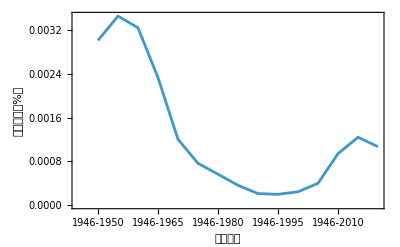

```mathematica
gr4=ListPlot[top1pcArtRatio,Joined->True,Frame->True,FrameLabel->{"累積世代","占有割合（%）"},FrameTicks->{Automatic,{genticks,None}},ImageSize->400]
```

```mathematica
(*Export[expordoctdir<>"gr4.eps",gr4,"EPS"]*)
```

累積世代ごとの高被引用論文の全論文に占める割合（%）

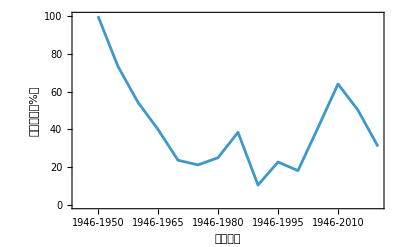

```mathematica
gr5=ListPlot[newcomerratio,Joined->True,Frame->True,FrameLabel->{"累積世代","占有割合（%）"},FrameTicks->{Automatic,{genticks,None}},ImageSize->400]
```

```mathematica
genticksDiff=Map[{#[[1]]-1,#[[2]]}&,genticks][[2;;]]
```

{{1,1946-1955},{2,1946-1960},{3,1946-1965},{4,1946-1970},{5,1946-1975},{6,1946-1980},{7,1946-1985},{8,1946-1990},{9,1946-1995},{10,1946-2000},{11,1946-2005},{12,1946-2010},{13,1946-2015},{14,1946-2020}}

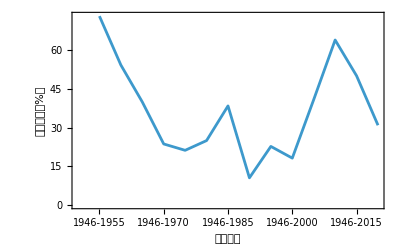

```mathematica
gr5=ListPlot[newcomerratio[[2;;]],Joined->True,Frame->True,FrameLabel->{"累積世代","占有割合（%）"},FrameTicks->{Automatic,{genticksDiff,None}},ImageSize->400]
```

```mathematica
(*Export[expordoctdir<>"gr5.eps",gr5,"EPS"]*)
```

/Volumes/LaCie/BANK/pubmed-analysis/202312/gr5.eps

累積世代ごとの新規出現高被引用論文の高被引用論文に占める割合（%）

## （調査１）主要(G1)論文タイトル

PMIDから論文タイトルを引く

プログラム検討

```mathematica
st=Import["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/pubmed24n0080.xml.blk","String"];
```

```mathematica
st1=Drop[StringSplit[st,"<PubmedArticle>"],1];
```

```mathematica
st2=Map[StringSplit[#,"\n"]&,StringSplit[st1,"\n--\n"],{2}];
```

```mathematica
st3=Map[StringReplace[#,RegularExpression["\\[\\[\\[.*\\]\\]\\]"]->""]&,st2,{3}];
```

```mathematica
titlecase[l_]:=Cases[l,{x_,y_}/;StringMatchQ[x,"<PMID *"]||StringMatchQ[x,"<ArticleTitle>"]]
```

```mathematica
(st3case=Map[titlecase,st3])//Length
```

30000

```mathematica
st3case2=Map[#[[1;;2]]&,Select[st3case,Length[#]>=2&]]
```

```mathematica
st3rule=MapApply[Rule,Map[#[[2]]&,st3case2,{2}]]
```

```mathematica
blkToTitleRule[file_String]:=Module[{st,st1,st2,st3,st3case,st3case2,st3rule},
st=Import[file,"String"];
st1=Drop[StringSplit[st,"<PubmedArticle>"],1];
st2=Map[StringSplit[#,"\n"]&,StringSplit[st1,"\n--\n"],{2}];
st3=Map[StringReplace[#,RegularExpression["\\[\\[\\[.*\\]\\]\\]"]->""]&,st2,{3}];

st3case=Map[titlecase,st3];
st3case2=Map[#[[1;;2]]&,Select[st3case,Length[#]>=2&]];
st3rule=MapApply[Rule,Map[#[[2]]&,st3case2,{2}]]
]
```

プログラム適応

```mathematica
(blks=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/*blk"])//Length
```

1219

```mathematica
(*AbsoluteTiming[(pmidToTitle=Association[Flatten[ParallelMap[blkToTitleRule,blks]]]);]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save",pmidToTitle]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle_V2.save",pmidToTitle]*)
```

高被引用論文タイトル

ルールを読み込む

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];*)
```

```mathematica
(*top1pctitle=Map[{pmidToTitle[#[[1]]],#[[2]]}&,top1PcCitedArtList,{2}];*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitle.save",top1pctitle]*)
```

### 雑誌名つき高被引用論文タイトル

各累積世代のチャンピオン

```mathematica
Map[#[[1]]&,top1PcCitedArtList]
```

{{16747784,74},{16747784,154},{14907713,300},{14907713,1190},{14907713,3876},{14907713,9632},{14907713,17763},{14907713,25451},{14907713,32371},{14907713,37576},{14907713,40229},{14907713,42101},{14907713,44884},{5432063,49961},{5432063,54249}}

```mathematica
chanpionPMID=Map[#[[1,1]]&,top1PcCitedArtList]
```

{16747784,16747784,14907713,14907713,14907713,14907713,14907713,14907713,14907713,14907713,14907713,14907713,14907713,5432063,5432063}

関連情報：

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitle.save"];
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitlewithJ.save"];
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/PMIDtoISSNrl.save"];
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal-title/ISSNvsTitle.save"];
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/PMIDtoMeSHDruleASC.save"];
```

Meshを追加した。

```mathematica
(*(top1pctitlewithJ=Map[{pmidToTitle[#[[1]]],PMIDtoISSNrl[#[[1]]][[1]]//ISSNvsTitle,#[[2]]}&,top1PcCitedArtList,{2}])//Length*)
```

```mathematica
(top1pctitlewithJ=Map[{pmidToTitle[#[[1]]],PMIDtoISSNrl[#[[1]]][[1]]//ISSNvsTitle,PMIDtoMeSHDruleASC[#[[1]]],#[[2]]}&,top1PcCitedArtList,{2}])//Length
```

Part::partw: {}の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

15

```mathematica
top1pctitlewithJ[[1]][[1]]
```

{Qualitative analysis of proteins: a partition chromatographic method using paper.,The Biochemical journal,Missing[KeyAbsent,16747784],74}

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitlewithJ.save",top1pctitlewithJ]*)
```

#### 代表リスト

世代情報

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
gen
```

{1946-1950,1946-1955,1946-1960,1946-1965,1946-1970,1946-1975,1946-1980,1946-1985,1946-1990,1946-1995,1946-2000,1946-2005,1946-2010,1946-2015,1946-2020}

ジャーナル名なし

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitle.save"];*)
```

```mathematica
top1pctitle//TableForm
```

Qualitative analysis of proteins: a partition chromatographic method using paper.
74 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
35 | The biochemistry of bacterial toxins: The lecithinase activity of Cl. welchii toxins.
32 | CLINICAL STUDIES OF THE BLOOD VOLUME. IV. ADAPTATION OF THE METHOD TO THE PHOTOELECTRIC MICROCOLORIMETER.
31 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
29 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
28 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
28 | Bacteriophage-Resistant Mutants in Escherichia Coli.
27 | Pulmonary Calcification in Negative Reactors to Tuberculin.
26 | The Biological Actions and Therapeutic Applications of the B-Chloroethyl Amines and Sulfides.
26 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Qualitative analysis of proteins: a partition chromatographic method using paper.
154 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
120 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
103 | The free amino groups of insulin.
73 | A colorimetric method for the determination of glucosamine and chondrosamine.
71 | Separation of the phosphoric esters on the filter paper chromatogram.
68 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
67 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
66 | The estimation of phosphorus.
65 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
62 | An improved method for the colorimetric determination of phosphate.
62 | The pharmacological actions of polymethylene bistrimethyl-ammonium salts.
62 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
56 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
55 | Studies on cholinesterase: 3. Specific tests for true cholinesterase and pseudo-cholinesterase.
54 | THE NITROUS OXIDE METHOD FOR THE QUANTITATIVE DETERMINATION OF CEREBRAL BLOOD FLOW IN MAN: THEORY, PROCEDURE AND NORMAL VALUES.
54 | The total nitrogen content of egg albumin and other proteins.
51 | The effect of sodium ions on the electrical activity of giant axon of the squid.
47 | The identification of lower peptides in complex mixtures.
47 | THE ESTIMATION OF HEPATIC BLOOD FLOW IN MAN.
46 | CLINICAL STUDIES OF THE BLOOD VOLUME. IV. ADAPTATION OF THE METHOD TO THE PHOTOELECTRIC MICROCOLORIMETER.
45 | Paper Chromatography Using Capillary Ascent.
43 | Bacteriophage-Resistant Mutants in Escherichia Coli.
43 | Protein measurement with the Folin phenol reagent.
43 | The estimation of adrenaline and allied substances in blood.
42 | Purification and properties of cytochrome c.
42 | Simultaneous Adaptation: A New Technique for the Study of Metabolic Pathways.
42 | Sickle cell anemia a molecular disease.
42 | [Electrophoresis of proteins on filter paper].
42 | The biochemistry of bacterial toxins: The lecithinase activity of Cl. welchii toxins.
41 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
300 | A study of fixation for electron microscopy.
235 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
203 | Qualitative analysis of proteins: a partition chromatographic method using paper.
190 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
176 | Separation of the phosphoric esters on the filter paper chromatogram.
150 | The estimation of phosphorus.
142 | An improved method for the colorimetric determination of phosphate.
141 | A colorimetric method for the determination of glucosamine and chondrosamine.
136 | The free amino groups of insulin.
106 | A small particulate component of the cytoplasm.
106 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
100 | An analysis of the end-plate potential recorded with an intracellular electrode.
100 | Methods of paper chromatography of steroids applicable to the study of steroids in mammalian blood and tissues.
99 | Chromatography of amino acids on sulfonated polystyrene resins.
98 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
98 | The effect of sodium ions on the electrical activity of giant axon of the squid.
96 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
95 | A study in microtomy for electron microscopy.
91 | Liver microsomes; an integrated morphological and biochemical study.
88 | The total nitrogen content of egg albumin and other proteins.
87 | Mutants of Escherichia coli requiring methionine or vitamin B12.
87 | [Quantitative determination of blood proteins by paper electrophoresis].
86 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
85 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
82 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
82 | THE NITROUS OXIDE METHOD FOR THE QUANTITATIVE DETERMINATION OF CEREBRAL BLOOD FLOW IN MAN: THEORY, PROCEDURE AND NORMAL VALUES.
81 | Microelectrophoresis of protein on filter-paper.
80 | Sickle cell anemia a molecular disease.
79 | Electrophoresis of proteins on filter paper.
79 | Potassium accumulation in muscle and associated changes.
78 | The estimation of adrenaline and allied substances in blood.
77 | Chromatographic studies of nucleic acids; a technique for the identification and estimation of purine and pyrimidine bases, nucleosides and related substances.
76 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
75 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
74 | Nerve endings in mammalian muscle.
73 | The nucleic acids of plant tissues; the extraction and estimation of desoxypentose nucleic acid and pentose nucleic acid.
73 | The pharmacological actions of polymethylene bistrimethyl-ammonium salts.
73 | THE ESTIMATION OF HEPATIC BLOOD FLOW IN MAN.
72 | The recording of potentials from motoneurones with an intracellular electrode.
72 | The determination of hydroxyproline.
71 | An electron microscope study of the mitochondrial structure.
71 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
71 | The properdin system and immunity. I. Demonstration and isolation of a new serum protein, properdin, and its role in immune phenomena.
70 | The fine structure of mitochondria.
67 | The normal membrane potential of frog sartorius fibers.
65 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
1190 | A study of fixation for electron microscopy.
463 | Improvements in epoxy resin embedding methods.
338 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
269 | Separation of the phosphoric esters on the filter paper chromatogram.
226 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
224 | The estimation of phosphorus.
219 | Qualitative analysis of proteins: a partition chromatographic method using paper.
207 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
197 | An improved method for the colorimetric determination of phosphate.
194 | Staining of tissue sections for electron microscopy with heavy metals.
184 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
178 | Genetic regulatory mechanisms in the synthesis of proteins.
178 | [A micro-method of immuno-electrophoresis].
174 | A colorimetric method for the determination of glucosamine and chondrosamine.
173 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
173 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
169 | The effect of sodium ions on the electrical activity of giant axon of the squid.
167 | Effects of varying the vehicle for OsO4 in tissue fixation.
162 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
159 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
158 | Detection of sugars on paper chromatograms.
158 | A simple method for the isolation and purification of total lipides from animal tissues.
158 | An analysis of the end-plate potential recorded with an intracellular electrode.
157 | Mutants of Escherichia coli requiring methionine or vitamin B12.
156 | Simple methods for "staining with lead" at high pH in electron microscopy.
153 | The free amino groups of insulin.
151 | A small particulate component of the cytoplasm.
150 | Methods of paper chromatography of steroids applicable to the study of steroids in mammalian blood and tissues.
149 | Liver microsomes; an integrated morphological and biochemical study.
148 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
148 | Staining of tissue sections for electron microscopy with heavy metals. II. Application of solutions containing lead and barium.
146 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
146 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
145 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
140 | Chromatography of amino acids on sulfonated polystyrene resins.
134 | Notes on sugar determination.
129 | A press for disrupting bacteria and other micro-organisms.
125 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
124 | Potassium accumulation in muscle and associated changes.
119 | Replica plating and indirect selection of bacterial mutants.
118 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
115 | The determination of hydroxyproline.
113 | The fine structure of neurons.
113 | A revision of the Schoenheimer-Sperry method for cholesterol determination.
110 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
107 | The nucleic acids of plant tissues; the extraction and estimation of desoxypentose nucleic acid and pentose nucleic acid.
107 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
106 | The total nitrogen content of egg albumin and other proteins.
106 | [Quantitative determination of blood proteins by paper electrophoresis].
105 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
3876 | Improvements in epoxy resin embedding methods.
1141 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
1099 | A study of fixation for electron microscopy.
684 | A simple method for the isolation and purification of total lipides from animal tissues.
611 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
579 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
564 | Staining of tissue sections for electron microscopy with heavy metals.
462 | [A micro-method of immuno-electrophoresis].
457 | Genetic regulatory mechanisms in the synthesis of proteins.
376 | Simple methods for "staining with lead" at high pH in electron microscopy.
362 | Detection of sugars on paper chromatograms.
319 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
318 | Chromosome preparations of leukocytes cultured from human peripheral blood.
311 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
309 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
306 | Mutants of Escherichia coli requiring methionine or vitamin B12.
302 | Amino acid metabolism in mammalian cell cultures.
302 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
297 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
297 | Separation of the phosphoric esters on the filter paper chromatogram.
296 | The estimation of phosphorus.
283 | Effects of varying the vehicle for OsO4 in tissue fixation.
278 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
268 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
266 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
253 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
252 | Junctional complexes in various epithelia.
248 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
246 | An improved method for the colorimetric determination of phosphate.
242 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
239 | Phosphorus assay in column chromatography.
239 | The effect of sodium ions on the electrical activity of giant axon of the squid.
232 | A modified procedure for lead staining of thin sections.
228 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
222 | A colorimetric method for the determination of glucosamine and chondrosamine.
221 | Electron microscope study of DNA-containing plasms. II. Vegetative and mature phage DNA as compared with normal bacterial nucleoids in different physiological states.
220 | Qualitative analysis of proteins: a partition chromatographic method using paper.
216 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
9632 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
2400 | Improvements in epoxy resin embedding methods.
1898 | A simple method for the isolation and purification of total lipides from animal tissues.
1214 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
1129 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
862 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
856 | A study of fixation for electron microscopy.
826 | [A micro-method of immuno-electrophoresis].
741 | Staining of tissue sections for electron microscopy with heavy metals.
736 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
725 | Immunochemical quantitation of antigens by single radial immunodiffusion.
651 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
630 | Amino acid metabolism in mammalian cell cultures.
569 | Mutants of Escherichia coli requiring methionine or vitamin B12.
556 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
517 | Chromosome preparations of leukocytes cultured from human peripheral blood.
508 | Genetic regulatory mechanisms in the synthesis of proteins.
506 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
500 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
491 | Phosphorus assay in column chromatography.
490 | Detection of sugars on paper chromatograms.
463 | Simple methods for "staining with lead" at high pH in electron microscopy.
427 | Transduction of linked genetic characters of the host by bacteriophage P1.
424 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
422 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
406 | The thiobarbituric acid assay of sialic acids.
391 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
383 | Application of a microtechnique to viral serological investigations.
372 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
371 | Junctional complexes in various epithelia.
368 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
366 | Separation of the phosphoric esters on the filter paper chromatogram.
363 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
17763 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
3332 | Improvements in epoxy resin embedding methods.
2359 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
2326 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
1916 | A simple method for the isolation and purification of total lipides from animal tissues.
1905 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
1683 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
1545 | Immunochemical quantitation of antigens by single radial immunodiffusion.
1199 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
967 | [A micro-method of immuno-electrophoresis].
887 | Staining of tissue sections for electron microscopy with heavy metals.
881 | A study of fixation for electron microscopy.
876 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
867 | Phosphorus assay in column chromatography.
828 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
776 | Mutants of Escherichia coli requiring methionine or vitamin B12.
765 | Amino acid metabolism in mammalian cell cultures.
763 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
761 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
725 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
720 | A low-viscosity epoxy resin embedding medium for electron microscopy.
715 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
704 | A rapid method of total lipid extraction and purification.
697 | Transduction of linked genetic characters of the host by bacteriophage P1.
674 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
671 | Recalibrated linkage map of Escherichia coli K-12.
669 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
669 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
646 | THE PREPARATION OF I-131-LABELLED HUMAN GROWTH HORMONE OF HIGH SPECIFIC RADIOACTIVITY.
620 | The thiobarbituric acid assay of sialic acids.
606 | Chromosome preparations of leukocytes cultured from human peripheral blood.
600 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
25451 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
8361 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
4209 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
3875 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
2669 | Improvements in epoxy resin embedding methods.
2565 | Sequencing end-labeled DNA with base-specific chemical cleavages.
2551 | A simple method for the isolation and purification of total lipides from animal tissues.
2481 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
2374 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
2336 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2074 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2009 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
1712 | Immunochemical quantitation of antigens by single radial immunodiffusion.
1679 | A new method for sequencing DNA.
1518 | High resolution two-dimensional electrophoresis of proteins.
1448 | DNA sequencing with chain-terminating inhibitors.
1405 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
1235 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
1232 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
1215 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
1207 | Phosphorus assay in column chromatography.
1165 | A rapid method of total lipid extraction and purification.
1139 | A low-viscosity epoxy resin embedding medium for electron microscopy.
1120 | Electrophoretic analysis of the major polypeptides of the human erythrocyte membrane.
1083 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
1077 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
32371 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
18419 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
8434 | DNA sequencing with chain-terminating inhibitors.
8093 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
6705 | Sequencing end-labeled DNA with base-specific chemical cleavages.
5060 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
4814 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4265 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
4242 | A simple method for the isolation and purification of total lipides from animal tissues.
3105 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
3036 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3023 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
2840 | Improvements in epoxy resin embedding methods.
2656 | High resolution two-dimensional electrophoresis of proteins.
2478 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
2460 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2447 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2348 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2341 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
37576 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
28990 | DNA sequencing with chain-terminating inhibitors.
16313 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
12452 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
10601 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
8224 | Sequencing end-labeled DNA with base-specific chemical cleavages.
5856 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
5573 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
4643 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4628 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
4523 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
4284 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
3927 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
3915 | A simple method for the isolation and purification of total lipides from animal tissues.
3673 | A comprehensive set of sequence analysis programs for the VAX.
3504 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3182 | High resolution two-dimensional electrophoresis of proteins.
3079 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
2977 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2864 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
2780 | Improvements in epoxy resin embedding methods.
2702 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
40229 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
35802 | DNA sequencing with chain-terminating inhibitors.
19737 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
16655 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11243 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
10101 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
7559 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6460 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6102 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5255 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
4936 | A comprehensive set of sequence analysis programs for the VAX.
4820 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
4755 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4668 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
4662 | A simple method for the isolation and purification of total lipides from animal tissues.
4146 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
3877 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
3541 | Basic local alignment search tool.
3541 | High resolution two-dimensional electrophoresis of proteins.
3335 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3236 | A simple method for displaying the hydropathic character of a protein.
3202 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
3048 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2957 | A rapid method of total lipid extraction and purification.
2938 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
2917 | Improvements in epoxy resin embedding methods.
2714 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2628 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2619 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
2543 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
2525 | A new method for sequencing DNA.
2436 | Transformation of intact yeast cells treated with alkali cations.
2432 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
42101 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
40217 | DNA sequencing with chain-terminating inhibitors.
20676 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
20317 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11511 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
11052 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
9288 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6746 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6209 | Basic local alignment search tool.
6140 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
5507 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5404 | A comprehensive set of sequence analysis programs for the VAX.
5156 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
5018 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
5018 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
4777 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4674 | A simple method for the isolation and purification of total lipides from animal tissues.
4575 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
4536 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
4300 | A simple method for displaying the hydropathic character of a protein.
3721 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
3677 | High resolution two-dimensional electrophoresis of proteins.
3516 | A rapid method of total lipid extraction and purification.
3382 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3265 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
3127 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
3065 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
2990 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2983 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
2902 | Improvements in epoxy resin embedding methods.
2727 | Transformation of intact yeast cells treated with alkali cations.
2709 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2666 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2656 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
2602 | Studies on transformation of Escherichia coli with plasmids.
2579 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
2562 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
2557 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
2513 | A new method for sequencing DNA.
2477 | Improved tools for biological sequence comparison.
2417 | Genomic sequencing.
2372 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
2272 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
2257 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
2212 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
2192 | New M13 vectors for cloning.
2171 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
2152 | Immunochemical quantitation of antigens by single radial immunodiffusion.
2100 | Selective extraction of polyoma DNA from infected mouse cell cultures.
2031 | Phosphorus assay in column chromatography.
1974 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
1956 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
1954 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
1928 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
1904 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
1874 | Continuous cultures of fused cells secreting antibody of predefined specificity.
1865 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
1850 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
1837 | A low-viscosity epoxy resin embedding medium for electron microscopy.
1759 | Measurement of protein using bicinchoninic acid.
1753 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
1682 | Unidirectional digestion with exonuclease III creates targeted breakpoints for DNA sequencing.
1667 | Use of T7 RNA polymerase to direct expression of cloned genes.
1644 | Improved methods for building protein models in electron density maps and the location of errors in these models.
1642 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
1633 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
44884 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
44636 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
25913 | DNA sequencing with chain-terminating inhibitors.
21195 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
11864 | A short history of SHELX.
11691 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11657 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
10736 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
10632 | Basic local alignment search tool.
10120 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
8976 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6861 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6297 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
5902 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5504 | A simple method for the isolation and purification of total lipides from animal tissues.
5503 | A comprehensive set of sequence analysis programs for the VAX.
5254 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
5177 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
5080 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
5027 | Processing of X-ray diffraction data collected in oscillation mode.
4798 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
4760 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
4732 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4675 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
4486 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
4410 | A simple method for displaying the hydropathic character of a protein.
4387 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
4334 | A rapid method of total lipid extraction and purification.
4316 | The CCP4 suite: programs for protein crystallography.
4080 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
3816 | High resolution two-dimensional electrophoresis of proteins.
3758 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
3574 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
3468 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3311 | Improved methods for building protein models in electron density maps and the location of errors in these models.
3230 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
3219 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
3181 | Coot: model-building tools for molecular graphics.
3157 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
3149 | Studies on transformation of Escherichia coli with plasmids.
3053 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
3016 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2996 | Transformation of intact yeast cells treated with alkali cations.
2964 | Initial sequencing and analysis of the human genome.
2918 | Statistical methods for assessing agreement between two methods of clinical measurement.
2863 | Improved tools for biological sequence comparison.
2791 | Improvements in epoxy resin embedding methods.
2751 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2743 | Refinement of macromolecular structures by the maximum-likelihood method.
2740 | The Protein Data Bank.
2710 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2686 | Cluster analysis and display of genome-wide expression patterns.
2673 | Genomic sequencing.
2604 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
2576 | A new method for sequencing DNA.
2563 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
2562 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
2510 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
2413 | Structure validation in chemical crystallography.
2394 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
2389 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
2353 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
2332 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
2321 | Measurement of protein using bicinchoninic acid.
2317 | The hallmarks of cancer.
2312 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
2282 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
2234 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
2233 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
2214 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
2210 | New M13 vectors for cloning.
2192 | Selective extraction of polyoma DNA from infected mouse cell cultures.
2166 | MEGA3: Integrated software for Molecular Evolutionary Genetics Analysis and sequence alignment.
2154 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
2128 | Immunochemical quantitation of antigens by single radial immunodiffusion.
2121 | Phosphorus assay in column chromatography.
2117 | Continuous cultures of fused cells secreting antibody of predefined specificity.
2104 | Significance analysis of microarrays applied to the ionizing radiation response.
2104 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
2096 | Tricine-sodium dodecyl sulfate-polyacrylamide gel electrophoresis for the separation of proteins in the range from 1 to 100 kDa.
2060 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
2050 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
2027 | The assessment and analysis of handedness: the Edinburgh inventory.
2023 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
2017 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
2011 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
1995 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
1970 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
1955 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
1940 | The genetics of Caenorhabditis elegans.
1940 | A low-viscosity epoxy resin embedding medium for electron microscopy.
1913 | MicroRNAs: genomics, biogenesis, mechanism, and function.
1902 | Primer3 on the WWW for general users and for biologist programmers.
1881 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
1852 | Use of T7 RNA polymerase to direct expression of cloned genes.
1839 | Haploview: analysis and visualization of LD and haplotype maps.
1820 | A new mathematical model for relative quantification in real-time RT-PCR.
1800 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
1792 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
1788 | Cancer statistics, 2008.
1785 | A simple salting out procedure for extracting DNA from human nucleated cells.
1777 | VMD: visual molecular dynamics.
1754 | The 1982 revised criteria for the classification of systemic lupus erythematosus.
1751 | Analysis of the genome sequence of the flowering plant Arabidopsis thaliana.
1730 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
1728 | The measurement of observer agreement for categorical data.
1714 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
1703 | Unidirectional digestion with exonuclease III creates targeted breakpoints for DNA sequencing.
1674 | Site-directed mutagenesis by overlap extension using the polymerase chain reaction.
1673 | A complementation analysis of the restriction and modification of DNA in Escherichia coli.
1661 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
1643 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
1635 | MODELTEST: testing the model of DNA substitution.
1629 | Single-step purification of polypeptides expressed in Escherichia coli as fusions with glutathione S-transferase.
1618 | Dendritic cells and the control of immunity.
1615 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
1604 | Nitric oxide: physiology, pathophysiology, and pharmacology.
1600 | Solvent content of protein crystals.
1597 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
1590 | Enzymatic amplification of beta-globin genomic sequences and restriction site analysis for diagnosis of sickle cell anemia.
1572 | Electrophoretic analysis of the major polypeptides of the human erythrocyte membrane.
1548 | An inventory for measuring depression.
1548 | TreeView: an application to display phylogenetic trees on personal computers.
1542 | The sequence of the human genome.
1538 | THE PREPARATION OF I-131-LABELLED HUMAN GROWTH HORMONE OF HIGH SPECIFIC RADIOACTIVITY.
1533 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
1529 | Mfold web server for nucleic acid folding and hybridization prediction.
1527 | A rating scale for depression.
1523 | Peptide mapping by limited proteolysis in sodium dodecyl sulfate and analysis by gel electrophoresis.
1521 | SWISS-MODEL and the Swiss-PdbViewer: an environment for comparative protein modeling.
1513 | Atherosclerosis--an inflammatory disease.
1512 | Global cancer statistics, 2002.
1507 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
1504 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
1500 | The complete genome sequence of Escherichia coli K-12.
1495 | Efficient transfer of large DNA fragments from agarose gels to diazobenzyloxymethyl-paper and rapid hybridization by using dextran sulfate.
1491 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
1485 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
1477 | Relationship between the inhibition constant (K1) and the concentration of inhibitor which causes 50 per cent inhibition (I50) of an enzymatic reaction.
1469 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
1467 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
1466 | Use of bacteriophage T7 RNA polymerase to direct selective high-level expression of cloned genes.
1463 | MAPMAKER: an interactive computer package for constructing primary genetic linkage maps of experimental and natural populations.
1449 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
1448 | High-efficiency transformation of mammalian cells by plasmid DNA.
1442 | Interpreting chromosomal DNA restriction patterns produced by pulsed-field gel electrophoresis: criteria for bacterial strain typing.
1441 | Preparation of iodine-131 labelled human growth hormone of high specific activity.
1435 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
1426 | One-step gene disruption in yeast.
1406 | The 3'-terminal sequence of Escherichia coli 16S ribosomal RNA: complementarity to nonsense triplets and ribosome binding sites.
1400 | A membrane-filter technique for the detection of complementary DNA.
1399 | Organization and expression of eucaryotic split genes coding for proteins.
1394 | Integrins: versatility, modulation, and signaling in cell adhesion.
1394 | Quantitative film detection of 3H and 14C in polyacrylamide gels by fluorography.
1385 | MRBAYES: Bayesian inference of phylogenetic trees.
1375 | A rapid boiling method for the preparation of bacterial plasmids.
1373 | A simple and very efficient method for generating cDNA libraries.
1373 | Bioconductor: open software development for computational biology and bioinformatics.
1373 | Transformation of mammalian cells to antibiotic resistance with a bacterial gene under control of the SV40 early region promoter.
1363 | Tissue sulfhydryl groups.
1363 | The hospital anxiety and depression scale.
1361 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
1360 | Sequence and organization of the human mitochondrial genome.
1359 | Duplexes of 21-nucleotide RNAs mediate RNA interference in cultured mammalian cells.
1359 | Sizing and mapping of early adenovirus mRNAs by gel electrophoresis of S1 endonuclease-digested hybrids.
1350 | MOLMOL: a program for display and analysis of macromolecular structures.
1348 | Colony hybridization: a method for the isolation of cloned DNAs that contain a specific gene.
1345 | WAF1, a potential mediator of p53 tumor suppression.
1344 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
1337 | PAML: a program package for phylogenetic analysis by maximum likelihood.
1313 | Initial sequencing and comparative analysis of the mouse genome.
1313 | Functional rafts in cell membranes.
1307 | Additional modules for versatile and economical PCR-based gene deletion and modification in Saccharomyces cerevisiae.
1305 | Prevalence of overweight and obesity in the United States, 1999-2004.
1305 | Base-calling of automated sequencer traces using phred. I. Accuracy assessment.
1299 | Cancer statistics, 2007.
1299 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
1299 | Cloning in single-stranded bacteriophage as an aid to rapid DNA sequencing.
1284 | The role of protein kinase C in cell surface signal transduction and tumour promotion.
1282 | A simplification of the protein assay method of Lowry et al. which is more generally applicable.
1274 | A new pair of M13 vectors for selecting either DNA strand of double-digest restriction fragments.
1273 | A haplotype map of the human genome.
1269 | Identification of programmed cell death in situ via specific labeling of nuclear DNA fragmentation.
1263 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
1260 | Translating the histone code.
1256 | A new method for predicting signal sequence cleavage sites.
1252 | The obligatory role of endothelial cells in the relaxation of arterial smooth muscle by acetylcholine.
1249 | Comparative protein modelling by satisfaction of spatial restraints.
1245 | Distantly related sequences in the alpha- and beta-subunits of ATP synthase, myosin, kinases and other ATP-requiring enzymes and a common nucleotide binding fold.
1241 | Bacterial evolution.
1237 | Deciphering the biology of Mycobacterium tuberculosis from the complete genome sequence.
1236 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
49961 | Protein measurement with the Folin phenol reagent.
49164 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
34711 | A short history of SHELX.
25235 | DNA sequencing with chain-terminating inhibitors.
21828 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
18496 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
17655 | Basic local alignment search tool.
17099 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
13394 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
12849 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
11899 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11777 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
10792 | Processing of X-ray diffraction data collected in oscillation mode.
9071 | Coot: model-building tools for molecular graphics.
8584 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
8247 | MEGA5: molecular evolutionary genetics analysis using maximum likelihood, evolutionary distance, and maximum parsimony methods.
7987 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
7591 | A simple method for the isolation and purification of total lipides from animal tissues.
7550 | Global cancer statistics.
7492 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
7115 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
7065 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6926 | MicroRNAs: genomics, biogenesis, mechanism, and function.
6917 | Structure validation in chemical crystallography.
6590 | The CCP4 suite: programs for protein crystallography.
6527 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6375 | A rapid method of total lipid extraction and purification.
6326 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
6232 | Hallmarks of cancer: the next generation.
6017 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
5926 | A new mathematical model for relative quantification in real-time RT-PCR.
5906 | Statistical methods for assessing agreement between two methods of clinical measurement.
5804 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
5801 | Clustal W and Clustal X version 2.0.
5749 | Systematic and integrative analysis of large gene lists using DAVID bioinformatics resources.
5732 | PLINK: a tool set for whole-genome association and population-based linkage analyses.
5696 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
5605 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5584 | The assessment and analysis of handedness: the Edinburgh inventory.
5416 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
5414 | Meta-analysis in clinical trials.
5407 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
5362 | Refinement of macromolecular structures by the maximum-likelihood method.
5345 | The Protein Data Bank.
5311 | A comprehensive set of sequence analysis programs for the VAX.
5293 | A simple method for displaying the hydropathic character of a protein.
5232 | The hallmarks of cancer.
5201 | The measurement of observer agreement for categorical data.
5168 | Bias in meta-analysis detected by a simple, graphical test.
5043 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
5002 | Measuring inconsistency in meta-analyses.
4989 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
4949 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
4935 | Initial sequencing and analysis of the human genome.
4840 | VMD: visual molecular dynamics.
4723 | Gene set enrichment analysis: a knowledge-based approach for interpreting genome-wide expression profiles.
4702 | Global cancer statistics, 2002.
4692 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4686 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
4598 | Induction of pluripotent stem cells from mouse embryonic and adult fibroblast cultures by defined factors.
4595 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
4528 | The Sequence Alignment/Map format and SAMtools.
4463 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
4436 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
4385 | UCSF Chimera--a visualization system for exploratory research and analysis.
4379 | Primer3 on the WWW for general users and for biologist programmers.
4376 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
4365 | Haploview: analysis and visualization of LD and haplotype maps.
4352 | Cancer statistics, 2010.
4297 | Cluster analysis and display of genome-wide expression patterns.
4277 | Fast and accurate short read alignment with Burrows-Wheeler transform.
4260 | Phaser crystallographic software.
4207 | Ultrafast and memory-efficient alignment of short DNA sequences to the human genome.
4158 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
4145 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
4109 | Bioconductor: open software development for computational biology and bioinformatics.
4059 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
3985 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
3966 | High resolution two-dimensional electrophoresis of proteins.
3966 | Inference of population structure using multilocus genotype data.
3962 | Significance analysis of microarrays applied to the ionizing radiation response.
3959 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
3920 | MicroRNAs: target recognition and regulatory functions.
3886 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
3884 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
3877 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
3872 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
3802 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
3781 | Linear models and empirical bayes methods for assessing differential expression in microarray experiments.
3771 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
3739 | Induction of pluripotent stem cells from adult human fibroblasts by defined factors.
3738 | Improved methods for building protein models in electron density maps and the location of errors in these models.
3735 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
3734 | The hospital anxiety and depression scale.
3727 | The genetics of Caenorhabditis elegans.
3691 | PHENIX: a comprehensive Python-based system for macromolecular structure solution.
3651 | Cancer statistics, 2012.
3636 | Accurate normalization of real-time quantitative RT-PCR data by geometric averaging of multiple internal control genes.
3568 | Studies on transformation of Escherichia coli with plasmids.
3551 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
3508 | Multilineage potential of adult human mesenchymal stem cells.
3457 | A rating scale for depression.
3454 | An inventory for measuring depression.
3439 | Cancer statistics, 2009.
3416 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
3415 | Estimates of worldwide burden of cancer in 2008: GLOBOCAN 2008.
3396 | Cancer statistics, 2008.
3385 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3382 | Conserved seed pairing, often flanked by adenosines, indicates that thousands of human genes are microRNA targets.
3343 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
3323 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
3297 | Cancer statistics, 2013.
3288 | Mfold web server for nucleic acid folding and hybridization prediction.
3263 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
3223 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
3192 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
3162 | Transformation of intact yeast cells treated with alkali cations.
3154 | Features and development of Coot.
3135 | A simple salting out procedure for extracting DNA from human nucleated cells.
3128 | Measurement of protein using bicinchoninic acid.
3102 | MRBAYES: Bayesian inference of phylogenetic trees.
3096 | Improved tools for biological sequence comparison.
3064 | Radiotherapy plus concomitant and adjuvant temozolomide for glioblastoma.
3040 | Mapping and quantifying mammalian transcriptomes by RNA-Seq.
3034 | Atherosclerosis--an inflammatory disease.
3020 | Quantifying heterogeneity in a meta-analysis.
3018 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
3002 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
2949 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
2868 | Comparative protein modelling by satisfaction of spatial restraints.
2856 | Molecular portraits of human breast tumours.
2850 | MODELTEST: testing the model of DNA substitution.
2843 | KEGG: kyoto encyclopedia of genes and genomes.
2840 | MEGA3: Integrated software for Molecular Evolutionary Genetics Analysis and sequence alignment.
2822 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2798 | Reduction in the incidence of type 2 diabetes with lifestyle intervention or metformin.
2795 | Improvements in epoxy resin embedding methods.
2781 | tRNAscan-SE: a program for improved detection of transfer RNA genes in genomic sequence.
2777 | DAVID: Database for Annotation, Visualization, and Integrated Discovery.
2774 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
2771 | Solvent content of protein crystals.
2760 | Third Report of the National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, and Treatment of High Blood Cholesterol in Adults (Adult Treatment Panel III) final report.
2746 | Cytoscape: a software environment for integrated models of biomolecular interaction networks.
2745 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
2742 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
2727 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
2725 | Genomic sequencing.
2724 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2722 | Obesity: preventing and managing the global epidemic. Report of a WHO consultation.
2718 | Analyzing real-time PCR data by the comparative C(T) method.
2712 | Dendritic cells and the control of immunity.
2684 | A new method for sequencing DNA.
2665 | Statistical significance for genomewide studies.
2663 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
2642 | Embryonic stem cell lines derived from human blastocysts.
2633 | A map of human genome variation from population-scale sequencing.
2623 | Statistical aspects of the analysis of data from retrospective studies of disease.
2620 | Principal components analysis corrects for stratification in genome-wide association studies.
2612 | Induced pluripotent stem cell lines derived from human somatic cells.
2598 | A comparison of normalization methods for high density oligonucleotide array data based on variance and bias.
2594 | RAxML-VI-HPC: maximum likelihood-based phylogenetic analyses with thousands of taxa and mixed models.
2576 | The Psychophysics Toolbox.
2569 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
2569 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
2563 | A more accurate method to estimate glomerular filtration rate from serum creatinine: a new prediction equation. Modification of Diet in Renal Disease Study Group.
2551 | Continuous cultures of fused cells secreting antibody of predefined specificity.
2539 | SWISS-MODEL and the Swiss-PdbViewer: an environment for comparative protein modeling.
2528 | Velvet: algorithms for de novo short read assembly using de Bruijn graphs.
2520 | Chromatin modifications and their function.
2515 | Predicting transmembrane protein topology with a hidden Markov model: application to complete genomes.
2513 | All-atom empirical potential for molecular modeling and dynamics studies of proteins.
2492 | Tricine-sodium dodecyl sulfate-polyacrylamide gel electrophoresis for the separation of proteins in the range from 1 to 100 kDa.
2490 | The amyloid hypothesis of Alzheimer's disease: progress and problems on the road to therapeutics.
2476 | The 1982 revised criteria for the classification of systemic lupus erythematosus.
2461 | The Mini-International Neuropsychiatric Interview (M.I.N.I.): the development and validation of a structured diagnostic psychiatric interview for DSM-IV and ICD-10.
2459 | Assessing the quality of reports of randomized clinical trials: is blinding necessary?
2458 | WebLogo: a sequence logo generator.
2453 | Scalable molecular dynamics with NAMD.
2448 | Automated anatomical labeling of activations in SPM using a macroscopic anatomical parcellation of the MNI MRI single-subject brain.
2445 | Prevalence of overweight and obesity in the United States, 1999-2004.
2428 | BLAT--the BLAST-like alignment tool.
2414 | Genome sequencing in microfabricated high-density picolitre reactors.
2412 | Inflammation and cancer.
2411 | Analysis of the genome sequence of the flowering plant Arabidopsis thaliana.
2411 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
2409 | AFNI: software for analysis and visualization of functional magnetic resonance neuroimages.
2402 | Prospective identification of tumorigenic breast cancer cells.
2387 | A default mode of brain function.
2382 | A 12-Item Short-Form Health Survey: construction of scales and preliminary tests of reliability and validity.
2378 | Seventh report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure.
2368 | TopHat: discovering splice junctions with RNA-Seq.
2367 | NIH Image to ImageJ: 25 years of image analysis.
2366 | The C. elegans heterochronic gene lin-4 encodes small RNAs with antisense complementarity to lin-14.
2364 | Translating the histone code.
2361 | Gene Expression Omnibus: NCBI gene expression and hybridization array data repository.
2350 | Gene expression patterns of breast carcinomas distinguish tumor subclasses with clinical implications.
2348 | Global prevalence of diabetes: estimates for the year 2000 and projections for 2030.
2323 | Statistical method for testing the neutral mutation hypothesis by DNA polymorphism.
2320 | MicroRNA expression profiles classify human cancers.
2318 | Assay for lipid peroxides in animal tissues by thiobarbituric acid reaction.
2311 | The sequence of the human genome.
2302 | BEAST: Bayesian evolutionary analysis by sampling trees.
2301 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
2289 | Phosphorus assay in column chromatography.
2275 | Selective extraction of polyoma DNA from infected mouse cell cultures.
2274 | APACHE II: a severity of disease classification system.
2266 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
2264 | Tissue sulfhydryl groups.
2257 | XDS.
2255 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
2250 | Neuropathological stageing of Alzheimer-related changes.
2250 | Advances in functional and structural MR image analysis and implementation as FSL.
2242 | The functions of animal microRNAs.
2242 | Cancer statistics, 2014.
2239 | New M13 vectors for cloning.
2233 | Site-directed mutagenesis by overlap extension using the polymerase chain reaction.
2232 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
2222 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
2219 | K/DOQI clinical practice guidelines for chronic kidney disease: evaluation, classification, and stratification.
2210 | Lifetime prevalence and age-of-onset distributions of DSM-IV disorders in the National Comorbidity Survey Replication.
2209 | Improved prediction of signal peptides: SignalP 3.0.
2193 | The PHQ-9: validity of a brief depression severity measure.
2192 | Activating mutations in the epidermal growth factor receptor underlying responsiveness of non-small-cell lung cancer to gefitinib.
2183 | An integrated encyclopedia of DNA elements in the human genome.
2178 | Risks and benefits of estrogen plus progestin in healthy postmenopausal women: principal results From the Women's Health Initiative randomized controlled trial.
2176 | Prediction of creatinine clearance from serum creatinine.
2174 | The FagerstrÃ¶m Test for Nicotine Dependence: a revision of the FagerstrÃ¶m Tolerance Questionnaire.
2170 | TreeView: an application to display phylogenetic trees on personal computers.
2169 | Bioinformatics enrichment tools: paths toward the comprehensive functional analysis of large gene lists.
2155 | A method and server for predicting damaging missense mutations.
2147 | Immunochemical quantitation of antigens by single radial immunodiffusion.
2142 | Development of the Colle-Salvetti correlation-energy formula into a functional of the electron density.
2141 | High-resolution profiling of histone methylations in the human genome.
2140 | The RAST Server: rapid annotations using subsystems technology.
2136 | Relationship between the inhibition constant (K1) and the concentration of inhibitor which causes 50 per cent inhibition (I50) of an enzymatic reaction.
2135 | The Pittsburgh Sleep Quality Index: a new instrument for psychiatric practice and research.
2133 | The positive and negative syndrome scale (PANSS) for schizophrenia.
2125 | Development and validation of brief measures of positive and negative affect: the PANAS scales.
2120 | PAML 4: phylogenetic analysis by maximum likelihood.
2113 | Transcript assembly and quantification by RNA-Seq reveals unannotated transcripts and isoform switching during cell differentiation.
2112 | A low-viscosity epoxy resin embedding medium for electron microscopy.
2109 | Intraclass correlations: uses in assessing rater reliability.
2108 | The human genome browser at UCSC.
2108 | Arlequin (version 3.0): an integrated software package for population genetics data analysis.
2107 | Vitamin D deficiency.
2105 | Additional modules for versatile and economical PCR-based gene deletion and modification in Saccharomyces cerevisiae.
2104 | Base-calling of automated sequencer traces using phred. I. Accuracy assessment.
2101 | Gene expression profiling predicts clinical outcome of breast cancer.
2101 | EMBOSS: the European Molecular Biology Open Software Suite.
2101 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
2097 | Cancer statistics, 2007.
2087 | MolProbity: all-atom structure validation for macromolecular crystallography.
2085 | Differential expression analysis for sequence count data.
2084 | Nitric oxide: physiology, pathophysiology, and pharmacology.
2080 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
2076 | Stem cells, cancer, and cancer stem cells.
2074 | Duplexes of 21-nucleotide RNAs mediate RNA interference in cultured mammalian cells.
2073 | Initial sequencing and comparative analysis of the mouse genome.
2068 | Interpreting chromosomal DNA restriction patterns produced by pulsed-field gel electrophoresis: criteria for bacterial strain typing.
2063 | Pathogen recognition and innate immunity.
2052 | The complete genome sequence of Escherichia coli K-12.
2045 | Human breast cancer: correlation of relapse and survival with amplification of the HER-2/neu oncogene.
2044 | The 2007 WHO classification of tumours of the central nervous system.
2043 | RNA-Seq: a revolutionary tool for transcriptomics.
2042 | Bevacizumab plus irinotecan, fluorouracil, and leucovorin for metastatic colorectal cancer.
2030 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
2029 | Overview of the CCP4 suite and current developments.
2011 | Establishing a standard definition for child overweight and obesity worldwide: international survey.
2008 | The meaning and use of the area under a receiver operating characteristic (ROC) curve.
2000 | Use of T7 RNA polymerase to direct expression of cloned genes.
1994 | A haplotype map of the human genome.
1992 | Comprehensive genomic characterization defines human glioblastoma genes and core pathways.
1990 | On the origin of cancer cells.
1988 | Deciphering the biology of Mycobacterium tuberculosis from the complete genome sequence.
1976 | EuroQol--a new facility for the measurement of health-related quality of life.
1974 | A genetic model for colorectal tumorigenesis.
1973 | A new and rapid colorimetric determination of acetylcholinesterase activity.
1972 | A synaptic model of memory: long-term potentiation in the hippocampus.
1971 | Finding the missing heritability of complex diseases.
1970 | Autism Diagnostic Interview-Revised: a revised version of a diagnostic interview for caregivers of individuals with possible pervasive developmental disorders.
1963 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
1962 | An integrative theory of prefrontal cortex function.
1961 | Base-calling of automated sequencer traces using phred. II. Error probabilities.
1959 | The epithelial-mesenchymal transition generates cells with properties of stem cells.
1951 | Generalized lacZ expression with the ROSA26 Cre reporter strain.
1939 | Crystal structure of the nucleosome core particle at 2.8 A resolution.
1937 | A global measure of perceived stress.
1932 | A power primer.
1932 | Introducing mothur: open-source, platform-independent, community-supported software for describing and comparing microbial communities.
1930 | The Genome Analysis Toolkit: a MapReduce framework for analyzing next-generation DNA sequencing data.
1921 | Stages of embryonic development of the zebrafish.
1920 | Functional rafts in cell membranes.
1915 | Improved survival with ipilimumab in patients with metastatic melanoma.
1912 | The language of covalent histone modifications.
1911 | EGFR mutations in lung cancer: correlation with clinical response to gefitinib therapy.
1909 | Mutations of the BRAF gene in human cancer.
1909 | Blast2GO: a universal tool for annotation, visualization and analysis in functional genomics research.
1903 | The ubiquitin system.
1899 | Operating characteristics of a rank correlation test for publication bias.
1899 | Mass spectrometric sequencing of proteins silver-stained polyacrylamide gels.
1898 | Collective dynamics of 'small-world' networks.
1896 | New response evaluation criteria in solid tumours: revised RECIST guideline (version 1.1).
1893 | QIIME allows analysis of high-throughput community sequencing data.
1891 | Inference of macromolecular assemblies from crystalline state.
1887 | Integrins: bidirectional, allosteric signaling machines.
1880 | Positional cloning of the mouse obese gene and its human homologue.
1879 | Control of goal-directed and stimulus-driven attention in the brain.
1878 | MEGA6: Molecular Evolutionary Genetics Analysis version 6.0.
1875 | MOLMOL: a program for display and analysis of macromolecular structures.
1856 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
1856 | Functional connectivity in the motor cortex of resting human brain using echo-planar MRI.
1848 | MAPMAKER: an interactive computer package for constructing primary genetic linkage maps of experimental and natural populations.
1846 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
1844 | Apoptosis: a basic biological phenomenon with wide-ranging implications in tissue kinetics.
1843 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
54249 | Protein measurement with the Folin phenol reagent.
53050 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
47343 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
44350 | A short history of SHELX.
27998 | Basic local alignment search tool.
26196 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
23032 | DNA sequencing with chain-terminating inhibitors.
22517 | Hallmarks of cancer: the next generation.
18449 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
18152 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
16282 | The Sequence Alignment/Map format and SAMtools.
15705 | Systematic and integrative analysis of large gene lists using DAVID bioinformatics resources.
14250 | Global cancer statistics.
13930 | Fast and accurate short read alignment with Burrows-Wheeler transform.
13533 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
13523 | Measuring inconsistency in meta-analyses.
13449 | MicroRNAs: genomics, biogenesis, mechanism, and function.
13435 | Coot: model-building tools for molecular graphics.
13318 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
13202 | Gene set enrichment analysis: a knowledge-based approach for interpreting genome-wide expression profiles.
13016 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
12950 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
12906 | MEGA5: molecular evolutionary genetics analysis using maximum likelihood, evolutionary distance, and maximum parsimony methods.
12418 | Global cancer statistics 2018: GLOBOCAN estimates of incidence and mortality worldwide for 36 cancers in 185 countries.
12151 | Fast gapped-read alignment with Bowtie 2.
12038 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
12009 | Bias in meta-analysis detected by a simple, graphical test.
11911 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11896 | Processing of X-ray diffraction data collected in oscillation mode.
11884 | Moderated estimation of fold change and  dispersion for RNA-seq data with DESeq2.
11520 | MEGA6: Molecular Evolutionary Genetics Analysis version 6.0.
11338 | UCSF Chimera--a visualization system for exploratory research and analysis.
11217 | PLINK: a tool set for whole-genome association and population-based linkage analyses.
11169 | Global cancer statistics, 2012.
11146 | NIH Image to ImageJ: 25 years of image analysis.
11117 | The measurement of observer agreement for categorical data.
11001 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
10863 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
10847 | Fiji: an open-source platform for biological-image analysis.
10590 | Meta-analysis in clinical trials.
10447 | A new mathematical model for relative quantification in real-time RT-PCR.
10424 | Trimmomatic: a flexible trimmer for Illumina sequence data.
10321 | A simple method for the isolation and purification of total lipides from animal tissues.
10284 | Cytoscape: a software environment for integrated models of biomolecular interaction networks.
10013 | edgeR: a Bioconductor package for differential expression analysis of digital gene expression data.
9769 | PHENIX: a comprehensive Python-based system for macromolecular structure solution.
9687 | QIIME allows analysis of high-throughput community sequencing data.
9614 | Clustal W and Clustal X version 2.0.
9543 | Statistical methods for assessing agreement between two methods of clinical measurement.
9470 | Cancer incidence and mortality worldwide: sources, methods and major patterns in GLOBOCAN 2012.
9397 | VMD: visual molecular dynamics.
9355 | Ultrafast and memory-efficient alignment of short DNA sequences to the human genome.
9279 | Features and development of Coot.
9110 | The assessment and analysis of handedness: the Edinburgh inventory.
9098 | Phaser crystallographic software.
8781 | A rapid method of total lipid extraction and purification.
8775 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
8772 | The Protein Data Bank.
8507 | MEGA7: Molecular Evolutionary Genetics Analysis Version 7.0 for Bigger Datasets.
8481 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
8278 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
8203 | Clinical features of patients infected with 2019 novel coronavirus in Wuhan, China.
8187 | The hospital anxiety and depression scale.
8103 | Induction of pluripotent stem cells from mouse embryonic and adult fibroblast cultures by defined factors.
8084 | MicroRNAs: target recognition and regulatory functions.
8058 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
8044 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
8013 | STAR: ultrafast universal RNA-seq aligner.
7784 | The hallmarks of cancer.
7743 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
7600 | The CCP4 suite: programs for protein crystallography.
7525 | The Genome Analysis Toolkit: a MapReduce framework for analyzing next-generation DNA sequencing data.
7523 | Inference of population structure using multilocus genotype data.
7490 | Structure validation in chemical crystallography.
7480 | Research electronic data capture (REDCap)--a metadata-driven methodology and workflow process for providing translational research informatics support.
7479 | KEGG: kyoto encyclopedia of genes and genomes.
7468 | Quantifying heterogeneity in a meta-analysis.
7340 | Analyzing real-time PCR data by the comparative C(T) method.
7319 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6956 | Refinement of macromolecular structures by the maximum-likelihood method.
6923 | MAFFT multiple sequence alignment software version 7: improvements in performance and usability.
6909 | Cancer statistics, 2016.
6879 | New response evaluation criteria in solid tumours: revised RECIST guideline (version 1.1).
6735 | The PHQ-9: validity of a brief depression severity measure.
6674 | Initial sequencing and analysis of the human genome.
6614 | Induction of pluripotent stem cells from adult human fibroblasts by defined factors.
6535 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
6499 | Radiotherapy plus concomitant and adjuvant temozolomide for glioblastoma.
6461 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
6454 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
6451 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
6426 | An integrated encyclopedia of DNA elements in the human genome.
6411 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6408 | RAxML version 8: a tool for phylogenetic analysis and post-analysis of large phylogenies.
6396 | Accurate normalization of real-time quantitative RT-PCR data by geometric averaging of multiple internal control genes.
6373 | Cancer Statistics, 2017.
6275 | Estimates of worldwide burden of cancer in 2008: GLOBOCAN 2008.
6251 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
6244 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
6242 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
6211 | G*Power 3: a flexible statistical power analysis program for the social, behavioral, and biomedical sciences.
6186 | BEDTools: a flexible suite of utilities for comparing genomic features.
6181 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
6170 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
6122 | A simple method for displaying the hydropathic character of a protein.
6120 | Haploview: analysis and visualization of LD and haplotype maps.
6113 | Global cancer statistics, 2002.
6096 | Differential expression analysis for sequence count data.
6076 | Transcript assembly and quantification by RNA-Seq reveals unannotated transcripts and isoform switching during cell differentiation.
6037 | SPAdes: a new genome assembly algorithm and its applications to single-cell sequencing.
6011 | XDS.
5992 | A new equation to estimate glomerular filtration rate.
5927 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
5921 | TopHat: discovering splice junctions with RNA-Seq.
5894 | Bioconductor: open software development for computational biology and bioinformatics.
5892 | Cancer statistics in China, 2015.
5869 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
5862 | Search and clustering orders of magnitude faster than BLAST.
5852 | Generalized Gradient Approximation Made Simple.
5820 | A rating scale for depression.
5760 | Bioinformatics enrichment tools: paths toward the comprehensive functional analysis of large gene lists.
5742 | Mapping and quantifying mammalian transcriptomes by RNA-Seq.
5730 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
5724 | The genetics of Caenorhabditis elegans.
5724 | Cancer statistics, 2013.
5714 | Cancer statistics, 2015.
5685 | limma powers differential expression analyses for RNA-sequencing and microarray studies.
5649 | Cancer statistics, 2010.
5640 | Cancer statistics, 2018.
5633 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5629 | Classification of surgical complications: a new proposal with evaluation in a cohort of 6336 patients and results of a survey.
5600 | An inventory for measuring depression.
5596 | Introducing mothur: open-source, platform-independent, community-supported software for describing and comparing microbial communities.
5588 | Linear models and empirical bayes methods for assessing differential expression in microarray experiments.
5582 | HTSeq--a Python framework to work with high-throughput sequencing data.
5581 | Full-length transcriptome assembly from RNA-Seq data without a reference genome.
5557 | The Pittsburgh Sleep Quality Index: a new instrument for psychiatric practice and research.
5555 | The Mini-International Neuropsychiatric Interview (M.I.N.I.): the development and validation of a structured diagnostic psychiatric interview for DSM-IV and ICD-10.
5537 | Clinical Characteristics of Coronavirus Disease 2019 in China.
5526 | Cancer statistics, 2014.
5525 | MolProbity: all-atom structure validation for macromolecular crystallography.
5523 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
5512 | Multilineage potential of adult human mesenchymal stem cells.
5510 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
5500 | The Cochrane Collaboration's tool for assessing risk of bias in randomised trials.
5445 | The Psychophysics Toolbox.
5412 | Primer3 on the WWW for general users and for biologist programmers.
5412 | Obesity: preventing and managing the global epidemic. Report of a WHO consultation.
5352 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
5332 | TopHat2: accurate alignment of transcriptomes in the presence of insertions, deletions and gene fusions.
5302 | A comprehensive set of sequence analysis programs for the VAX.
5299 | Cluster analysis and display of genome-wide expression patterns.
5271 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
5236 | Conserved seed pairing, often flanked by adenosines, indicates that thousands of human genes are microRNA targets.
5228 | Automated anatomical labeling of activations in SPM using a macroscopic anatomical parcellation of the MNI MRI single-subject brain.
5191 | Cancer statistics, 2012.
5134 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
5115 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
5102 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
5100 | A method and server for predicting damaging missense mutations.
5061 | Differential gene and transcript expression analysis of RNA-seq experiments with TopHat and Cufflinks.
5020 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
5002 | Significance analysis of microarrays applied to the ionizing radiation response.
4922 | Overview of the CCP4 suite and current developments.
4900 | Model-based analysis of ChIP-Seq (MACS).
4881 | A power primer.
4853 | Clinical Characteristics of 138 Hospitalized Patients With 2019 Novel Coronavirus-Infected Pneumonia in Wuhan, China.
4852 | New algorithms and methods to estimate maximum-likelihood phylogenies: assessing the performance of PhyML 3.0.
4847 | Mfold web server for nucleic acid folding and hybridization prediction.
4838 | Clinical course and risk factors for mortality of adult inpatients with COVID-19 in Wuhan, China: a retrospective cohort study.
4828 | The RAST Server: rapid annotations using subsystems technology.
4828 | Naive Bayesian classifier for rapid assignment of rRNA sequences into the new bacterial taxonomy.
4827 | Scalable molecular dynamics with NAMD.
4827 | Improved survival with ipilimumab in patients with metastatic melanoma.
4808 | A global measure of perceived stress.
4805 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
4799 | Molecular portraits of human breast tumours.
4780 | Multiplex genome engineering using CRISPR/Cas systems.
4763 | Gene Expression Omnibus: NCBI gene expression and hybridization array data repository.
4756 | tRNAscan-SE: a program for improved detection of transfer RNA genes in genomic sequence.
4753 | Meta-analysis of observational studies in epidemiology: a proposal for reporting. Meta-analysis Of Observational Studies in Epidemiology (MOOSE) group.
4742 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4694 | Understanding the Warburg effect: the metabolic requirements of cell proliferation.
4689 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
4669 | RAxML-VI-HPC: maximum likelihood-based phylogenetic analyses with thousands of taxa and mixed models.
4666 | The cBio cancer genomics portal: an open platform for exploring multidimensional cancer genomics data.
4662 | Reduction in the incidence of type 2 diabetes with lifestyle intervention or metformin.
4645 | Minimal criteria for defining multipotent mesenchymal stromal cells. The International Society for Cellular Therapy position statement.
4632 | MRBAYES: Bayesian inference of phylogenetic trees.
4602 | WebLogo: a sequence logo generator.
4600 | Velvet: algorithms for de novo short read assembly using de Bruijn graphs.
4597 | Advances in functional and structural MR image analysis and implementation as FSL.
4590 | RSEM: accurate transcript quantification from RNA-Seq data with or without a reference genome.
4588 | Development and validation of brief measures of positive and negative affect: the PANAS scales.
4577 | A 12-Item Short-Form Health Survey: construction of scales and preliminary tests of reliability and validity.
4506 | Comparing the areas under two or more correlated receiver operating characteristic curves: a nonparametric approach.
4467 | Operating characteristics of a rank correlation test for publication bias.
4466 | Principal components analysis corrects for stratification in genome-wide association studies.
4464 | Predicting transmembrane protein topology with a hidden Markov model: application to complete genomes.
4460 | A Novel Coronavirus from Patients with Pneumonia in China, 2019.
4457 | Comprehensive molecular portraits of human breast tumours.
4457 | Inflammation and cancer.
4444 | Development of the Colle-Salvetti correlation-energy formula into a functional of the electron density.
4432 | Third Report of the National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, and Treatment of High Blood Cholesterol in Adults (Adult Treatment Panel III) final report.
4425 | Comparative protein modelling by satisfaction of spatial restraints.
4422 | Blast2GO: a universal tool for annotation, visualization and analysis in functional genomics research.
4419 | Geneious Basic: an integrated and extendable desktop software platform for the organization and analysis of sequence data.
4416 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
4409 | Cancer statistics, 2019.
4401 | Safety, activity, and immune correlates of anti-PD-1 antibody in cancer.
4388 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
4386 | MaxQuant enables high peptide identification rates, individualized p.p.b.-range mass accuracies and proteome-wide protein quantification.
4374 | A simple salting out procedure for extracting DNA from human nucleated cells.
4342 | Fast, scalable generation of high-quality protein multiple sequence alignments using Clustal Omega.
4339 | PAML 4: phylogenetic analysis by maximum likelihood.
4333 | Lifetime prevalence and age-of-onset distributions of DSM-IV disorders in the National Comorbidity Survey Replication.
4320 | Detecting the number of clusters of individuals using the software STRUCTURE: a simulation study.
4299 | Three approaches to qualitative content analysis.
4287 | Atherosclerosis--an inflammatory disease.
4282 | Integrative analysis of complex cancer genomics and clinical profiles using the cBioPortal.
4240 | The functions of animal microRNAs.
4240 | Standards and guidelines for the interpretation of sequence variants: a joint consensus recommendation of the American College of Medical Genetics and Genomics and the Association for Molecular Pathology.
4224 | A framework for variation discovery and genotyping using next-generation DNA sequencing data.
4222 | EEGLAB: an open source toolbox for analysis of single-trial EEG dynamics including independent component analysis.
4209 | Frailty in older adults: evidence for a phenotype.
4208 | Neuropathological stageing of Alzheimer-related changes.
4203 | AFNI: software for analysis and visualization of functional magnetic resonance neuroimages.
4193 | Global and regional mortality from 235 causes of death for 20 age groups in 1990 and 2010: a systematic analysis for the Global Burden of Disease Study 2010.
4183 | EuroQol--a new facility for the measurement of health-related quality of life.
4183 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
4182 | MrBayes 3.2: efficient Bayesian phylogenetic inference and model choice across a large model space.
4181 | Cancer statistics, 2009.
4177 | DAVID: Database for Annotation, Visualization, and Integrated Discovery.
4131 | Epidemiological and clinical characteristics of 99 cases of 2019 novel coronavirus pneumonia in Wuhan, China: a descriptive study.
4110 | High resolution two-dimensional electrophoresis of proteins.
4106 | Assessing the quality of reports of randomized clinical trials: is blinding necessary?
4099 | The positive and negative syndrome scale (PANSS) for schizophrenia.
4097 | A more accurate method to estimate glomerular filtration rate from serum creatinine: a new prediction equation. Modification of Diet in Renal Disease Study Group.
4095 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
4085 | On the origin of cancer cells.
4077 | BLAST+: architecture and applications.
4060 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
4058 | Cancer statistics, 2008.
4057 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
4052 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
4051 | Statistical significance for genomewide studies.
4049 | DnaSP v5: a software for comprehensive analysis of DNA polymorphism data.
4045 | The amyloid hypothesis of Alzheimer's disease: progress and problems on the road to therapeutics.
4043 | Embryonic stem cell lines derived from human blastocysts.
4039 | Assay for lipid peroxides in animal tissues by thiobarbituric acid reaction.
4021 | Studies on transformation of Escherichia coli with plasmids.
4020 | The SILVA ribosomal RNA gene database project: improved data processing and web-based tools.
4015 | The human genome browser at UCSC.
4011 | RNA-Seq: a revolutionary tool for transcriptomics.
4010 | Intraclass correlations: uses in assessing rater reliability.
4010 | International physical activity questionnaire: 12-country reliability and validity.
3999 | The 2007 WHO classification of tumours of the central nervous system.
3986 | A default mode of brain function.
3969 | Epithelial-mesenchymal transitions in development and disease.
3943 | Exosome-mediated transfer of mRNAs and microRNAs is a novel mechanism of genetic exchange between cells.
3935 | The C. elegans heterochronic gene lin-4 encodes small RNAs with antisense complementarity to lin-14.
3929 | Measurement of protein using bicinchoninic acid.
3902 | Statistical aspects of the analysis of data from retrospective studies of disease.
3898 | Improved methods for building protein models in electron density maps and the location of errors in these models.
3896 | Chromatin modifications and their function.
3892 | A map of human genome variation from population-scale sequencing.
3891 | Integrative genomics viewer.
3876 | Improved optimization for the robust and accurate linear registration and motion correction of brain images.
3856 | Sorafenib in advanced hepatocellular carcinoma.
3854 | ANNOVAR: functional annotation of genetic variants from high-throughput sequencing data.
3849 | WGCNA: an R package for weighted correlation network analysis.
3836 | The MIQE guidelines: minimum information for publication of quantitative real-time PCR experiments.
3832 | Standardisation of spirometry.
3829 | Prospective identification of tumorigenic breast cancer cells.
3825 | World Medical Association Declaration of Helsinki: ethical principles for medical research involving human subjects.
3810 | Vitamin D deficiency.
3810 | Induced pluripotent stem cell lines derived from human somatic cells.
3793 | Analysis of protein-coding genetic variation in 60,706 humans.
3782 | An integrated map of genetic variation from 1,092 human genomes.
3778 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
3775 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
3742 | UCHIME improves sensitivity and speed of chimera detection.
3737 | A programmable dual-RNA-guided DNA endonuclease in adaptive bacterial immunity.
3736 | Inference of macromolecular assemblies from crystalline state.
3731 | A comparison of normalization methods for high density oligonucleotide array data based on variance and bias.
3726 | BLAT--the BLAST-like alignment tool.
3726 | All-atom empirical potential for molecular modeling and dynamics studies of proteins.
3714 | The FagerstrÃ¶m Test for Nicotine Dependence: a revision of the FagerstrÃ¶m Tolerance Questionnaire.
3694 | AutoDock Vina: improving the speed and accuracy of docking with a new scoring function, efficient optimization, and multithreading.
3693 | Gene expression patterns of breast carcinomas distinguish tumor subclasses with clinical implications.
3684 | The epithelial-mesenchymal transition generates cells with properties of stem cells.
3675 | SignalP 4.0: discriminating signal peptides from transmembrane regions.
3668 | The Montreal Cognitive Assessment, MoCA: a brief screening tool for mild cognitive impairment.
3653 | MicroRNA expression profiles classify human cancers.
3629 | Statistical method for testing the neutral mutation hypothesis by DNA polymorphism.
3628 | APACHE II: a severity of disease classification system.
3612 | The basics of epithelial-mesenchymal transition.
3608 | The blockade of immune checkpoints in cancer immunotherapy.
3607 | Fast and accurate long-read alignment with Burrows-Wheeler transform.
3603 | Fast robust automated brain extraction.
3603 | A global reference for human genetic variation.
3601 | Global prevalence of diabetes: estimates for the year 2000 and projections for 2030.
3591 | Collective dynamics of 'small-world' networks.
3587 | BEAST: Bayesian evolutionary analysis by sampling trees.
3576 | Matrix elasticity directs stem cell lineage specification.
3575 | Greengenes, a chimera-checked 16S rRNA gene database and workbench compatible with ARB.
3566 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
3524 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
3504 | Dendritic cells and the control of immunity.
3503 | GenAlEx 6.5: genetic analysis in Excel. Population genetic software for teaching and research--an update.
3503 | MODELTEST: testing the model of DNA substitution.
3497 | Cancer-related inflammation.
3486 | EMBOSS: the European Molecular Biology Open Software Suite.
3484 | Tissue sulfhydryl groups.
3483 | The meaning and use of the area under a receiver operating characteristic (ROC) curve.
3475 | Functional connectivity in the motor cortex of resting human brain using echo-planar MRI.
3472 | Harmonizing the metabolic syndrome: a joint interim statement of the International Diabetes Federation Task Force on Epidemiology and Prevention; National Heart, Lung, and Blood Institute; American Heart Association; World Heart Federation; International Atherosclerosis Society; and International Association for the Study of Obesity.
3469 | K/DOQI clinical practice guidelines for chronic kidney disease: evaluation, classification, and stratification.
3469 | Seventh report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure.
3463 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
3455 | Activating mutations in the epidermal growth factor receptor underlying responsiveness of non-small-cell lung cancer to gefitinib.
3448 | Cortical surface-based analysis. I. Segmentation and surface reconstruction.
3441 | Consolidated criteria for reporting qualitative research (COREQ): a 32-item checklist for interviews and focus groups.
3437 | Simple combinations of lineage-determining transcription factors prime cis-regulatory elements required for macrophage and B cell identities.
3434 | The Third International Consensus Definitions for Sepsis and Septic Shock (Sepsis-3).
3423 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3422 | Preferred reporting items for systematic review and meta-analysis protocols (PRISMA-P) 2015 statement.
3422 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
3418 | A new method for measuring daytime sleepiness: the Epworth sleepiness scale.
3398 | Pathogen recognition and innate immunity.
3391 | Stages of embryonic development of the zebrafish.
3373 | Comprehensive genomic characterization defines human glioblastoma genes and core pathways.
3370 | Crystal structure refinement with SHELXL.
3362 | Stem cells, cancer, and cancer stem cells.
3343 | An obesity-associated gut microbiome with increased capacity for energy harvest.
3327

ジャーナル名つき

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitlewithJ.save"];*)
```

Part::partw: {}の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

```mathematica
top1pcArtcount=Map[{Length[#]}&,top1pctitlewithJ]
```

{{10},{30},{46},{50},{38},{33},{32},{26},{19},{22},{33},{66},{192},{315},{336}}

```mathematica
top1pcArttblbody=MapThread[Join,{Map[List,gen],Map[#[[1]]&,top1pctitlewithJ],top1pcArtcount}]
```

{{1946-1950,Qualitative analysis of proteins: a partition chromatographic method using paper.,The Biochemical journal,Missing[KeyAbsent,16747784],74,10},{1946-1955,Qualitative analysis of proteins: a partition chromatographic method using paper.,The Biochemical journal,Missing[KeyAbsent,16747784],154,30},{1946-1960,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},300,46},{1946-1965,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},1190,50},{1946-1970,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},3876,38},{1946-1975,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},9632,33},{1946-1980,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},17763,32},{1946-1985,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},25451,26},{1946-1990,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},32371,19},{1946-1995,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},37576,22},{1946-2000,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},40229,33},{1946-2005,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},42101,66},{1946-2010,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},44884,192},{1946-2015,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,Nature,{Autoradiography,Carbon Isotopes,Coliphages,Electrophoresis, Disc,Genes,Genetics, Microbial,Kinetics,Viral Proteins},49961,315},{1946-2020,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,Nature,{Autoradiography,Carbon Isotopes,Coliphages,Electrophoresis, Disc,Genes,Genetics, Microbial,Kinetics,Viral Proteins},54249,336}}

```mathematica
top1pcArttblhead={"累積世代","高被引用論文タイトル","高被引用論文掲載誌タイトル","高被引用テーマ","被引用数","当該累積世代の\n高被引用論文数"}
```

{累積世代,高被引用論文タイトル,高被引用論文掲載誌タイトル,高被引用テーマ,被引用数,当該累積世代の
高被引用論文数}

```mathematica
Prepend[top1pcArttblbody,top1pcArttblhead]/.{_Missing->"-"}//TableForm
```

累積世代 | 高被引用論文タイトル | 高被引用論文掲載誌タイトル | 高被引用テーマ | 被引用数 | 当該累積世代の
高被引用論文数
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | - | 74 | 10
1946-1955 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | - | 154 | 30
1946-1960 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 300 | 46
1946-1965 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 1190 | 50
1946-1970 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 3876 | 38
1946-1975 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 9632 | 33
1946-1980 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 17763 | 32
1946-1985 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 25451 | 26
1946-1990 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 32371 | 19
1946-1995 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 37576 | 22
1946-2000 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 40229 | 33
1946-2005 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 42101 | 66
1946-2010 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 44884 | 192
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | Autoradiography
Carbon Isotopes
Coliphages
Electrophoresis, Disc
Genes
Genetics, Microbial
Kinetics
Viral Proteins | 49961 | 315
1946-2020 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | Autoradiography
Carbon Isotopes
Coliphages
Electrophoresis, Disc
Genes
Genetics, Microbial
Kinetics
Viral Proteins | 54249 | 336

ジャーナル名つき、重複省略版

```mathematica
saaRl1={{3,2}->"Same as above",{3,3}->"Same as above",{3,4}->"Same as above"}
saaRlJ1={{3,2}->"上記と同じ",{3,3}->"上記と同じ",{3,4}->"上記と同じ"}
```

{{3,2}→Same as above,{3,3}→Same as above,{3,4}→Same as above}

{{3,2}→上記と同じ,{3,3}→上記と同じ,{3,4}→上記と同じ}

```mathematica
saaRl2=Flatten[Table[{n,m}->"Same as above",{n,5,14},{m,2,4}]]
saaRlJ2=Flatten[Table[{n,m}->"上記と同じ",{n,5,14},{m,2,4}]]
```

{{5,2}→Same as above,{5,3}→Same as above,{5,4}→Same as above,{6,2}→Same as above,{6,3}→Same as above,{6,4}→Same as above,{7,2}→Same as above,{7,3}→Same as above,{7,4}→Same as above,{8,2}→Same as above,{8,3}→Same as above,{8,4}→Same as above,{9,2}→Same as above,{9,3}→Same as above,{9,4}→Same as above,{10,2}→Same as above,{10,3}→Same as above,{10,4}→Same as above,{11,2}→Same as above,{11,3}→Same as above,{11,4}→Same as above,{12,2}→Same as above,{12,3}→Same as above,{12,4}→Same as above,{13,2}→Same as above,{13,3}→Same as above,{13,4}→Same as above,{14,2}→Same as above,{14,3}→Same as above,{14,4}→Same as above}

{{5,2}→上記と同じ,{5,3}→上記と同じ,{5,4}→上記と同じ,{6,2}→上記と同じ,{6,3}→上記と同じ,{6,4}→上記と同じ,{7,2}→上記と同じ,{7,3}→上記と同じ,{7,4}→上記と同じ,{8,2}→上記と同じ,{8,3}→上記と同じ,{8,4}→上記と同じ,{9,2}→上記と同じ,{9,3}→上記と同じ,{9,4}→上記と同じ,{10,2}→上記と同じ,{10,3}→上記と同じ,{10,4}→上記と同じ,{11,2}→上記と同じ,{11,3}→上記と同じ,{11,4}→上記と同じ,{12,2}→上記と同じ,{12,3}→上記と同じ,{12,4}→上記と同じ,{13,2}→上記と同じ,{13,3}→上記と同じ,{13,4}→上記と同じ,{14,2}→上記と同じ,{14,3}→上記と同じ,{14,4}→上記と同じ}

```mathematica
saaRl3={{16,2}->"Same as above",{16,3}->"Same as above",{16,4}->"Same as above"}
saaRlJ3={{16,2}->"上記と同じ",{16,3}->"上記と同じ",{16,4}->"上記と同じ"}
```

{{16,2}→Same as above,{16,3}→Same as above,{16,4}→Same as above}

{{16,2}→上記と同じ,{16,3}→上記と同じ,{16,4}→上記と同じ}

```mathematica
saaRl=Join[saaRl1,saaRl2,saaRl3]
saaRlJ=Join[saaRlJ1,saaRlJ2,saaRlJ3]
```

{{3,2}→Same as above,{3,3}→Same as above,{3,4}→Same as above,{5,2}→Same as above,{5,3}→Same as above,{5,4}→Same as above,{6,2}→Same as above,{6,3}→Same as above,{6,4}→Same as above,{7,2}→Same as above,{7,3}→Same as above,{7,4}→Same as above,{8,2}→Same as above,{8,3}→Same as above,{8,4}→Same as above,{9,2}→Same as above,{9,3}→Same as above,{9,4}→Same as above,{10,2}→Same as above,{10,3}→Same as above,{10,4}→Same as above,{11,2}→Same as above,{11,3}→Same as above,{11,4}→Same as above,{12,2}→Same as above,{12,3}→Same as above,{12,4}→Same as above,{13,2}→Same as above,{13,3}→Same as above,{13,4}→Same as above,{14,2}→Same as above,{14,3}→Same as above,{14,4}→Same as above,{16,2}→Same as above,{16,3}→Same as above,{16,4}→Same as above}

{{3,2}→上記と同じ,{3,3}→上記と同じ,{3,4}→上記と同じ,{5,2}→上記と同じ,{5,3}→上記と同じ,{5,4}→上記と同じ,{6,2}→上記と同じ,{6,3}→上記と同じ,{6,4}→上記と同じ,{7,2}→上記と同じ,{7,3}→上記と同じ,{7,4}→上記と同じ,{8,2}→上記と同じ,{8,3}→上記と同じ,{8,4}→上記と同じ,{9,2}→上記と同じ,{9,3}→上記と同じ,{9,4}→上記と同じ,{10,2}→上記と同じ,{10,3}→上記と同じ,{10,4}→上記と同じ,{11,2}→上記と同じ,{11,3}→上記と同じ,{11,4}→上記と同じ,{12,2}→上記と同じ,{12,3}→上記と同じ,{12,4}→上記と同じ,{13,2}→上記と同じ,{13,3}→上記と同じ,{13,4}→上記と同じ,{14,2}→上記と同じ,{14,3}→上記と同じ,{14,4}→上記と同じ,{16,2}→上記と同じ,{16,3}→上記と同じ,{16,4}→上記と同じ}

```mathematica
ReplacePart[Prepend[top1pcArttblbody,top1pcArttblhead]/.{_Missing->"-"},saaRl]//TableForm
```

累積世代 | 高被引用論文タイトル | 高被引用論文掲載誌タイトル | 高被引用テーマ | 被引用数 | 当該累積世代の
高被引用論文数
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | - | 74 | 10
1946-1955 | Same as above | Same as above | Same as above | 154 | 30
1946-1960 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 300 | 46
1946-1965 | Same as above | Same as above | Same as above | 1190 | 50
1946-1970 | Same as above | Same as above | Same as above | 3876 | 38
1946-1975 | Same as above | Same as above | Same as above | 9632 | 33
1946-1980 | Same as above | Same as above | Same as above | 17763 | 32
1946-1985 | Same as above | Same as above | Same as above | 25451 | 26
1946-1990 | Same as above | Same as above | Same as above | 32371 | 19
1946-1995 | Same as above | Same as above | Same as above | 37576 | 22
1946-2000 | Same as above | Same as above | Same as above | 40229 | 33
1946-2005 | Same as above | Same as above | Same as above | 42101 | 66
1946-2010 | Same as above | Same as above | Same as above | 44884 | 192
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | Autoradiography
Carbon Isotopes
Coliphages
Electrophoresis, Disc
Genes
Genetics, Microbial
Kinetics
Viral Proteins | 49961 | 315
1946-2020 | Same as above | Same as above | Same as above | 54249 | 336

```mathematica
TABhctitlesA=ReplacePart[Prepend[top1pcArttblbody,top1pcArttblhead]/.{_Missing->"-"},saaRlJ]//TableForm
```

累積世代 | 高被引用論文タイトル | 高被引用論文掲載誌タイトル | 高被引用テーマ | 被引用数 | 当該累積世代の
高被引用論文数
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | - | 74 | 10
1946-1955 | 上記と同じ | 上記と同じ | 上記と同じ | 154 | 30
1946-1960 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 300 | 46
1946-1965 | 上記と同じ | 上記と同じ | 上記と同じ | 1190 | 50
1946-1970 | 上記と同じ | 上記と同じ | 上記と同じ | 3876 | 38
1946-1975 | 上記と同じ | 上記と同じ | 上記と同じ | 9632 | 33
1946-1980 | 上記と同じ | 上記と同じ | 上記と同じ | 17763 | 32
1946-1985 | 上記と同じ | 上記と同じ | 上記と同じ | 25451 | 26
1946-1990 | 上記と同じ | 上記と同じ | 上記と同じ | 32371 | 19
1946-1995 | 上記と同じ | 上記と同じ | 上記と同じ | 37576 | 22
1946-2000 | 上記と同じ | 上記と同じ | 上記と同じ | 40229 | 33
1946-2005 | 上記と同じ | 上記と同じ | 上記と同じ | 42101 | 66
1946-2010 | 上記と同じ | 上記と同じ | 上記と同じ | 44884 | 192
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | Autoradiography
Carbon Isotopes
Coliphages
Electrophoresis, Disc
Genes
Genetics, Microbial
Kinetics
Viral Proteins | 49961 | 315
1946-2020 | 上記と同じ | 上記と同じ | 上記と同じ | 54249 | 336

```mathematica
(*Export[exportdocdir<>"TABhctitlesA.tex",TABhctitlesA,"TeXFragment"]*)
```

#### 代表リストにオブソレッセンスのフラグをつける -> （調査 1.1）/Selection (3)

## （調査１.１）主要(G1)論文のオブソレッセンス（全ての累積世代での出現）

全累積世代に見る論文を候補とする。

```mathematica
top1PcCitedArtPMID//Length
```

536

### pubyearを調べておく

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/PMIDtoPubyear.wl"];
```

```mathematica
topCitingCitedPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top1PcCitedArtPMID];
```

```mathematica
yearlist=Sort[Tally[Map[#[[2]]&,topCitingCitedPMIDvsPY]]]
```

{{1933,2},{1937,1},{1938,2},{1940,1},{1941,2},{1942,1},{1943,3},{1944,1},{1945,6},{1946,1},{1947,2},{1948,4},{1949,8},{1950,7},{1951,8},{1952,8},{1953,2},{1954,2},{1955,6},{1956,5},{1957,2},{1958,3},{1959,6},{1960,2},{1961,7},{1962,2},{1963,4},{1964,1},{1965,2},{1966,2},{1967,1},{1968,2},{1969,3},{1970,1},{1971,2},{1972,3},{1973,2},{1974,3},{1975,6},{1976,3},{1977,9},{1978,1},{1979,6},{1980,5},{1981,6},{1982,8},{1983,11},{1984,7},{1985,8},{1986,5},{1987,11},{1988,8},{1989,4},{1990,4},{1991,5},{1992,4},{1993,6},{1994,5},{1995,4},{1996,8},{1997,12},{1998,16},{1999,5},{2000,15},{2001,16},{2002,19},{2003,13},{2004,17},{2005,15},{2006,9},{2007,20},{2008,13},{2009,25},{2010,21},{2011,12},{2012,17},{2013,9},{2014,4},{2015,9},{2016,5},{2017,1},{2018,2},{2019,1},{2020,6}}

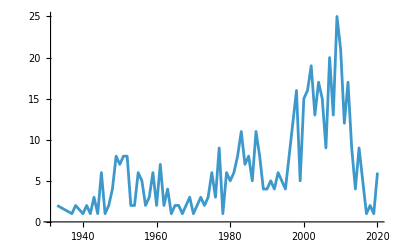

```mathematica
ListPlot[yearlist//ToExpression,PlotRange->Full,Joined->True]
```

### あらためて各主要論文の被引用の状況を確認する

最も古い主要論文は1933出版。

```mathematica
targetYears=Table[ToString[n],{n,1933,2020}]
```

{1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020}

```mathematica
(targetCandPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top1PcCitedArtPMID])//Length
```

536

PMIDからタイトルを引く

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];*)
```

```mathematica
(*(targetCandPMIDvsTitle=Map[{#,pmidToTitle[#]}&,top1PcCitedArtPMID])//Length*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"targetCandPMIDvsTitle.save",targetCandPMIDvsTitle]*)
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"targetCandPMIDvsTitle.save"];
```

PMID vs. PMID

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/totalEdge.save"];*)
```

```mathematica
(*AbsoluteTiming[(top1PcCitedArtEdges=ParallelMap[Cases[totalEdgeList,DirectedEdge[_,#]]&,top1PcCitedArtPMID,Method->"FinestGrained"])//Length]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top1PcCitedArtEdges.save",top1PcCitedArtEdges]*)
```

以下はデータ整形

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top1PcCitedArtEdges.save"];
```

```mathematica
(top1PcCitedArtCitedyear= Map[{PMIDtoPubyear[#[[1]]],{PMIDtoPubyear[#[[2]]],#[[2]]}}&, top1PcCitedArtEdges,{2}])//Length
```

536

yearごとの被引用数リストを作る

：yearから被引用数を得る

```mathematica
toCitedyearlist[l_]:=Module[{citedPMID},
citedPMID=l[[1,2]];
{citedPMID,Association[MapApply[Rule,Tally[Map[#[[1]]&,l]]]]}
]
```

```mathematica
(top1PcCitedArtCitedyearAssociations=Map[toCitedyearlist,top1PcCitedArtCitedyear])//Length
```

536

```mathematica
top1PcCitedArtCitedyearAssociations[[1]]
```

{{1996,10062328},<|2002→1,2003→3,2004→5,2005→8,2006→11,2007→21,2008→32,2009→54,2010→57,2011→84,2012→121,2013→227,2014→271,2015→450,2016→638,2017→770,2018→832,2019→1027,2020→1208,2021→1450,2022→1805,2023→1791,2024→3|>}

：1993からの被引用数リストにする

```mathematica
fromAscToCount[asc_,year_]:=Map[asc[#]&,year]/.{_Missing->0}
```

```mathematica
fromAscToCount[top1PcCitedArtCitedyearAssociations[[1]][[2]],targetYears]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,3,5,8,11,21,32,54,57,84,121,227,271,450,638,770,832,1027,1208}

<1993からの被引用数リスト>

```mathematica
(top1PcCitedArtCitedCount["1933-2020"]=Map[{#[[1]],fromAscToCount[#[[2]],targetYears]}&,top1PcCitedArtCitedyearAssociations])//Length
```

536

：出版年からの被引用数リストにする

```mathematica
fromPY[l_,y_]:=Module[{py,pyp},
py=l[[1,1]];
pyp=Flatten[Position[y,py]][[1]];
{l[[1]],l[[2]][[pyp;;]]}
]
```

```mathematica
fromPY[top1PcCitedArtCitedCount["1933-2020"][[2]],targetYears]
```

{{1998,10069079},{0,6,34,70,107,149,184,191,223,282,320,316,351,406,428,496,523,512,572,634,573,616,607}}

```mathematica
(top1PcCitedArtCitedCount["PY-2020"]=Map[fromPY[#,targetYears]&,top1PcCitedArtCitedCount["1933-2020"]])//Length
```

536

### 分析

#### OA論文か？

PMCのIDがあればOAとみなす

```mathematica
Import["/Volumes/elecom/BANK/pubmed/202312/xml/element/id/integID.wl"];
```

```mathematica
idsAsc//Length
```

325352

```mathematica
isPMC[id_String]:=If[Position[idsAsc[id],"pmc"]=={},id->0,id->1]
```

```mathematica
GroupBy[Map[isPMC,top1PcCitedArtPMID],Last]
```

<|0→{10062328→0,10069079→0,10075613→0,10102814→0,10109801→0,10547847→0,10592173→0,10592235→0,10638745→0,10647931→0,10655437→0,10789670→0,10797032→0,10802651→0,10827456→0,10829079→0,10835412→0,10963602→0,1105573→0,11130711→0,11152613→0,11181995→0,11209064→0,11234459→0,11237011→0,11253156→0,11283309→0,11309499→0,11328886→0,11368702→0,11373684→0,11498575→0,11524383→0,11553815→0,11556941→0,11689955→0,1172191→0,11752295→0,1175627→0,11771995→0,11823860→0,11832527→0,11846609→0,11904577→0,11932250→0,1195397→0,11994752→0,1202204→0,12045153→0,12068308→0,12111919→0,12117397→0,12130773→0,12184808→0,12297042→0,12377157→0,12391568→0,1244564→0,12466850→0,12485966→0,12490959→0,12538238→0,12629218→0,12734009→0,12748199→0,12824337→0,12883005→0,12900694→0,12912839→0,12925520→0,12958120→0,12989928→0,12991232→0,12991237→0,12996882→0,13069686→0,13124776→0,13130792→0,13186838→0,13249955→0,13262900→0,13267987→0,13276348→0,13278318→0,13286333→0,13293190→0,13298683→0,13319380→0,13428781→0,13475399→0,13563554→0,13610928→0,13610936→0,13641241→0,13650640→0,13655060→0,13671378→0,13672998→0,13675766→0,13688369→0,13718526→0,13726518→0,13764136→0,13767412→0,13772379→0,13910995→0,13944428→0,13975866→0,13986422→0,1400587→0,14097352→0,14240539→0,14287192→0,14381428→0,14381429→0,14399272→0,14450081→0,14454024→0,14474176→0,14530136→0,14597658→0,14656957→0,14744438→0,14772207→0,14775715→0,14794694→0,14803635→0,14822727→0,14848424→0,14862161→0,14873923→0,14898516→0,14907661→0,14907713→0,149110→0,14915960→0,14927572→0,14927794→0,14938350→0,15034147→0,15102499→0,15111519→0,15118073→0,15118125→0,15173120→0,15175435→0,15223320→0,15260895→0,15264254→0,15273542→0,15297300→0,15299374→0,15299926→0,15372042→0,15392854→0,15395398→0,15395569→0,15398090→0,15398551→0,15404816→0,15410483→0,15421999→0,15436457→0,15461798→0,15501092→0,1555235→0,15572765→0,15652477→0,15758009→0,15761078→0,15817019→0,1593914→0,15939837→0,15944708→0,15969739→0,16055882→0,16056220→0,16081474→0,16199517→0,16204405→0,16222654→0,16255080→0,16497588→0,16561366→0,16595758→0,16646809→0,16654194→0,16694480→0,16694558→0,16695228→0,16695286→0,16695568→0,16745305→0,16746620→0,16747230→0,16747456→0,16747508→0,16747652→0,16747674→0,16747784→0,16747907→0,16747948→0,16748220→0,16748273→0,16748381→0,16820507→0,16862161→0,16904174→0,16923388→0,16923606→0,16928733→0,16991506→0,16991878→0,16994401→0,17183312→0,17237035→0,17247100→0,17247150→0,17320507→0,17483113→0,17486113→0,17488738→0,17512414→0,17554300→0,17586664→0,1759558→0,17618441→0,17634462→0,17681537→0,17695343→0,17701901→0,17751251→0,17760012→0,17846036→0,17872937→0,1798888→0,17996036→0,18016252→0,18029452→0,18035408→0,18128147→0,18156677→0,18261238→0,18287387→0,18349386→0,18485877→0,18516045→0,1852778→0,18546601→0,18650514→0,18650914→0,18772890→0,18798982→0,18839484→0,18929686→0,19015660→0,19029910→0,19033363→0,19097774→0,19114008→0,19131956→0,19167326→0,19171970→0,19246619→0,19261174→0,19289445→0,19325852→0,1932883→0,19346325→0,19414839→0,19451168→0,19460998→0,19461840→0,19474385→0,19487818→0,19499576→0,19505943→0,19565683→0,19621072→0,19622511→0,19622551→0,19801464→0,19805654→0,19812666→0,19910308→0,19945376→0,20003500→0,20057044→0,20080505→0,20110278→0,20124692→0,20124702→0,2025413→0,20354512→0,20383002→0,20383131→0,20436464→0,20513432→0,20525638→0,20525992→0,20601685→0,20610543→0,20644199→0,20709691→0,20979621→0,20981092→0,21221095→0,21296855→0,21351269→0,21376230→0,21460441→0,21478889→0,21546353→0,21572440→0,21700674→0,21816040→0,2188735→0,21959131→0,21988835→0,2199796→0,22008217→0,22237781→0,2231712→0,22357727→0,22383036→0,22388286→0,22437870→0,22506599→0,22543367→0,22588877→0,22658127→0,22743772→0,22745249→0,22820204→0,22930834→0,22955616→0,23000897→0,23104886→0,23128226→0,23193283→0,23245604→0,23287718→0,23329690→0,23335087→0,23550210→0,23618408→0,236308→0,24132122→0,24141714→0,2439888→0,24399786→0,2440339→0,24451623→0,2448875→0,2449095→0,24695404→0,24889800→0,2513255→0,25220842→0,25260700→0,25516281→0,25554246→0,25559415→0,25567568→0,25605792→0,25651787→0,25741868→0,26432245→0,265521→0,2659436→0,26742998→0,26808342→0,26903338→0,27004904→0,271968→0,2744487→0,2748771→0,27535533→0,27754618→0,28055103→0,28561359→0,2868172→0,291033→0,29313949→0,2985470→0,2999980→0,30207593→0,3047011→0,30620402→0,3162770→0,31978945→0,31986264→0,32007143→0,320200→0,3203132→0,32031570→0,32109013→0,32171076→0,322279→0,3323813→0,3327686→0,3344216→0,3358796→0,3397865→0,344137→0,3447015→0,3537305→0,3558716→0,3616518→0,3670292→0,36810→0,3692487→0,3714490→0,3798106→0,3802833→0,3806354→0,3838314→0,3843705→0,3881765→0,388356→0,388439→0,3899825→0,3928249→0,4179068→0,4202581→0,4291934→0,4326772→0,4337382→0,4366476→0,4504350→0,4561027→0,4598299→0,4705382→0,4850204→0,4887011→0,4896022→0,4956917→0,5146491→0,518835→0,5432063→0,5700707→0,5806584→0,5962951→0,5963888→0,603028→0,6091052→0,6159641→0,6166661→0,6198242→0,6232463→0,6235151→0,6246368→0,6253831→0,6260957→0,6266278→0,6269464→0,6270629→0,6286831→0,6295879→0,6295880→0,6310323→0,6310324→0,6312838→0,6326095→0,6329026→0,6329717→0,6336730→0,6345791→0,6546423→0,6606682→0,6610841→0,6667333→0,6668417→0,6791577→0,6828386→0,6880820→0,6960240→0,7063747→0,7108955→0,7138600→0,7219534→0,7463489→0,7494007→0,773363→0,7786990→0,7814313→0,7984236→0,7984417→0,8223268→0,8242752→0,8252621→0,8254673→0,8366922→0,8421494→0,843571→0,8520220→0,8524021→0,8589427→0,8628042→0,8721797→0,8744570→0,8744573→0,8779443→0,8812068→0,881736→0,8902363→0,9176952→0,9177342→0,922889→0,9254694→0,9278503→0,9305837→0,9310563→0,9367129→0,9396791→0,942051→0,9486653→0,9504803→0,9521319→0,9521921→0,9521922→0,9623998→0,9634230→0,9717241→0,9742976→0,9757107→0,9759494→0,9804556→0,9843981→0,9881538→0,9887164→0,9916792→0,9918953→0,9931268→0,9944570→0},1→{9023104→1}|>

#### 指標値

"len" => 出版から2020までの年数
“peakYear” => 出版からピークを迎えるまでの年数☑️
“peakCount” => ピークの年の被引用数☑️
“peakRatio” => peakCount/decayCited（”活動期間”の被引用）
“peakPosition” => “活動期間”中におけるpeakの位置（全体を1とする）
“sustainYear” => ピークの年から2020までの年数
“decayYear” => ピークの年を超えてから年間引用が全体の引用の5%以下となるまでの出版からの年数☑️
“decayCited” => decayYearまでの被引用数☑️
“firstCitedYear” => 最初の引用が発生するまでの年数（出版年に発生すると0）
“totalCited” => 出版年から2020までの総被引用数
“V:Av5year” => 5年引用数平均の分散☑️
“V:diff” => 5年引用数平均の差分の分散（ゼロパディングあり=>出版年での立ち上がりが見える）☑️
“V:diff2” => 5年引用数平均の差分の差分の分散☑️
“diffTotal” => 5年引用数平均の差分の累計：十分に大きい値があり十分に長い期間があれば0に近づく

```mathematica
top1PcCitedArtCitedCount["PY-2020"]//Length
```

536

```mathematica
Accumulate[top1PcCitedArtCitedCount["PY-2020"][[1,2]]]
```

{0,0,0,0,0,0,1,4,9,17,28,49,81,135,192,276,397,624,895,1345,1983,2753,3585,4612,5820}

```mathematica
acRatio[l_]:=Module[{ac},
ac=Accumulate[l];
N[l/ac]/.Indeterminate->1
]
```

```mathematica
acRatio[top1PcCitedArtCitedCount["PY-2020"][[20,2]]]
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

{1,1.,0.646154,0.424779,0.303329,0.201772,0.14044,0.101141,0.10605,0.0840598,0.0716763,0.0673854,0.0734266,0.0636109,0.0585645,0.0580672,0.0481642,0.0408936,0.0385876,0.0411867,0.0340526}

```mathematica
peakP=Flatten[Position[top1PcCitedArtCitedCount["PY-2020"][[20,2]],Max[top1PcCitedArtCitedCount["PY-2020"][[20,2]]]]][[1]]
```

5

```mathematica
tmpP=Cases[Flatten[Position[acRatio[top1PcCitedArtCitedCount["PY-2020"][[20,2]]],x_/;x<=0.05]],x_/;x>peakP]
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

{17,18,19,20,21}

```mathematica
ndiff[l_,w_]:=BlockMap[(#[[-1]]-#[[1]])/(w-1)&,Join[Table[0,{w-1}],l],w,1]
```

```mathematica
ndiff[l_]:=BlockMap[(#[[-1]]-#[[1]])&,l,2,1]
```

```mathematica
myVar[l_]:=If[Length[l]>1,Variance[l],0]
```

```mathematica
basicStat[citedcount_]:=Module[{len,argPeak,peakYear,max,sustainYear,decayTH,decayPlist,decayCited,decayPeriod,firstCitedYear,total,Av5year,diff,diff2,diffTotal},
decayTH=0.05;
len=Length[citedcount];
argPeak=Flatten[Position[citedcount,max=Max[citedcount]]];
peakYear=argPeak[[1]];
sustainYear=len-argPeak[[-1]];
decayPlist=Cases[Flatten[Position[acRatio[citedcount],x_/;x<=decayTH]],x_/;x>peakYear];
decayCited=Total[citedcount[[;;Min[decayPlist]]]];
decayPeriod=Min[decayPlist]-peakYear;
If[Length[decayPlist]<=0,decayPeriod="InDecay"];
firstCitedYear=Min[Position[citedcount,x_/;x>0]]-1;
total=Total[citedcount];
Av5year=MovingAverage[Join[citedcount,Table[0,{n,4}]],5];
diff=ndiff[Av5year];
diff2=ndiff[diff];
diffTotal=Total[diff//N];
Association[{"len"->len,"peakYear"->peakYear,"peakCount"->max,"peakRatio"->max/decayCited//N,"peakPosition"->peakYear/Min[decayPlist]//N,"sustainYear"->sustainYear,"decayCited"->decayCited,"decayPeriod"->decayPeriod,"firstCitedYear"->firstCitedYear,"totalCited"->total,"V:Av5year"->myVar[Av5year//N],"V:diff"->myVar[diff//N],"V:diff2"->myVar[diff2//N],"diffTotal"->diffTotal,"diffSeq"->diff}]
]
```

```mathematica
toItemNormarizeMat[l_]:=Module[{m,key},
key=Keys[l[[1,2]]];
m=Map[Normal[#[[2]]]&,l]/.{None->0};
Transpose[Map[Normalize,Transpose[Map[#[[2]]&,m,{2}]]]//N]
]
```

```mathematica
totalize[l_]:=l/Total[l]
```

```mathematica
(bs=Map[{#[[1]],basicStat[#[[2]]]}&,top1PcCitedArtCitedCount["PY-2020"]])//Length
```

Power::infy: 無限式1/0が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

Part::span: 1;;∞は有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

536

#### 多峰性テスト(all)

外部（python）で行う。

：データ出力

```mathematica
outdir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload/

```mathematica
prefix="citedcount_"
```

citedcount_

```mathematica
(targetfiles=Map[outdir<>prefix<>#[[1,2]]<>".csv"&,top1PcCitedArtCitedCount["PY-2020"]])//Length
```

536

```mathematica
(*Do[Export[targetfiles[[n]],top1PcCitedArtCitedCount["PY-2020"][[n]][[2]]],{n,Length[top1PcCitedArtCitedCount["PY-2020"]]}]*)
```

：実行

% cd /Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload
% source ~/main/bin/activate
% for file in *csv; do python ./bin/peak_estimator.py -f $file -mc 5 -bw 1 > $file.out; done

：結果の回収

対象ファイルネームの生成とimport

```mathematica
(ret=Map[Import[#<>".out","Text"]&,targetfiles])//Length
```

536

計算されないものがあり $Failed がある。

```mathematica
(allMultimode=(Map[StringSplit[StringSplit[#,"\n"][[-1]],": "][[-1]]&,ret]//ToExpression))//Length
```

Part::partw: {}の部分-1は存在しません．

StringSplit::strse: 文字列あるいは文字列のリストがStringSplit[{}⟦-1⟧,: ]の位置1に想定されています．

Part::partw: {}の部分-1は存在しません．

StringSplit::strse: 文字列あるいは文字列のリストがStringSplit[{}⟦-1⟧,: ]の位置1に想定されています．

Part::partw: {}の部分-1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

StringSplit::strse: 文字列あるいは文字列のリストがStringSplit[{}⟦-1⟧,: ]の位置1に想定されています．

General::stop: この計算中に，StringSplit::strseのこれ以上の出力は表示されません．

ToExpression::sntx: 無効な文法が": "の中あるいはその前にあります．
                            ^

General::stop: この計算中に，ToExpression::sntxのこれ以上の出力は表示されません．

536

```mathematica
allMultimodePos=Flatten[Position[allMultimode,2]]
```

{77,124,131,232,233,484,512}

```mathematica
allSinglemodePos=Flatten[Position[allMultimode,1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,125,126,127,128,129,130,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,381,382,383,385,386,388,390,394,395,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536}

#### plot用カラー/サイズ定義

以下はplotの色の調整

```mathematica
myColor1[z_]:=RGBColor[z,0.8(1-z),0.4(1-z)];
myColor2[z_]:=CMYKColor[z,((1-z)/3)^2,((1-z)/2)^2,Sqrt[z]];
myColor3[z_]:=CMYKColor[((1-z)/3)^2,z,((1-z)/2)^2,Sqrt[z]];
myColor4[z_]:=CMYKColor[((1-z)/3)^2,((1-z)/3)^2,z,Sqrt[z]];
myColor5[z_]:=CMYKColor[(z)^2,(z),(z),(z)^(1.2)];
myColor6[z_]:=Blend[{Red,Green,White},{1,0.75(1-z),(1-z)^(3)}];
cf1=Function[{x,y,z},Hue[5/6 (1-z),0.3+(z^2),1]];
cf2=Function[{x,y,z},Hue[5/6 (1-z),#+(1-#)*z,1]&@0.05];
cf3=Function[{x,y,z},Hue[5/6*(1-z),(#1+(1-#1)*z)^#2,1]]&@@{.25(*offset*),1.0(*gain*)};
```

```mathematica
imsz1=260
imsz2=320
imsz3=480
imsz4=540
```

260

320

480

540

#### オブソレッセンスSelection(3)

十分にオブソレッセンスがみられるものだけを抽出する。

・出版から十分な時間が経過している：”len”が十分に長い(10年以上)
・ピーク期が十分に過ぎ去っている：“decayPeriod”が“peakYear”以上
・被引用の傾向が十分に低下している：“decayPeriod”が”InDicay”でない（peakYear以降かつ当該年の引用数が当該年までの引用数の5%以下となる年のうち最も古い）

```mathematica
(obsolatedPos3=Flatten[Position[bs,x_/;x[[2]]["len"]>=10&&x[[2]]["decayPeriod"]>=x[[2]]["peakYear"]&&x[[2]]["decayPeriod"]!="InDecay"]])//Length
```

Part::partd: 部分指定List⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: ∞の部分2は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

77

```mathematica
(nonobsolatedPos3=Complement[Table[n,{n,Length[bs]}],obsolatedPos3])//Length
```

459

多峰性を持つpos

```mathematica
obsmultiPos3=Intersection[allMultimodePos,obsolatedPos3]
```

{77,232,233,484,512}

```mathematica
obsolated3=top1PcCitedArtCitedCount["PY-2020"][[obsolatedPos3]];
```

```mathematica
obsolatedSort3["PY"]=SortBy[obsolated3,#[[1,1]]&];
```

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"出版後の年数","出版後の年数による論文順位","被引用数"},ColorFunction->myColor2]
```

-Graphics3D-

チャンピオン論文がObsolateか確認する：

```mathematica
obsPMID=Association[Map[#[[1,2]]->#[[1,2]]&,bs[[obsolatedPos3]]]]
```

<|11130711→11130711,11181995→11181995,11373684→11373684,1175627→1175627,12466850→12466850,12989928→12989928,12991232→12991232,12996882→12996882,13069686→13069686,13124776→13124776,13186838→13186838,13319380→13319380,13610936→13610936,13767412→13767412,13944428→13944428,1400587→1400587,14287192→14287192,14381428→14381428,14454024→14454024,14474176→14474176,14530136→14530136,14822727→14822727,14862161→14862161,14907661→14907661,149110→149110,15260895→15260895,15297300→15297300,15398551→15398551,1555235→1555235,16255080→16255080,16595758→16595758,16694480→16694480,16748220→16748220,16748273→16748273,16748381→16748381,17237035→17237035,17247150→17247150,17488738→17488738,17554300→17554300,17751251→17751251,17760012→17760012,18016252→18016252,18156677→18156677,18287387→18287387,1852778→1852778,19171970→19171970,19325852→19325852,19474385→19474385,20610543→20610543,20981092→20981092,21546353→21546353,2199796→2199796,2448875→2448875,2449095→2449095,265521→265521,2659436→2659436,2999980→2999980,3162770→3162770,320200→320200,344137→344137,6091052→6091052,6159641→6159641,6232463→6232463,6246368→6246368,6260957→6260957,6266278→6266278,6269464→6269464,6286831→6286831,6295879→6295879,6295880→6295880,6310323→6310323,6329026→6329026,6791577→6791577,7494007→7494007,773363→773363,8242752→8242752,9278503→9278503|>

結果はいずれもObsolateでない：

```mathematica
Map[{pmidToTitle[#],#,obsPMID[#]}&, chanpionPMID]
```

{{Qualitative analysis of proteins: a partition chromatographic method using paper.,16747784,Missing[KeyAbsent,16747784]},{Qualitative analysis of proteins: a partition chromatographic method using paper.,16747784,Missing[KeyAbsent,16747784]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,5432063,Missing[KeyAbsent,5432063]},{Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,5432063,Missing[KeyAbsent,5432063]}}

#### Selection (3)におけるチャンピオン論文のオブソレッセンス状態

```mathematica
pmidtobs=Association[Map[#[[1,2]]->#&,bs]];
```

```mathematica
Union[chanpionPMID]
```

{14907713,16747784,5432063}

```mathematica
chanpionPMIDunion={"16747784","14907713","5432063"}
```

{16747784,14907713,5432063}

```mathematica
chanpionPlotTitleunion={"Qualitative analysis of ...","Protein measurement with ...","Cleavage of structural proteins ..."}
```

{Qualitative analysis of ...,Protein measurement with ...,Cleavage of structural proteins ...}

```mathematica
chanpionPlotTitleunionP={"Qualitative analysis of ... (1944)","Protein measurement with ... (1951)","Cleavage of structural proteins ... (1970)"}
```

{Qualitative analysis of ... (1944),Protein measurement with ... (1951),Cleavage of structural proteins ... (1970)}

```mathematica
tmpT=Map[pmidtobs,chanpionPMIDunion]
```

{{{1944,16747784},<|len→77,peakYear→9,peakCount→23,peakRatio→0.129944,peakPosition→0.642857,sustainYear→68,decayCited→177,decayPeriod→5,firstCitedYear→0,totalCited→236,V:Av5year→28.3951,V:diff→1.20154,V:diff2→0.604079,diffTotal→-7.,diffSeq→{21/5,18/5,17/5,3,-7/5,-8/5,-11/5,-6/5,-19/5,-7/5,-7/5,-1,-11/5,-2/5,1/5,-3/5,-4/5,-2/5,1/5,-1,-3/5,1/5,-1/5,-3/5,-1/5,0,-3/5,0,1/5,1/5,-1/5,0,0,-1/5,-1/5,0,1/5,0,0,0,1/5,-1/5,0,0,0,-1/5,0,0,0,0,0,0,0,1/5,1/5,0,0,0,-1/5,0,1/5,1/5,0,0,-1/5,-1/5,0,1/5,1/5,1/5,1/5,-1/5,-1/5,-1/5,-1/5,-1/5}|>},{{1951,14907713},<|len→70,peakYear→28,peakCount→1740,peakRatio→0.0585012,peakPosition→0.736842,sustainYear→42,decayCited→29743,decayPeriod→10,firstCitedYear→1,totalCited→53050,V:Av5year→256971.,V:diff→5510.1,V:diff2→605.608,diffTotal→147.8,diffSeq→{24/5,36/5,38/5,48/5,68/5,81/5,98/5,112/5,30,192/5,234/5,316/5,398/5,79,453/5,574/5,601/5,577/5,683/5,127,614/5,588/5,122,392/5,171/5,-28/5,-10,-47,-86/5,-44/5,-48/5,-153/5,-101/5,-233/5,-233/5,-59,-341/5,-374/5,-389/5,-316/5,-437/5,-549/5,-544/5,-501/5,-521/5,-377/5,-198/5,-73/5,-138/5,1,26,94/5,174/5,267/5,246/5,319/5,367/5,294/5,327/5,38,0,-39/5,-117/5,-30,-88/5,-791/5,-771/5,-764/5,-778/5}|>},{{1970,5432063},<|len→51,peakYear→23,peakCount→2261,peakRatio→0.0701194,peakPosition→0.821429,sustainYear→28,decayCited→32245,decayPeriod→5,firstCitedYear→0,totalCited→54249,V:Av5year→380198.,V:diff→12712.1,V:diff2→1212.23,diffTotal→133.,diffSeq→{116/5,29,282/5,63,461/5,572/5,677/5,669/5,799/5,898/5,942/5,972/5,191,165,723/5,548/5,448/5,67,109/5,-208/5,-171/5,-511/5,-744/5,-748/5,-749/5,-1007/5,-747/5,-621/5,-476/5,-367/5,-186/5,-249/5,-11,92/5,83/5,133/5,293/5,243/5,153/5,173/5,44/5,-21,-42,-306/5,-248/5,-168/5,-186,-874/5,-817/5,-843/5}|>}}

```mathematica
jobsItemName={"論文タイトル","最大被引用を得るまでの期間","減衰期間","最大被引用数（年間）","減衰年の被引用数","被引用数分散","被引用速度の分散","被引用か速度の分散"}
```

{論文タイトル,最大被引用を得るまでの期間,減衰期間,最大被引用数（年間）,減衰年の被引用数,被引用数分散,被引用速度の分散,被引用か速度の分散}

```mathematica
obsItemName={"Title","Peak period\n(year)","Decay period\n(year)","Peak count","Decay cited","Variance:cited","Variance:diff","Variance:diff-accel"}
```

{Title,Peak period
(year),Decay period
(year),Peak count,Decay cited,Variance:cited,Variance:diff,Variance:diff-accel}

```mathematica
obsValue=Map[{#[[2]]["peakYear"],#[[2]]["decayPeriod"],#[[2]]["peakCount"],#[[2]]["decayCited"],Round[#[[2]]["V:Av5year"],0.1],Round[#[[2]]["V:diff"],0.1],Round[#[[2]]["V:diff2"],0.1]}&,tmpT]
```

{{9,5,23,177,28.4,1.2,0.6},{28,10,1740,29743,256971.,5510.1,605.6},{23,5,2261,32245,380198.,12712.1,1212.2}}

```mathematica
obsValueT=Map[Flatten,{chanpionPlotTitleunion,obsValue}//Transpose]
```

{{Qualitative analysis of ...,9,5,23,177,28.4,1.2,0.6},{Protein measurement with ...,28,10,1740,29743,256971.,5510.1,605.6},{Cleavage of structural proteins ...,23,5,2261,32245,380198.,12712.1,1212.2}}

オブソレッセンスに関する諸元表：

```mathematica
Prepend[obsValueT,obsItemName]//TableForm
```

Title | Peak period
(year) | Decay period
(year) | Peak count | Decay cited | Variance:cited | Variance:diff | Variance:diff-accel
Qualitative analysis of ... | 9 | 5 | 23 | 177 | 28.4 | 1.2 | 0.6
Protein measurement with ... | 28 | 10 | 1740 | 29743 | 256971. | 5510.1 | 605.6
Cleavage of structural proteins ... | 23 | 5 | 2261 | 32245 | 380198. | 12712.1 | 1212.2

```mathematica
TABmcpapers=Prepend[obsValueT,jobsItemName]//TableForm
```

論文タイトル | 最大被引用を得るまでの期間 | 減衰期間 | 最大被引用数（年間） | 減衰年の被引用数 | 被引用数分散 | 被引用速度の分散 | 被引用か速度の分散
Qualitative analysis of ... | 9 | 5 | 23 | 177 | 28.4 | 1.2 | 0.6
Protein measurement with ... | 28 | 10 | 1740 | 29743 | 256971. | 5510.1 | 605.6
Cleavage of structural proteins ... | 23 | 5 | 2261 | 32245 | 380198. | 12712.1 | 1212.2

```mathematica
(*Export[exportdocdir<>"TABmcpapers.tex",TABmcpapers,"TeXFragment"]*)
```

```mathematica
chanpionArtPointlist=DeleteCases[(Map[(#[[2]]//Normal)/.{Rule->List}&,top1PcCitedArtCitedyearAssociations[[{200,134,440}]]]//ToExpression),{2024,_},-1]
```

{{{1944,1},{1945,4},{1946,3},{1947,8},{1948,19},{1949,22},{1950,22},{1951,20},{1952,23},{1953,12},{1954,14},{1955,11},{1956,14},{1957,4},{1958,5},{1959,7},{1960,6},{1961,3},{1962,2},{1963,6},{1964,4},{1965,2},{1966,1},{1967,3},{1968,1},{1969,1},{1970,3},{1974,1},{1977,1},{1978,1},{1985,1},{1989,1},{2002,1},{2003,1},{2008,1},{2009,1},{2010,1},{2015,1},{2016,1},{2017,1},{2018,1},{2019,1},{2021,2},{2022,2},{2023,2}},{{1952,1},{1953,5},{1954,13},{1955,24},{1956,24},{1957,37},{1958,43},{1959,61},{1960,92},{1961,105},{1962,135},{1963,155},{1964,211},{1965,284},{1966,339},{1967,451},{1968,553},{1969,606},{1970,737},{1971,913},{1972,1052},{1973,1130},{1974,1289},{1975,1372},{1976,1527},{1977,1640},{1978,1740},{1979,1681},{1980,1543},{1981,1499},{1982,1590},{1983,1505},{1984,1595},{1985,1499},{1986,1451},{1987,1437},{1988,1404},{1989,1362},{1990,1266},{1991,1156},{1992,1096},{1993,1030},{1994,973},{1995,950},{1996,719},{1997,547},{1998,486},{1999,472},{2000,429},{2001,342},{2002,349},{2003,413},{2004,334},{2005,434},{2006,472},{2007,443},{2008,587},{2009,601},{2010,680},{2011,791},{2012,810},{2013,881},{2014,928},{2015,870},{2016,791},{2017,771},{2018,764},{2019,778},{2020,782},{2021,792},{2022,805},{2023,771}},{{1970,1},{1971,7},{1972,20},{1973,54},{1974,77},{1975,117},{1976,152},{1977,302},{1978,369},{1979,538},{1980,689},{1981,829},{1982,971},{1983,1168},{1984,1436},{1985,1631},{1986,1801},{1987,1926},{1988,1993},{1989,2159},{1990,2179},{1991,2249},{1992,2261},{1993,2102},{1994,1951},{1995,2008},{1996,1738},{1997,1517},{1998,1354},{1999,1202},{2000,1001},{2001,991},{2002,896},{2003,878},{2004,835},{2005,815},{2006,742},{2007,841},{2008,970},{2009,918},{2010,948},{2011,1035},{2012,1084},{2013,1123},{2014,1091},{2015,992},{2016,930},{2017,874},{2018,817},{2019,843},{2020,824},{2021,863},{2022,804},{2023,665}}}

被引用推移のplot図：

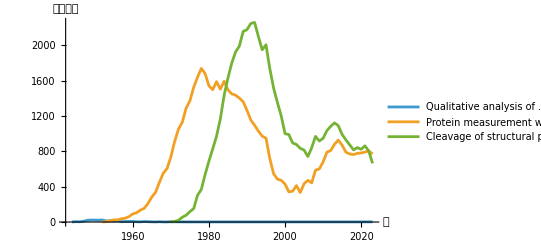

```mathematica
ListLinePlot[chanpionArtPointlist,PlotLegends->chanpionPlotTitleunionP,AxesLabel->{"年","被引用数"}]
```

```mathematica
ListLinePlot[chanpionArtPointlist,PlotLabels->chanpionPlotTitleunionP,AxesLabel->{"年","被引用数"}]
```

-Graphics-

```mathematica
chanpionPlotTitleunionAT= Placed[chanpionPlotTitleunionP,Above]
```

Placed[{Qualitative analysis of ... (1944),Protein measurement with ... (1951),Cleavage of structural proteins ... (1970)},Above]

```mathematica
ListLinePlot[chanpionArtPointlist,PlotLabels->chanpionPlotTitleunionAT,AxesLabel->{"年","被引用数"},PlotRange->{{1940,2025},All}]
```

-Graphics-

#### 指標plot(all)

```mathematica
bs//Length
```

536

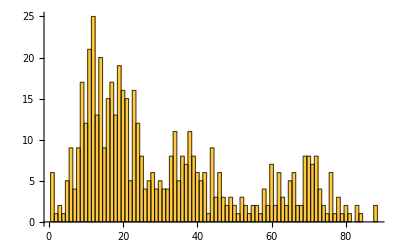

```mathematica
Histogram[Map[#[[2]]["len"]&,bs],{1},PlotRange->Full]
```

```mathematica
Map[#[[2]]["len"]&,bs]//Max
Map[#[[2]]["len"]&,bs]//Min
```

88

1

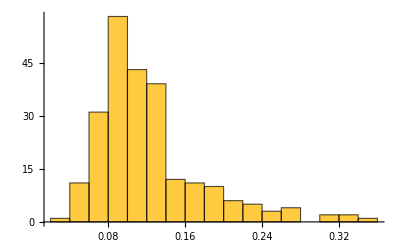

```mathematica
Histogram[Map[#[[2]]["peakRatio"]&,bs],PlotRange->Full]
```

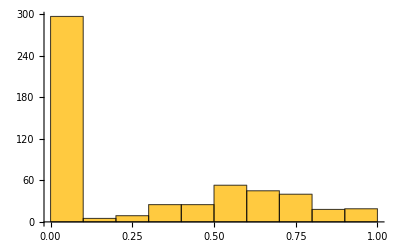

```mathematica
Histogram[Map[#[[2]]["peakPosition"]&,bs],PlotRange->Full]
```

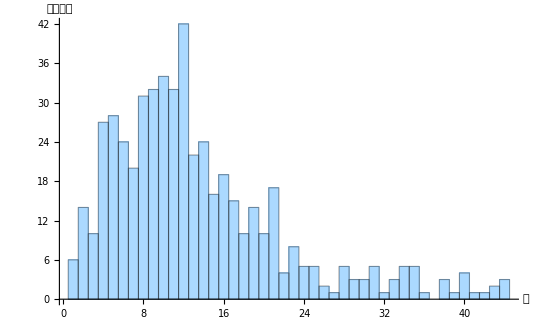

```mathematica
hi["peakYear","all"]=Labeled[Histogram[Map[#[[2]]["peakYear"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->imsz4],"1 出版からピークまで"]
```

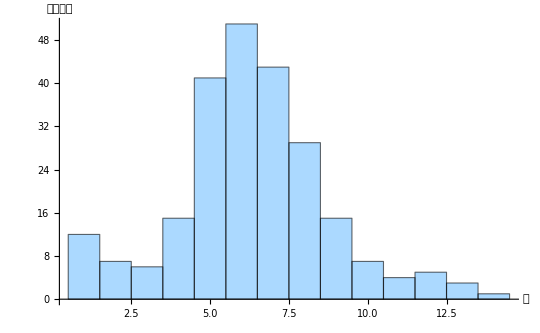

```mathematica
hi["decayPeriod","all"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->imsz4],"2 ピークから減衰まで"]
```

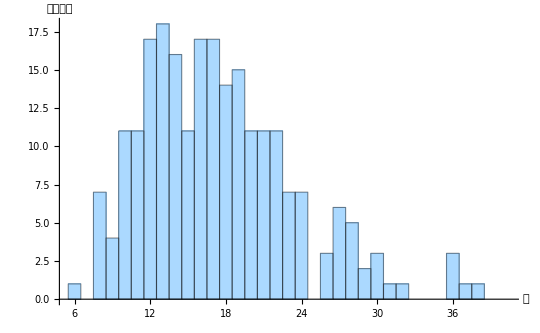

```mathematica
hi["activePeriod","all"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->imsz4],"3 出版から減衰まで"]
```

"InDecay" のカウント

```mathematica
Cases[Map[#[[2]]["decayPeriod"]&,bs],_String]//Length
```

297

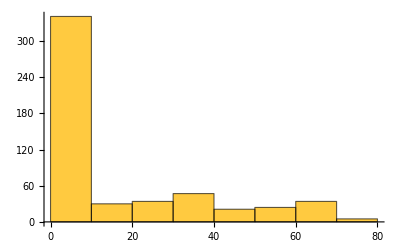

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,bs]]
```

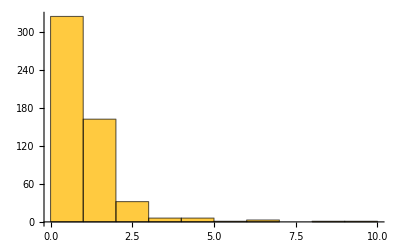

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,bs]]
```

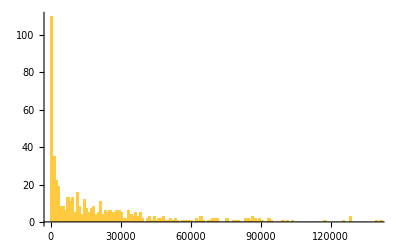

```mathematica
Histogram[Map[#[[2]]["V:Av5year"]&,bs],{1000}]
```

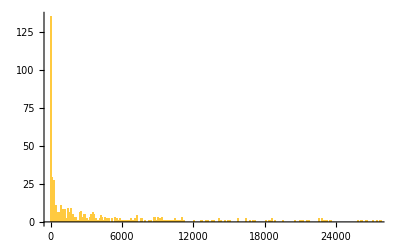

```mathematica
Histogram[Map[#[[2]]["V:diff"]&,bs],{100}]
```

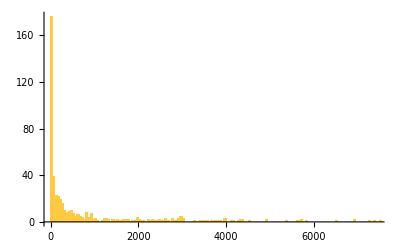

```mathematica
Histogram[Map[#[[2]]["V:diff2"]&,bs],{50}]
```

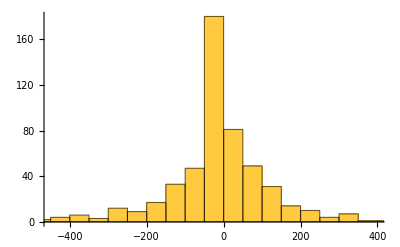

```mathematica
Histogram[Map[#[[2]]["diffTotal"]&,bs]]
```

#### 指標plot(obs/selection 3)

```mathematica
bs//Length
```

536

```mathematica
(obsbs3=bs[[obsolatedPos3]])//Length
```

77

```mathematica
Keys[obsbs3[[1,2]]]
```

{len,peakYear,peakCount,peakRatio,peakPosition,sustainYear,decayCited,decayPeriod,firstCitedYear,totalCited,V:Av5year,V:diff,V:diff2,diffTotal,diffSeq}

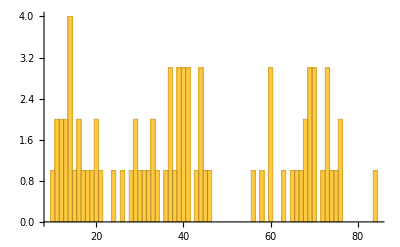

```mathematica
Histogram[Map[#[[2]]["len"]&,obsbs3],{1}]
```

```mathematica
Map[#[[2]]["len"]&,obsbs3]//Max
Map[#[[2]]["len"]&,obsbs3]//Min
```

84

10

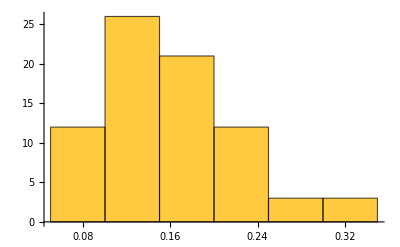

```mathematica
Histogram[Map[#[[2]]["peakRatio"]&,obsbs3],PlotRange->Full]
```

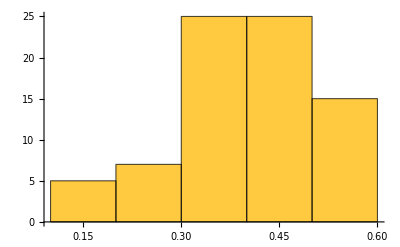

```mathematica
Histogram[Map[#[[2]]["peakPosition"]&,obsbs3],PlotRange->Full]
```

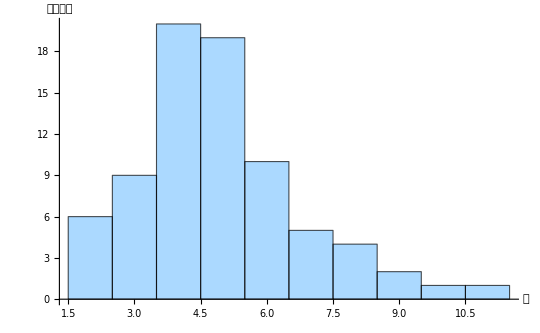

```mathematica
hi["peakYear","obs"]=Labeled[Histogram[Map[#[[2]]["peakYear"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"1 出版からピークまで（n=77）"]
```

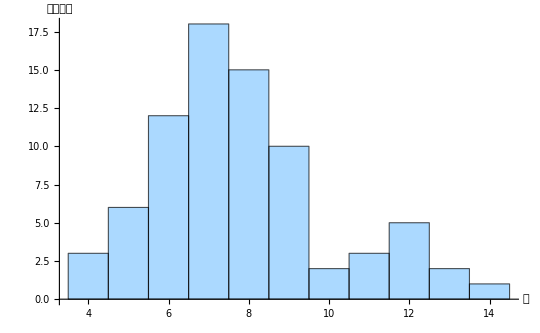

```mathematica
hi["decayPeriod","obs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"2 ピークから減衰まで（n=77）"]
```

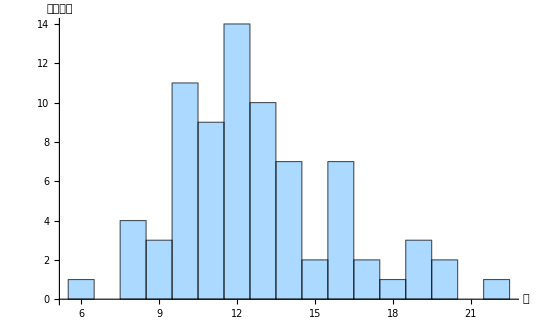

```mathematica
hi["activePeriod","obs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"3 出版から減衰まで（n=77）"]
```

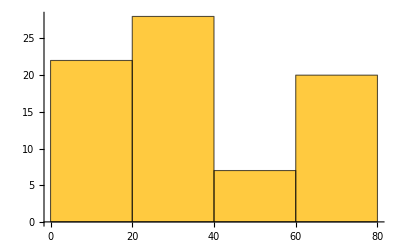

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,obsbs3]]
```

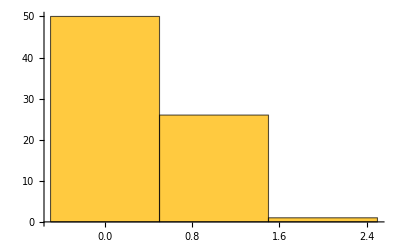

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,obsbs3]]
```

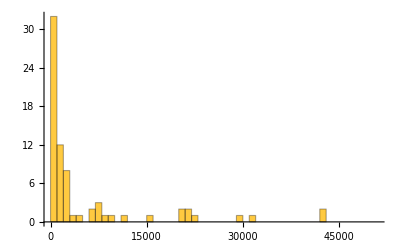

```mathematica
Histogram[Map[#[[2]]["V:Av5year"]&,obsbs3],{1000}]
```

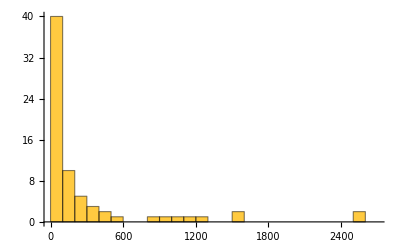

```mathematica
Histogram[Map[#[[2]]["V:diff"]&,obsbs3],{100}]
```

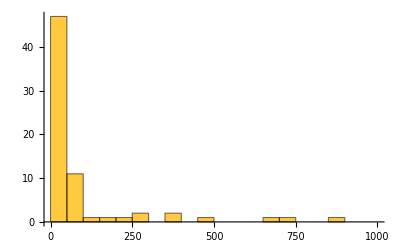

```mathematica
Histogram[Map[#[[2]]["V:diff2"]&,obsbs3],{50}]
```

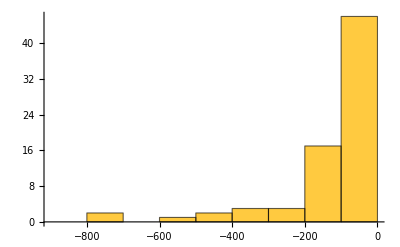

```mathematica
Histogram[Map[#[[2]]["diffTotal"]&,obsbs3]]
```

#### 指標plot(nonobs/selection 3)

```mathematica
bs//Length
```

536

```mathematica
(nonobsbs3=bs[[nonobsolatedPos3]])//Length
```

459

```mathematica
Keys[nonobsbs3[[1,2]]]
```

{len,peakYear,peakCount,peakRatio,peakPosition,sustainYear,decayCited,decayPeriod,firstCitedYear,totalCited,V:Av5year,V:diff,V:diff2,diffTotal,diffSeq}

```mathematica
Map[#[[2]]["len"]&,nonobsbs3]//Length
```

459

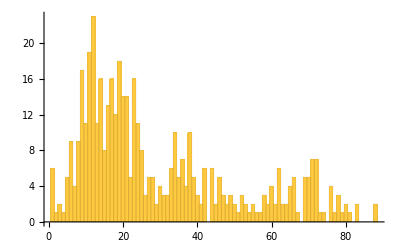

```mathematica
Histogram[Map[#[[2]]["len"]&,nonobsbs3],{1}]
```

```mathematica
Map[#[[2]]["len"]&,nonobsbs3]//Max
Map[#[[2]]["len"]&,nonobsbs3]//Min
```

88

1

```mathematica
Cases[Map[#[[2]]["peakYear"]&,nonobsbs3],_Integer]//Length
```

459

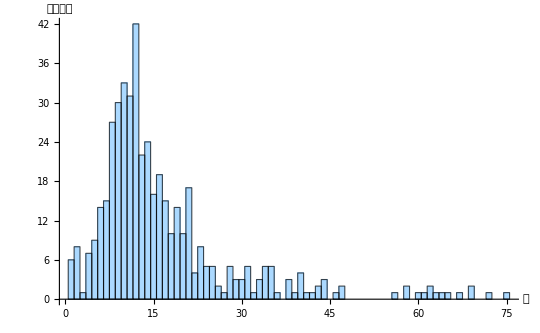

```mathematica
hi["peakYear","nonobs"]=Labeled[Histogram[Map[#[[2]]["peakYear"]&,nonobsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"1 出版からピークまで（n=459）"]
```

```mathematica
Cases[Map[#[[2]]["decayPeriod"]&,nonobsbs3],_Integer]//Length
```

162

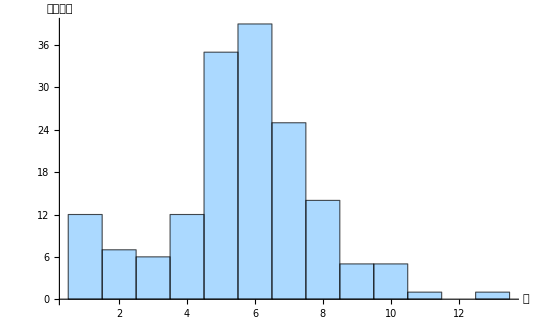

```mathematica
hi["decayPeriod","nonobs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,nonobsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"2 ピークから減衰まで（n=162）"]
```

```mathematica
Cases[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,nonobsbs3],_Integer]//Length
```

162

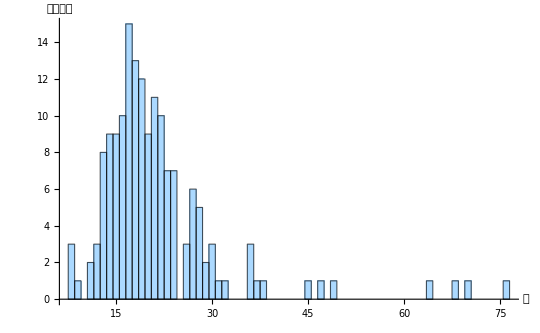

```mathematica
hi["activePeriod","nonobs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,nonobsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"3 出版から減衰まで（n=162）"]
```

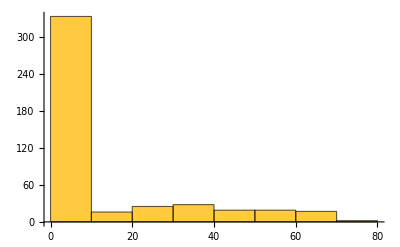

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,nonobsbs3]]
```

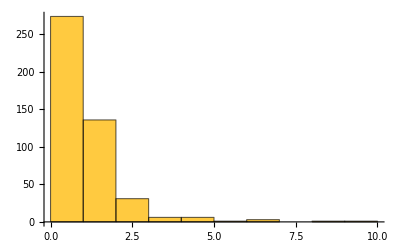

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,nonobsbs3]]
```

#### 指標plot tbl (all + selection 3)

```mathematica
tbl["index plot"]={{"高被引用論文全体",hi["peakYear","all"],hi["decayPeriod","all"],hi["activePeriod","all"]},
{"オブソレッセンス状態\nにある論文のみ",hi["peakYear","obs"],hi["decayPeriod","obs"],hi["activePeriod","obs"]}
}//TableForm
```

高被引用論文全体 | -Graphics- | -Graphics- | -Graphics-
オブソレッセンス状態
にある論文のみ | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export[exportdocdir<>"obsindex1-1.eps",hi["peakYear","all"]]
Export[exportdocdir<>"obsindex1-2.eps",hi["decayPeriod","all"]]
Export[exportdocdir<>"obsindex1-3.eps",hi["activePeriod","all"]]
Export[exportdocdir<>"obsindex2-1.eps",hi["peakYear","obs"]]
Export[exportdocdir<>"obsindex2-2.eps",hi["decayPeriod","obs"]]
Export[exportdocdir<>"obsindex2-3.eps",hi["activePeriod","obs"]]*)
```

#### 指標plot tbl ((obs + nonobs)/selection 3)

```mathematica
tbl["index plot"]={{"オブソレッセンス\n状態にない論文",hi["peakYear","nonobs"],hi["decayPeriod","nonobs"],hi["activePeriod","nonobs"]},
{"オブソレッセンス\n状態にある論文",hi["peakYear","obs"],hi["decayPeriod","obs"],hi["activePeriod","obs"]}
}//TableForm
```

オブソレッセンス
状態にない論文 | -Graphics- | -Graphics- | -Graphics-
オブソレッセンス
状態にある論文 | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*exportdocdir="/Volumes/LaCie/BANK/pubmed-analysis/202312/"
Export[exportdocdir<>"obsindex1-1.eps",hi["peakYear","nonobs"]]
Export[exportdocdir<>"obsindex1-2.eps",hi["decayPeriod","nonobs"]]
Export[exportdocdir<>"obsindex1-3.eps",hi["activePeriod","nonobs"]]
Export[exportdocdir<>"obsindex2-1.eps",hi["peakYear","obs"]]
Export[exportdocdir<>"obsindex2-2.eps",hi["decayPeriod","obs"]]
Export[exportdocdir<>"obsindex2-3.eps",hi["activePeriod","obs"]]*)
```

/Volumes/LaCie/BANK/pubmed-analysis/202312/

/Volumes/LaCie/BANK/pubmed-analysis/202312/obsindex1-1.eps

/Volumes/LaCie/BANK/pubmed-analysis/202312/obsindex1-2.eps

/Volumes/LaCie/BANK/pubmed-analysis/202312/obsindex1-3.eps

/Volumes/LaCie/BANK/pubmed-analysis/202312/obsindex2-1.eps

/Volumes/LaCie/BANK/pubmed-analysis/202312/obsindex2-2.eps

/Volumes/LaCie/BANK/pubmed-analysis/202312/obsindex2-3.eps

#### 指標sleeping beauty(selection 3)

```mathematica
dssel3=Map[#[[2]]["diffSeq"]&,bs[[obsolatedPos3]]];
```

```mathematica
dslen3=Map[#[[2]]["len"]&,bs[[obsolatedPos3]]]
```

{21,20,20,46,19,69,69,69,68,68,67,65,63,60,58,29,56,66,60,60,18,70,70,70,43,17,16,72,29,16,15,84,74,73,73,14,76,14,14,75,73,76,13,13,30,12,14,12,11,11,10,31,33,34,44,32,36,33,44,44,37,41,37,41,41,40,40,39,39,39,38,37,40,26,45,28,24}

```mathematica
dsPMID3=Map[#[[1,2]]&,bs[[obsolatedPos3]]]
```

{11130711,11181995,11373684,1175627,12466850,12989928,12991232,12996882,13069686,13124776,13186838,13319380,13610936,13767412,13944428,1400587,14287192,14381428,14454024,14474176,14530136,14822727,14862161,14907661,149110,15260895,15297300,15398551,1555235,16255080,16595758,16694480,16748220,16748273,16748381,17237035,17247150,17488738,17554300,17751251,17760012,18016252,18156677,18287387,1852778,19171970,19325852,19474385,20610543,20981092,21546353,2199796,2448875,2449095,265521,2659436,2999980,3162770,320200,344137,6091052,6159641,6232463,6246368,6260957,6266278,6269464,6286831,6295879,6295880,6310323,6329026,6791577,7494007,773363,8242752,9278503}

```mathematica
firstAwsel3=Map[{Max[#],Flatten[Position[#,Max[#]]][[1]]}&,dssel3//N]
```

{{41.,1},{15.,5},{30.6,1},{28.2,2},{33.6,1},{1.,1},{1.4,1},{2.6,1},{2.2,1},{2.6,1},{1.6,1},{1.,13},{4.,1},{9.,4},{6.8,1},{25.8,1},{15.8,2},{1.4,1},{10.,1},{6.2,1},{87.6,4},{2.,1},{1.6,1},{2.6,2},{18.4,2},{71.2,1},{96.8,1},{1.4,1},{16.2,1},{51.6,1},{63.4,1},{0.8,6},{1.6,1},{3.6,1},{2.8,2},{14.4,1},{0.8,1},{261.2,1},{68.4,1},{1.,60},{0.6,1},{1.,1},{-103.6,12},{21.2,1},{31.,1},{-34.4,9},{59.8,1},{58.8,1},{88.6,1},{91.2,1},{254.8,1},{33.2,1},{76.6,1},{22.6,2},{32.6,1},{36.,3},{42.6,1},{56.6,1},{20.4,1},{31.8,1},{56.2,1},{72.8,1},{22.,1},{133.8,1},{29.6,1},{31.8,1},{24.,1},{28.2,1},{50.6,1},{31.6,1},{61.4,1},{53.,2},{26.6,1},{15.2,1},{0.2,16},{23.8,1},{24.2,1}}

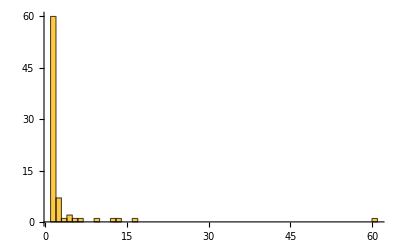

```mathematica
Histogram[Map[#[[2]]&,firstAwsel3],PlotRange->Full]
```

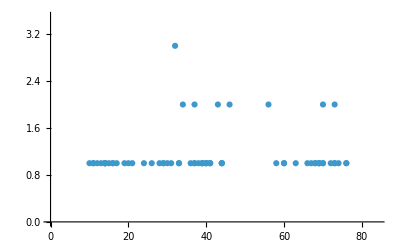

```mathematica
ListPlot[Transpose[{dslen3,Map[#[[2]]&,firstAwsel3]}]]
```

#### クラスタリングに用いる指標の選択

```mathematica
(*{Table[n,{n,Length[obsbs2[[1,2]]]}],obsbs2[[1,2]]//Keys}//TableForm*)
```

2. peakYear
8. decayPeriod
3. peakCount
7. decayCited
11. V:Av5year
12. V:diff
13. Vdiff2

```mathematica
{Table[n,{n,Length[obsbs3[[1,2]]]}],obsbs3[[1,2]]//Keys}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
len | peakYear | peakCount | peakRatio | peakPosition | sustainYear | decayCited | decayPeriod | firstCitedYear | totalCited | V:Av5year | V:diff | V:diff2 | diffTotal | diffSeq

```mathematica
vselP={2,8,3,7,11,12,13}
```

{2,8,3,7,11,12,13}

```mathematica
vselPlen=Length[vselP]
```

7

#### クラスタリング（selection 3 / 7 indices）

サンプル名・サンプルPos

```mathematica
(bsObs3=bs[[obsolatedPos3]])//Length
```

77

```mathematica
posMap3=Table[n->obsolatedPos3[[n]],{n,Length[obsolatedPos3]}]
```

{1→20,2→22,3→31,4→39,5→59,6→72,7→73,8→75,9→76,10→77,11→79,12→88,13→93,14→104,15→107,16→110,17→113,18→114,19→118,20→119,21→120,22→128,23→130,24→133,25→135,26→148,27→151,28→159,29→166,30→182,31→185,32→188,33→203,34→204,35→205,36→216,37→218,38→222,39→224,40→232,41→233,42→238,43→242,44→244,45→248,46→263,47→267,48→274,49→302,50→306,51→313,52→320,53→354,54→355,55→369,56→370,57→386,58→390,59→394,60→405,61→446,62→447,63→450,64→452,65→454,66→455,67→456,68→458,69→459,70→460,71→461,72→465,73→474,74→483,75→484,76→490,77→512}

```mathematica
(sampleObs3PMID=Map[#[[1,2]]&,bsObs3])//Length
```

77

```mathematica
(sampleObs3Pos=Table[n,{n,Length[bsObs3]}])//Length
```

77

データチューニング

```mathematica
(nmObs3Pre=toItemNormarizeMat[bsObs3])//Dimensions
```

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

Transpose::nmtx: …の最初の2個のレベルは転置できません．

{1}

plotデータ

```mathematica
(nmObs3=Map[#[[vselP]]&,nmObs3Pre])//Dimensions
```

{77,7}

```mathematica
(nmZObs3=Prepend[nmObs3,Table[0,{vselPlen}]])//Dimensions
```

{78,7}

```mathematica
(nmtObs3=Map[totalize,nmObs3])//Dimensions
```

{77,7}

```mathematica
(nmtZObs3=Prepend[nmtObs3,Table[0,{vselPlen}]])//Dimensions
```

{78,7}

PCA

```mathematica
nmObs3PCA=PrincipalComponents[nmObs3];
```

```mathematica
nmZObs3PCA=PrincipalComponents[nmZObs3];
```

```mathematica
nmtObs3PCA=PrincipalComponents[nmtObs3];
```

```mathematica
nmtZObs3PCA=PrincipalComponents[nmtZObs3];
```

plot

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmObs3PCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmZObs3PCA[[2;;]]],Red,Point[nmZObs3PCA[[1]][[;;3]]]}]
```

-Graphics3D-

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmtObs3PCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmtZObs3PCA[[2;;]]],Red,Point[nmtZObs3PCA[[1]][[;;3]]]}]
```

-Graphics3D-

クラスタリング
nmObs3に対してユークリッド距離を使うのが良いか。

```mathematica
clusteredPosObs3["SD","Agg"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->CosineDistance,CriterionFunction->"StandardDeviation",Method->"Agglomerate"]
```

{{50},{53},{64},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,19,20,22,23,24,25,28,29,30,33,34,35,37,40,41,42,45,52,54,55,56,57,58,59,60,61,63,65,66,67,68,69,70,71,72,73,74,75,76,77},{21,47,62},{26,31},{39},{27},{36},{18,32},{48},{44},{49},{38},{46},{51},{43}}

```mathematica
clusteredPosObs3["Dunn","Agg"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->CosineDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{50},{53},{64},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,19,20,22,23,24,25,28,29,30,33,34,35,37,40,41,42,45,52,54,55,56,57,58,59,60,61,63,65,66,67,68,69,70,71,72,73,74,75,76,77},{21,47,62},{26,31},{39},{27},{36},{18,32},{48},{44},{49},{38},{46},{51},{43}}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->EuclideanDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,39,40,41,42,45,47,50,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77},{38,43,44,46,48,49,51}}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]//Length
```

2

```mathematica
classMembers=Map[Length,clusteredPosObs3["Dunn","Agg","Ecld"]]
```

{70,7}

```mathematica
dendroID=Map[Rotate[#,-Pi/2,{1,1}]
&,sampleObs3Pos]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77}

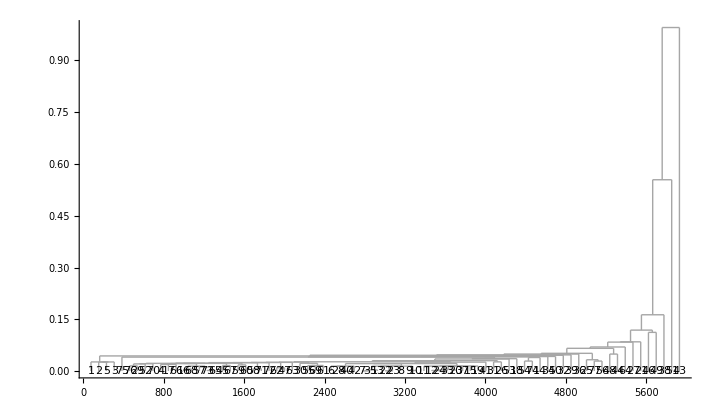

```mathematica
dendroplot=Dendrogram[nmObs3->dendroID,DistanceFunction->EuclideanDistance, Axes->{False, True},ImageSize->720,AspectRatio->1/1.74]
```

```mathematica
nmObs3group["Mn"]={43,51,38,49,46}
```

{43,51,38,49,46}

IDのテキスト表示

```mathematica
txcood=Map[#[[;;3]]&,nmObs3PCA][[nmObs3group["Mn"]]]-0.02
```

{{-1.74813,0.0756572,-0.152445},{-0.841609,-0.141312,0.069916},{-0.335249,-0.0587382,0.0685347},{-0.222124,-0.115092,0.0561313},{-0.21993,-0.0694457,0.072603}}

```mathematica
tx3d=Table[Text[nmObs3group["Mn"][[n]],txcood[[n]]],{n,Length[txcood]}]
```

{Text[43,{-1.74813,0.0756572,-0.152445}],Text[51,{-0.841609,-0.141312,0.069916}],Text[38,{-0.335249,-0.0587382,0.0685347}],Text[49,{-0.222124,-0.115092,0.0561313}],Text[46,{-0.21993,-0.0694457,0.072603}]}

```mathematica
(nmObs3group["Mj"]=Complement[Table[n,{n,77}],nmObs3group["Mn"]])//Length
```

72

```mathematica
pcaplot=Graphics3D[{PointSize->0.02,Red,Map[Point[#[[;;3]]]&,nmObs3PCA][[nmObs3group["Mn"]]],Green,Map[Point[#[[;;3]]]&,nmObs3PCA][[nmObs3group["Mj"]]],Black,tx3d},ImageSize->500,ViewPoint->{0, 1.8, -(Pi+0.06)}]
```

-Graphics3D-

デントログラムとPCAの重ね書き

```mathematica
Show[dendroplot,Graphics[Inset[pcaplot]]]
```

-Graphics-

```mathematica
Show[dendroplot,Graphics[Inset[Rotate[pcaplot,0.12Pi]]]]
```

-Graphics-

多峰性を持つ論文がどのクラスに属するか

```mathematica
obsmultiPos3
```

{77,232,233,484,512}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]/.posMap3
```

{{20,22,31,39,59,72,73,75,76,77,79,88,93,104,107,110,113,114,118,119,120,128,130,133,135,148,151,159,166,182,185,188,203,204,205,216,218,224,232,233,238,248,267,306,320,354,355,369,370,386,390,394,405,446,447,450,452,454,455,456,458,459,460,461,465,474,483,484,490,512},{222,242,244,263,274,302,313}}

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"][[clusteredPosObs3["Dunn","Agg","Ecld"][[1]]]]],PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"][[clusteredPosObs3["Dunn","Agg","Ecld"][[2]]]]],PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

```mathematica
bs//Length
```

536

```mathematica
bsObs3//Length
```

77

## 累積世代ごとのG2論文（一旦なし）

### G2論文

```mathematica
Q2Citingartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt26Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt26Perc.save}

```mathematica
Map[Get,Q2Citingartfiles];
```

主要論文PMIDと被引用数

```mathematica
(top26PcCitedArtList=Table[Reverse[SortBy[Flatten[Map[#[[2]]&,topCitingCitedArt26Perc[n,"citing rule"],{2}]]//Tally,#[[2]]&]],{n,1950,2020,5}])//Length
```

15

全期間のユニークPMID

```mathematica
(top26PcCitedArtPMID=Map[#[[1]]&,top26PcCitedArtList,{2}]//Flatten//Union)//Length
```

89021

G2論文数

```mathematica
top26PcCitedArtCount=Map[Length,top26PcCitedArtList]
```

{76,305,618,937,1449,2056,2835,3668,4663,5933,7239,9779,14655,19457,25231}

全論文数におけるG2論文数割合（%）

```mathematica
top26pcArtRatio=top26PcCitedArtCount/artcountAcm*100//N
```

{0.0229356,0.0352091,0.0436473,0.043749,0.0459049,0.047557,0.0499514,0.0508197,0.051043,0.0525977,0.0529412,0.0587497,0.0717616,0.076674,0.0802497}

## （調査２）G2論文タイトル（一旦なし）

## （調査２.１）G2論文のオブソレッセンス（全ての累積世代での出現）（一旦なし）

全累積世代に見る論文を候補とする。

```mathematica
top26PcCitedArtPMID//Length
```

89021

### pubyearを調べておく

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/PMIDtoPubyear.wl"];
```

```mathematica
Q2CitingCitedPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top26PcCitedArtPMID];
```

```mathematica
Q2yearlist=Sort[Tally[Map[#[[2]]&,Q2CitingCitedPMIDvsPY]]]
```

{{1880,1},{1886,1},{1889,1},{1890,1},{1894,3},{1895,1},{1898,2},{1899,1},{1900,1},{1905,1},{1907,1},{1908,1},{1912,2},{1913,5},{1914,2},{1915,3},{1916,3},{1917,3},{1918,1},{1919,3},{1920,2},{1921,5},{1922,2},{1923,5},{1924,3},{1925,5},{1926,6},{1927,7},{1928,8},{1929,10},{1930,5},{1931,15},{1932,21},{1933,24},{1934,21},{1935,20},{1936,21},{1937,29},{1938,35},{1939,30},{1940,38},{1941,51},{1942,48},{1943,55},{1944,64},{1945,98},{1946,106},{1947,107},{1948,125},{1949,188},{1950,414},{1951,569},{1952,523},{1953,526},{1954,487},{1955,539},{1956,612},{1957,633},{1958,754},{1959,667},{1960,605},{1961,601},{1962,641},{1963,663},{1964,722},{1965,656},{1966,722},{1967,698},{1968,809},{1969,812},{1970,900},{1971,894},{1972,885},{1973,841},{1974,995},{1975,1061},{1976,1081},{1977,1133},{1978,1037},{1979,1010},{1980,1033},{1981,1078},{1982,1189},{1983,1159},{1984,1294},{1985,1277},{1986,1336},{1987,1385},{1988,1492},{1989,1519},{1990,1702},{1991,1684},{1992,1789},{1993,1796},{1994,1751},{1995,1832},{1996,1823},{1997,1875},{1998,2085},{1999,2132},{2000,2318},{2001,2337},{2002,2392},{2003,2429},{2004,2604},{2005,2680},{2006,2530},{2007,2467},{2008,2496},{2009,2274},{2010,2224},{2011,1927},{2012,1540},{2013,1240},{2014,945},{2015,637},{2016,494},{2017,306},{2018,162},{2019,51},{2020,55},{2021,1}}

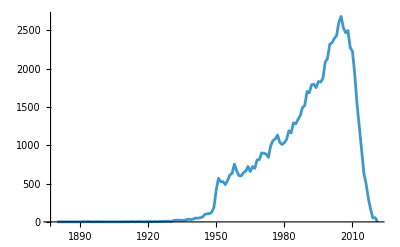

```mathematica
ListPlot[Q2yearlist//ToExpression,PlotRange->Full,Joined->True]
```

### あらためて各主要論文の被引用の状況を確認する

最も古い主要論文は1880出版。

```mathematica
Q2targetYears=Table[ToString[n],{n,1880,2020}]
```

{1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020}

```mathematica
(Q2targetCandPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top26PcCitedArtPMID])//Length
```

89021

PMIDからタイトルを引く

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];*)
```

```mathematica
(*(Q2targetCandPMIDvsTitle=Map[{#,pmidToTitle[#]}&,top26PcCitedArtPMID])//Length*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"Q2targetCandPMIDvsTitle.save",Q2targetCandPMIDvsTitle]*)
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"Q2targetCandPMIDvsTitle.save"];
```

PMID vs. PMID

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/totalEdge.save"];
```

$Aborted

以下の計算ではメモリが不足するので、並列化を外す。-> 4~5日の想定 -> 12/15に終了予定

```mathematica
AbsoluteTiming[(top26PcCitedArtEdges=Map[Cases[totalEdgeList,DirectedEdge[_,#]]&,top26PcCitedArtPMID])//Length]
```

LinkRead::time: Operation LinkRead timed out after 3. seconds.

KernelObject::rdead: Discarding kernel 1 (Local).

LinkRead::time: Operation LinkRead timed out after 3. seconds.

KernelObject::rdead: Discarding kernel 2 (Local).

LinkRead::time: Operation LinkRead timed out after 3. seconds.

General::stop: この計算中に，LinkRead::timeのこれ以上の出力は表示されません．

KernelObject::rdead: Discarding kernel 3 (Local).

General::stop: この計算中に，KernelObject::rdeadのこれ以上の出力は表示されません．

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top26PcCitedArtEdges.save",top26PcCitedArtEdges]*)
```

以下はデータ整形

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top1PcCitedArtEdges.save"];
```

```mathematica
(top1PcCitedArtCitedyear= Map[{PMIDtoPubyear[#[[1]]],{PMIDtoPubyear[#[[2]]],#[[2]]}}&, top1PcCitedArtEdges,{2}])//Length
```

536

yearごとの被引用数リストを作る

：yearから被引用数を得る

```mathematica
toCitedyearlist[l_]:=Module[{citedPMID},
citedPMID=l[[1,2]];
{citedPMID,Association[MapApply[Rule,Tally[Map[#[[1]]&,l]]]]}
]
```

```mathematica
(top1PcCitedArtCitedyearAssociations=Map[toCitedyearlist,top1PcCitedArtCitedyear])//Length
```

536

```mathematica
top1PcCitedArtCitedyearAssociations[[1]]
```

{{1996,10062328},<|2002→1,2003→3,2004→5,2005→8,2006→11,2007→21,2008→32,2009→54,2010→57,2011→84,2012→121,2013→227,2014→271,2015→450,2016→638,2017→770,2018→832,2019→1027,2020→1208,2021→1450,2022→1805,2023→1791,2024→3|>}

：1993からの被引用数リストにする

```mathematica
fromAscToCount[asc_,year_]:=Map[asc[#]&,year]/.{_Missing->0}
```

```mathematica
fromAscToCount[top1PcCitedArtCitedyearAssociations[[1]][[2]],targetYears]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,3,5,8,11,21,32,54,57,84,121,227,271,450,638,770,832,1027,1208}

<1993からの被引用数リスト>

```mathematica
(top1PcCitedArtCitedCount["1933-2020"]=Map[{#[[1]],fromAscToCount[#[[2]],targetYears]}&,top1PcCitedArtCitedyearAssociations])//Length
```

536

：出版年からの被引用数リストにする

```mathematica
fromPY[l_,y_]:=Module[{py,pyp},
py=l[[1,1]];
pyp=Flatten[Position[y,py]][[1]];
{l[[1]],l[[2]][[pyp;;]]}
]
```

```mathematica
fromPY[top1PcCitedArtCitedCount["1933-2020"][[2]],targetYears]
```

{{1998,10069079},{0,6,34,70,107,149,184,191,223,282,320,316,351,406,428,496,523,512,572,634,573,616,607}}

```mathematica
(top1PcCitedArtCitedCount["PY-2020"]=Map[fromPY[#,targetYears]&,top1PcCitedArtCitedCount["1933-2020"]])//Length
```

536

### 分析

#### 一旦plot

出版年を原点としてplot

```mathematica
ListLinePlot3D[Map[#[[2]]&,top1PcCitedArtCitedCount["PY-2020"]],Joined->True,PlotRange->Full]
```

-Graphics3D-

#### OA論文か？

PMCのIDがあればOAとみなす

```mathematica
Import["/Volumes/elecom/BANK/pubmed/202312/xml/element/id/integID.wl"];
```

```mathematica
idsAsc//Length
```

325352

```mathematica
isPMC[id_String]:=If[Position[idsAsc[id],"pmc"]=={},id->0,id->1]
```

```mathematica
GroupBy[Map[isPMC,top1PcCitedArtPMID],Last]
```

<|0→{10062328→0,10069079→0,10075613→0,10102814→0,10109801→0,10547847→0,10592173→0,10592235→0,10638745→0,10647931→0,10655437→0,10789670→0,10797032→0,10802651→0,10827456→0,10829079→0,10835412→0,10963602→0,1105573→0,11130711→0,11152613→0,11181995→0,11209064→0,11234459→0,11237011→0,11253156→0,11283309→0,11309499→0,11328886→0,11368702→0,11373684→0,11498575→0,11524383→0,11553815→0,11556941→0,11689955→0,1172191→0,11752295→0,1175627→0,11771995→0,11823860→0,11832527→0,11846609→0,11904577→0,11932250→0,1195397→0,11994752→0,1202204→0,12045153→0,12068308→0,12111919→0,12117397→0,12130773→0,12184808→0,12297042→0,12377157→0,12391568→0,1244564→0,12466850→0,12485966→0,12490959→0,12538238→0,12629218→0,12734009→0,12748199→0,12824337→0,12883005→0,12900694→0,12912839→0,12925520→0,12958120→0,12989928→0,12991232→0,12991237→0,12996882→0,13069686→0,13124776→0,13130792→0,13186838→0,13249955→0,13262900→0,13267987→0,13276348→0,13278318→0,13286333→0,13293190→0,13298683→0,13319380→0,13428781→0,13475399→0,13563554→0,13610928→0,13610936→0,13641241→0,13650640→0,13655060→0,13671378→0,13672998→0,13675766→0,13688369→0,13718526→0,13726518→0,13764136→0,13767412→0,13772379→0,13910995→0,13944428→0,13975866→0,13986422→0,1400587→0,14097352→0,14240539→0,14287192→0,14381428→0,14381429→0,14399272→0,14450081→0,14454024→0,14474176→0,14530136→0,14597658→0,14656957→0,14744438→0,14772207→0,14775715→0,14794694→0,14803635→0,14822727→0,14848424→0,14862161→0,14873923→0,14898516→0,14907661→0,14907713→0,149110→0,14915960→0,14927572→0,14927794→0,14938350→0,15034147→0,15102499→0,15111519→0,15118073→0,15118125→0,15173120→0,15175435→0,15223320→0,15260895→0,15264254→0,15273542→0,15297300→0,15299374→0,15299926→0,15372042→0,15392854→0,15395398→0,15395569→0,15398090→0,15398551→0,15404816→0,15410483→0,15421999→0,15436457→0,15461798→0,15501092→0,1555235→0,15572765→0,15652477→0,15758009→0,15761078→0,15817019→0,1593914→0,15939837→0,15944708→0,15969739→0,16055882→0,16056220→0,16081474→0,16199517→0,16204405→0,16222654→0,16255080→0,16497588→0,16561366→0,16595758→0,16646809→0,16654194→0,16694480→0,16694558→0,16695228→0,16695286→0,16695568→0,16745305→0,16746620→0,16747230→0,16747456→0,16747508→0,16747652→0,16747674→0,16747784→0,16747907→0,16747948→0,16748220→0,16748273→0,16748381→0,16820507→0,16862161→0,16904174→0,16923388→0,16923606→0,16928733→0,16991506→0,16991878→0,16994401→0,17183312→0,17237035→0,17247100→0,17247150→0,17320507→0,17483113→0,17486113→0,17488738→0,17512414→0,17554300→0,17586664→0,1759558→0,17618441→0,17634462→0,17681537→0,17695343→0,17701901→0,17751251→0,17760012→0,17846036→0,17872937→0,1798888→0,17996036→0,18016252→0,18029452→0,18035408→0,18128147→0,18156677→0,18261238→0,18287387→0,18349386→0,18485877→0,18516045→0,1852778→0,18546601→0,18650514→0,18650914→0,18772890→0,18798982→0,18839484→0,18929686→0,19015660→0,19029910→0,19033363→0,19097774→0,19114008→0,19131956→0,19167326→0,19171970→0,19246619→0,19261174→0,19289445→0,19325852→0,1932883→0,19346325→0,19414839→0,19451168→0,19460998→0,19461840→0,19474385→0,19487818→0,19499576→0,19505943→0,19565683→0,19621072→0,19622511→0,19622551→0,19801464→0,19805654→0,19812666→0,19910308→0,19945376→0,20003500→0,20057044→0,20080505→0,20110278→0,20124692→0,20124702→0,2025413→0,20354512→0,20383002→0,20383131→0,20436464→0,20513432→0,20525638→0,20525992→0,20601685→0,20610543→0,20644199→0,20709691→0,20979621→0,20981092→0,21221095→0,21296855→0,21351269→0,21376230→0,21460441→0,21478889→0,21546353→0,21572440→0,21700674→0,21816040→0,2188735→0,21959131→0,21988835→0,2199796→0,22008217→0,22237781→0,2231712→0,22357727→0,22383036→0,22388286→0,22437870→0,22506599→0,22543367→0,22588877→0,22658127→0,22743772→0,22745249→0,22820204→0,22930834→0,22955616→0,23000897→0,23104886→0,23128226→0,23193283→0,23245604→0,23287718→0,23329690→0,23335087→0,23550210→0,23618408→0,236308→0,24132122→0,24141714→0,2439888→0,24399786→0,2440339→0,24451623→0,2448875→0,2449095→0,24695404→0,24889800→0,2513255→0,25220842→0,25260700→0,25516281→0,25554246→0,25559415→0,25567568→0,25605792→0,25651787→0,25741868→0,26432245→0,265521→0,2659436→0,26742998→0,26808342→0,26903338→0,27004904→0,271968→0,2744487→0,2748771→0,27535533→0,27754618→0,28055103→0,28561359→0,2868172→0,291033→0,29313949→0,2985470→0,2999980→0,30207593→0,3047011→0,30620402→0,3162770→0,31978945→0,31986264→0,32007143→0,320200→0,3203132→0,32031570→0,32109013→0,32171076→0,322279→0,3323813→0,3327686→0,3344216→0,3358796→0,3397865→0,344137→0,3447015→0,3537305→0,3558716→0,3616518→0,3670292→0,36810→0,3692487→0,3714490→0,3798106→0,3802833→0,3806354→0,3838314→0,3843705→0,3881765→0,388356→0,388439→0,3899825→0,3928249→0,4179068→0,4202581→0,4291934→0,4326772→0,4337382→0,4366476→0,4504350→0,4561027→0,4598299→0,4705382→0,4850204→0,4887011→0,4896022→0,4956917→0,5146491→0,518835→0,5432063→0,5700707→0,5806584→0,5962951→0,5963888→0,603028→0,6091052→0,6159641→0,6166661→0,6198242→0,6232463→0,6235151→0,6246368→0,6253831→0,6260957→0,6266278→0,6269464→0,6270629→0,6286831→0,6295879→0,6295880→0,6310323→0,6310324→0,6312838→0,6326095→0,6329026→0,6329717→0,6336730→0,6345791→0,6546423→0,6606682→0,6610841→0,6667333→0,6668417→0,6791577→0,6828386→0,6880820→0,6960240→0,7063747→0,7108955→0,7138600→0,7219534→0,7463489→0,7494007→0,773363→0,7786990→0,7814313→0,7984236→0,7984417→0,8223268→0,8242752→0,8252621→0,8254673→0,8366922→0,8421494→0,843571→0,8520220→0,8524021→0,8589427→0,8628042→0,8721797→0,8744570→0,8744573→0,8779443→0,8812068→0,881736→0,8902363→0,9176952→0,9177342→0,922889→0,9254694→0,9278503→0,9305837→0,9310563→0,9367129→0,9396791→0,942051→0,9486653→0,9504803→0,9521319→0,9521921→0,9521922→0,9623998→0,9634230→0,9717241→0,9742976→0,9757107→0,9759494→0,9804556→0,9843981→0,9881538→0,9887164→0,9916792→0,9918953→0,9931268→0,9944570→0},1→{9023104→1}|>

#### 指標値

"len" => 出版から2020までの年数
“peakYear” => 出版からピークを迎えるまでの年数☑️
“peakCount” => ピークの年の被引用数☑️
“peakRatio” => peakCount/decayCited（”活動期間”の被引用）
“peakPosition” => “活動期間”中におけるpeakの位置（全体を1とする）
“sustainYear” => ピークの年から2020までの年数
“decayYear” => ピークの年を超えてから年間引用が全体の引用の5%以下となるまでの出版からの年数☑️
“decayCited” => decayYearまでの被引用数☑️
“firstCitedYear” => 最初の引用が発生するまでの年数（出版年に発生すると0）
“totalCited” => 出版年から2020までの総被引用数
“V:Av5year” => 5年引用数平均の分散☑️
“V:diff” => 5年引用数平均の差分の分散（ゼロパディングあり=>出版年での立ち上がりが見える）☑️
“V:diff2” => 5年引用数平均の差分の差分の分散☑️
“diffTotal” => 5年引用数平均の差分の累計：十分に大きい値があり十分に長い期間があれば0に近づく

```mathematica
top1PcCitedArtCitedCount["PY-2020"]//Length
```

536

```mathematica
Accumulate[top1PcCitedArtCitedCount["PY-2020"][[1,2]]]
```

{0,0,0,0,0,0,1,4,9,17,28,49,81,135,192,276,397,624,895,1345,1983,2753,3585,4612,5820}

```mathematica
acRatio[l_]:=Module[{ac},
ac=Accumulate[l];
N[l/ac]/.Indeterminate->1
]
```

```mathematica
acRatio[top1PcCitedArtCitedCount["PY-2020"][[20,2]]]
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

{1,1.,0.646154,0.424779,0.303329,0.201772,0.14044,0.101141,0.10605,0.0840598,0.0716763,0.0673854,0.0734266,0.0636109,0.0585645,0.0580672,0.0481642,0.0408936,0.0385876,0.0411867,0.0340526}

```mathematica
peakP=Flatten[Position[top1PcCitedArtCitedCount["PY-2020"][[20,2]],Max[top1PcCitedArtCitedCount["PY-2020"][[20,2]]]]][[1]]
```

5

```mathematica
tmpP=Cases[Flatten[Position[acRatio[top1PcCitedArtCitedCount["PY-2020"][[20,2]]],x_/;x<=0.05]],x_/;x>peakP]
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

{17,18,19,20,21}

```mathematica
ndiff[l_,w_]:=BlockMap[(#[[-1]]-#[[1]])/(w-1)&,Join[Table[0,{w-1}],l],w,1]
```

```mathematica
ndiff[l_]:=BlockMap[(#[[-1]]-#[[1]])&,l,2,1]
```

```mathematica
myVar[l_]:=If[Length[l]>1,Variance[l],0]
```

```mathematica
basicStat[citedcount_]:=Module[{len,argPeak,peakYear,max,sustainYear,decayTH,decayPlist,decayCited,decayPeriod,firstCitedYear,total,Av5year,diff,diff2,diffTotal},
decayTH=0.05;
len=Length[citedcount];
argPeak=Flatten[Position[citedcount,max=Max[citedcount]]];
peakYear=argPeak[[1]];
sustainYear=len-argPeak[[-1]];
decayPlist=Cases[Flatten[Position[acRatio[citedcount],x_/;x<=decayTH]],x_/;x>peakYear];
decayCited=Total[citedcount[[;;Min[decayPlist]]]];
decayPeriod=Min[decayPlist]-peakYear;
If[Length[decayPlist]<=0,decayPeriod="InDecay"];
firstCitedYear=Min[Position[citedcount,x_/;x>0]]-1;
total=Total[citedcount];
Av5year=MovingAverage[Join[citedcount,Table[0,{n,4}]],5];
diff=ndiff[Av5year];
diff2=ndiff[diff];
diffTotal=Total[diff//N];
Association[{"len"->len,"peakYear"->peakYear,"peakCount"->max,"peakRatio"->max/decayCited//N,"peakPosition"->peakYear/Min[decayPlist]//N,"sustainYear"->sustainYear,"decayCited"->decayCited,"decayPeriod"->decayPeriod,"firstCitedYear"->firstCitedYear,"totalCited"->total,"V:Av5year"->myVar[Av5year//N],"V:diff"->myVar[diff//N],"V:diff2"->myVar[diff2//N],"diffTotal"->diffTotal,"diffSeq"->diff}]
]
```

```mathematica
toItemNormarizeMat[l_]:=Module[{m,key},
key=Keys[l[[1,2]]];
m=Map[Normal[#[[2]]]&,l]/.{None->0};
Transpose[Map[Normalize,Transpose[Map[#[[2]]&,m,{2}]]]//N]
]
```

```mathematica
totalize[l_]:=l/Total[l]
```

```mathematica
(bs=Map[{#[[1]],basicStat[#[[2]]]}&,top1PcCitedArtCitedCount["PY-2020"]])//Length
```

Power::infy: 無限式1/0が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

Part::span: 1;;∞は有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

536

#### 多峰性テスト(all)

外部（python）で行う。

：データ出力

```mathematica
outdir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload/

```mathematica
prefix="citedcount_"
```

citedcount_

```mathematica
(targetfiles=Map[outdir<>prefix<>#[[1,2]]<>".csv"&,top1PcCitedArtCitedCount["PY-2020"]])//Length
```

536

```mathematica
(*Do[Export[targetfiles[[n]],top1PcCitedArtCitedCount["PY-2020"][[n]][[2]]],{n,Length[top1PcCitedArtCitedCount["PY-2020"]]}]*)
```

：実行

% cd /Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload
% source ~/main/bin/activate
% for file in *csv; do python ./bin/peak_estimator.py -f $file -mc 5 -bw 1 > $file.out; done

：結果の回収

対象ファイルネームの生成とimport

```mathematica
(ret=Map[Import[#<>".out","Text"]&,targetfiles])//Length
```

536

計算されないものがあり $Failed がある。

```mathematica
(allMultimode=(Map[StringSplit[StringSplit[#,"\n"][[-1]],": "][[-1]]&,ret]//ToExpression))//Length
```

Part::partw: {}の部分-1は存在しません．

StringSplit::strse: 文字列あるいは文字列のリストがStringSplit[{}⟦-1⟧,: ]の位置1に想定されています．

Part::partw: {}の部分-1は存在しません．

StringSplit::strse: 文字列あるいは文字列のリストがStringSplit[{}⟦-1⟧,: ]の位置1に想定されています．

Part::partw: {}の部分-1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

StringSplit::strse: 文字列あるいは文字列のリストがStringSplit[{}⟦-1⟧,: ]の位置1に想定されています．

General::stop: この計算中に，StringSplit::strseのこれ以上の出力は表示されません．

ToExpression::sntx: 無効な文法が": "の中あるいはその前にあります．
                            ^

General::stop: この計算中に，ToExpression::sntxのこれ以上の出力は表示されません．

536

```mathematica
allMultimodePos=Flatten[Position[allMultimode,2]]
```

{77,124,131,232,233,484,512}

```mathematica
allSinglemodePos=Flatten[Position[allMultimode,1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,125,126,127,128,129,130,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,381,382,383,385,386,388,390,394,395,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536}

#### Selection(1)

十分にオブソレッセンスがみられるものだけを抽出する。

・出版から十分な時間が経過している：”len”が十分に長い(10年以上)
・ピーク期が十分に過ぎ去っている：“sustainYear”が“peakYear”以上
・被引用の傾向が十分に低下している：“5yeardiffTotal”が”totalCited”に比べて十分に小さい(5%以下)

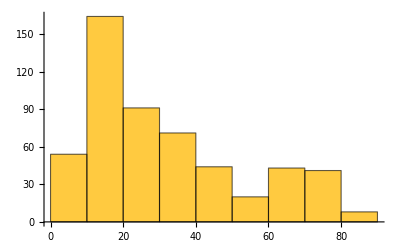

```mathematica
Map[#[[2]]["len"]&,bs]//Histogram
```

```mathematica
(obsolatedPos=Flatten[Position[bs,x_/;x[[2]]["len"]>=10&&x[[2]]["sustainYear"]>=x[[2]]["peakYear"]&&(x[[2]]["diffTotal"]/x[[2]]["totalCited"])<=0.05]])//Length
```

Part::partd: 部分指定List⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: ∞の部分2は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

204

```mathematica
obsolated=top1PcCitedArtCitedCount["PY-2020"][[obsolatedPos]];
```

```mathematica
obsolatedSort["PY"]=SortBy[obsolated,#[[1,1]]&];
```

以下はplotの色の調整

```mathematica
myColor1[z_]:=RGBColor[z,0.8(1-z),0.4(1-z)];
myColor2[z_]:=CMYKColor[z,((1-z)/3)^2,((1-z)/2)^2,Sqrt[z]];
myColor3[z_]:=CMYKColor[((1-z)/3)^2,z,((1-z)/2)^2,Sqrt[z]];
myColor4[z_]:=CMYKColor[((1-z)/3)^2,((1-z)/3)^2,z,Sqrt[z]];
myColor5[z_]:=CMYKColor[(z)^2,(z),(z),(z)^(1.2)];
myColor6[z_]:=Blend[{Red,Green,White},{1,0.75(1-z),(1-z)^(3)}];
cf1=Function[{x,y,z},Hue[5/6 (1-z),0.3+(z^2),1]];
cf2=Function[{x,y,z},Hue[5/6 (1-z),#+(1-#)*z,1]&@0.05];
cf3=Function[{x,y,z},Hue[5/6*(1-z),(#1+(1-#1)*z)^#2,1]]&@@{.25(*offset*),1.0(*gain*)};
```

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->cf2]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->cf3]
```

-Graphics3D-

#### Selection(2)

十分にオブソレッセンスがみられるものだけを抽出する。

・出版から十分な時間が経過している：”len”が十分に長い(10年以上)
・ピーク期が十分に過ぎ去っている：“sustainYear”が“peakYear”以上
・被引用の傾向が十分に低下している：“decayPeriod”が”InDicay”でない（peakYear以降かつ当該年の引用数が当該年までの引用数の5%以下となる年のうち最も古い）

```mathematica
(obsolatedPos2=Flatten[Position[bs,x_/;x[[2]]["len"]>=10&&x[[2]]["sustainYear"]>=x[[2]]["peakYear"]&&x[[2]]["decayPeriod"]!="InDecay"]])//Length
```

Part::partd: 部分指定List⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: ∞の部分2は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

193

多峰性を持つpos

```mathematica
obsmultiPos2=Intersection[allMultimodePos,obsolatedPos2]
```

{77,124,131,232,233,484,512}

```mathematica
obsolated2=top1PcCitedArtCitedCount["PY-2020"][[obsolatedPos2]];
```

```mathematica
obsolatedSort2["PY"]=SortBy[obsolated2,#[[1,1]]&];
```

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort2["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

#### Selection(3)

十分にオブソレッセンスがみられるものだけを抽出する。

・出版から十分な時間が経過している：”len”が十分に長い(10年以上)
・ピーク期が十分に過ぎ去っている：“decayPeriod”が“peakYear”以上
・被引用の傾向が十分に低下している：“decayPeriod”が”InDicay”でない（peakYear以降かつ当該年の引用数が当該年までの引用数の5%以下となる年のうち最も古い）

```mathematica
(obsolatedPos3=Flatten[Position[bs,x_/;x[[2]]["len"]>=10&&x[[2]]["decayPeriod"]>=x[[2]]["peakYear"]&&x[[2]]["decayPeriod"]!="InDecay"]])//Length
```

Part::partd: 部分指定List⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: ∞の部分2は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

77

多峰性を持つpos

```mathematica
obsmultiPos3=Intersection[allMultimodePos,obsolatedPos3]
```

{77,232,233,484,512}

```mathematica
obsolated3=top1PcCitedArtCitedCount["PY-2020"][[obsolatedPos3]];
```

```mathematica
obsolatedSort3["PY"]=SortBy[obsolated3,#[[1,1]]&];
```

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

#### 指標plot(all)

```mathematica
bs//Length
```

536

```mathematica
Histogram[Map[#[[2]]["len"]&,bs],{1},PlotRange->Full]
```

-Graphics-

```mathematica
Map[#[[2]]["len"]&,bs]//Max
Map[#[[2]]["len"]&,bs]//Min
```

88

1

```mathematica
Histogram[Map[#[[2]]["peakRatio"]&,bs],PlotRange->Full]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["peakPosition"]&,bs],PlotRange->Full]
```

-Graphics-

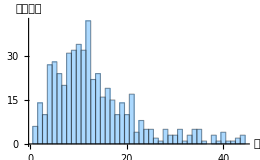

```mathematica
hi["peakYear","all"]=Labeled[Histogram[Map[#[[2]]["peakYear"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->260],"1 出版からピークまでの年"]
```

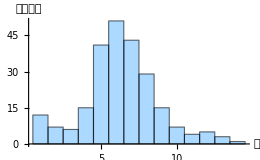

```mathematica
hi["decayPeriod","all"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->260],"2 ピークから減衰までの年"]
```

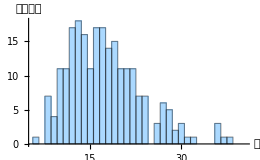

```mathematica
hi["activePeriod","all"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->260],"3 出版から減衰までの年"]
```

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,bs]]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,bs]]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["V:Av5year"]&,bs],{1000}]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["V:diff"]&,bs],{100}]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["V:diff2"]&,bs],{50}]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["diffTotal"]&,bs]]
```

-Graphics-

#### 指標plot(selection 2)

```mathematica
bs//Length
```

536

```mathematica
(obsbs2=bs[[obsolatedPos2]])//Length
```

193

```mathematica
Keys[obsbs2[[1,2]]]
```

{len,peakYear,peakCount,peakRatio,peakPosition,sustainYear,decayCited,decayPeriod,firstCitedYear,totalCited,V:Av5year,V:diff,V:diff2,diffTotal,diffSeq}

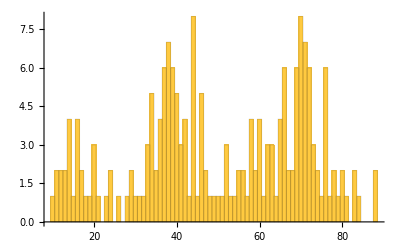

```mathematica
Histogram[Map[#[[2]]["len"]&,obsbs2],{1}]
```

```mathematica
Map[#[[2]]["len"]&,obsbs2]//Max
Map[#[[2]]["len"]&,obsbs2]//Min
```

88

10

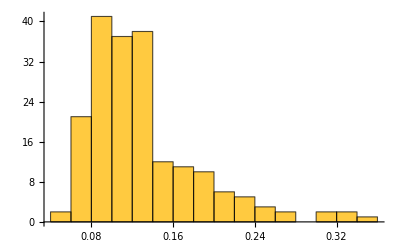

```mathematica
Histogram[Map[#[[2]]["peakRatio"]&,obsbs2],PlotRange->Full]
```

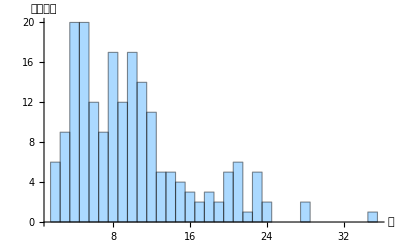

```mathematica
Labeled[Histogram[Map[#[[2]]["peakYear"]&,obsbs2],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"}],"1 出版からピークまでの年"]
```

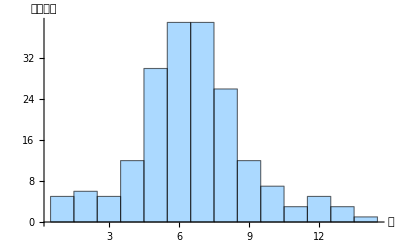

```mathematica
Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,obsbs2],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"}],"2 ピークから減衰までの年"]
```

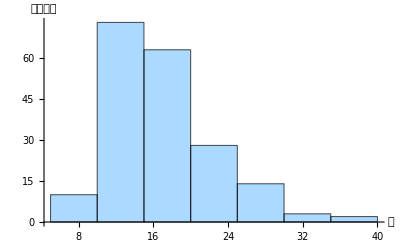

```mathematica
Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,obsbs2],{5},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"}],"3 出版から減衰までの年"]
```

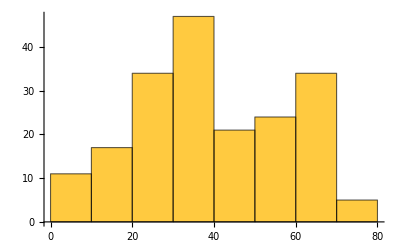

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,obsbs2]]
```

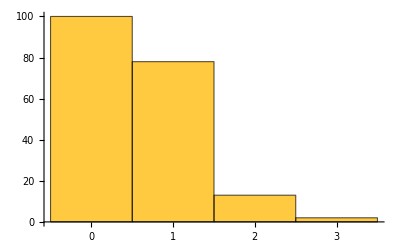

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,obsbs2]]
```

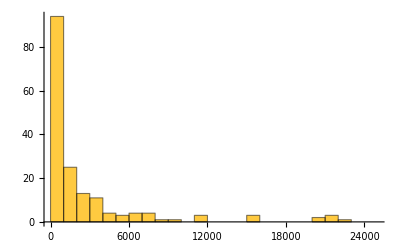

```mathematica
Histogram[Map[#[[2]]["V:Av5year"]&,obsbs2],{1000}]
```

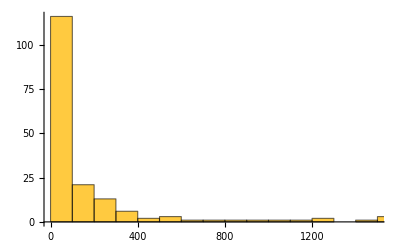

```mathematica
Histogram[Map[#[[2]]["V:diff"]&,obsbs2],{100}]
```

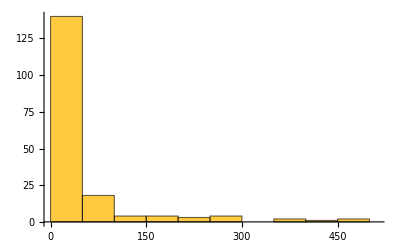

```mathematica
Histogram[Map[#[[2]]["V:diff2"]&,obsbs2],{50}]
```

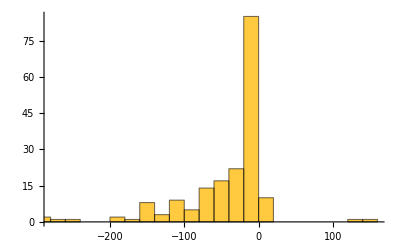

```mathematica
Histogram[Map[#[[2]]["diffTotal"]&,obsbs2]]
```

#### 指標plot(selection 3)

```mathematica
bs//Length
```

536

```mathematica
(obsbs3=bs[[obsolatedPos3]])//Length
```

77

```mathematica
Keys[obsbs3[[1,2]]]
```

{len,peakYear,peakCount,peakRatio,peakPosition,sustainYear,decayCited,decayPeriod,firstCitedYear,totalCited,V:Av5year,V:diff,V:diff2,diffTotal,diffSeq}

```mathematica
Histogram[Map[#[[2]]["len"]&,obsbs3],{1}]
```

-Graphics-

```mathematica
Map[#[[2]]["len"]&,obsbs3]//Max
Map[#[[2]]["len"]&,obsbs3]//Min
```

84

10

```mathematica
Histogram[Map[#[[2]]["peakRatio"]&,obsbs3],PlotRange->Full]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["peakPosition"]&,obsbs3],PlotRange->Full]
```

-Graphics-

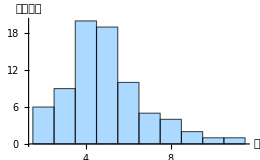

```mathematica
hi["peakYear","obs"]=Labeled[Histogram[Map[#[[2]]["peakYear"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->260],"1 出版からピークまでの年"]
```

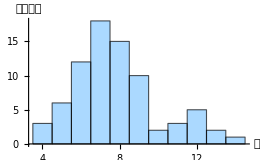

```mathematica
hi["decayPeriod","obs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->260],"2 ピークから減衰までの年"]
```

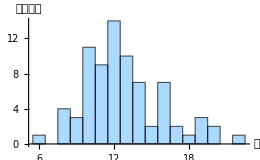

```mathematica
hi["activePeriod","obs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->260],"3 出版から減衰までの年"]
```

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,obsbs3]]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,obsbs3]]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["V:Av5year"]&,obsbs3],{1000}]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["V:diff"]&,obsbs3],{100}]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["V:diff2"]&,obsbs3],{50}]
```

-Graphics-

```mathematica
Histogram[Map[#[[2]]["diffTotal"]&,obsbs3]]
```

-Graphics-

#### 指標plot tbl (all + selection 3)

```mathematica
tbl["index plot"]={{"All",hi["peakYear","all"],hi["decayPeriod","all"],hi["activePeriod","all"]},
{"Obsolated",hi["peakYear","obs"],hi["decayPeriod","obs"],hi["activePeriod","obs"]}
}//TableForm
```

All | -Graphics- | -Graphics- | -Graphics-
Obsolated | -Graphics- | -Graphics- | -Graphics-

#### 指標sleeping beauty(selection 2)

```mathematica
dssel2=Map[#[[2]]["diffSeq"]&,bs[[obsolatedPos2]]];
```

```mathematica
firstAwsel2=Map[{Max[#],Flatten[Position[#,Max[#]]][[1]]}&,dssel2//N]
```

{{22.4,3},{41.,1},{15.,5},{60.8,3},{30.6,1},{27.,3},{28.2,2},{132.4,5},{33.6,1},{1.,1},{1.4,1},{2.6,1},{2.2,1},{2.6,1},{5.6,14},{1.6,1},{3.6,61},{8.6,8},{6.8,15},{6.2,2},{7.6,15},{4.6,1},{12.,12},{1.,13},{5.,1},{7.2,5},{5.,8},{4.,1},{6.2,17},{4.2,4},{8.4,4},{24.,2},{9.,4},{6.2,2},{6.4,2},{6.8,1},{16.,1},{41.4,2},{25.8,1},{7.6,7},{22.6,3},{15.8,2},{1.4,1},{1.6,4},{7.4,16},{10.,1},{6.2,1},{87.6,4},{0.8,1},{4.8,11},{2.,2},{2.,9},{2.,1},{2.4,7},{1.6,1},{3.,3},{4.,1},{2.6,2},{136.6,19},{18.4,2},{2.8,1},{2.4,6},{6.2,1},{44.6,1},{71.2,1},{96.8,1},{1.2,1},{4.2,7},{3.2,1},{1.4,1},{2.,1},{1.8,2},{1.8,2},{6.,19},{16.2,1},{114.6,2},{56.8,2},{51.6,1},{2.6,1},{63.4,1},{0.8,6},{1.6,4},{1.8,1},{1.6,2},{3.2,18},{2.8,12},{3.4,15},{1.8,3},{3.,6},{1.4,8},{1.4,6},{4.2,1},{1.4,4},{1.8,2},{1.6,1},{3.6,1},{2.8,2},{1.,5},{0.8,4},{1.8,18},{14.4,1},{0.8,1},{261.2,1},{68.4,1},{1.,60},{0.6,1},{1.,1},{4.,25},{-103.6,12},{21.2,1},{31.,1},{-34.4,9},{59.8,1},{58.8,1},{88.6,1},{91.2,1},{254.8,1},{33.2,1},{36.,5},{16.2,1},{150.4,4},{76.6,1},{22.6,2},{32.6,1},{36.,3},{239.,8},{38.,1},{96.,1},{42.6,1},{45.8,2},{56.6,1},{20.4,1},{27.6,4},{37.4,1},{31.8,1},{21.,1},{21.2,1},{15.6,1},{30.6,2},{39.2,3},{69.6,2},{118.8,3},{16.,8},{9.6,15},{16.2,1},{29.6,10},{11.6,6},{27.2,9},{41.2,2},{14.4,1},{15.8,12},{17.,4},{88.,5},{194.4,12},{39.4,1},{10.6,1},{19.6,13},{9.2,8},{56.2,1},{72.8,1},{18.8,3},{38.,2},{22.,1},{38.2,2},{133.8,1},{29.6,1},{31.8,1},{24.,1},{41.8,3},{28.2,1},{50.6,1},{31.6,1},{61.4,1},{16.4,2},{152.,3},{29.2,1},{53.,2},{10.6,6},{33.8,3},{30.4,1},{105.,4},{26.6,1},{40.8,3},{59.,3},{36.6,2},{15.2,1},{0.2,16},{23.8,1},{95.2,3},{24.6,3},{24.2,1},{42.,6},{63.2,5}}

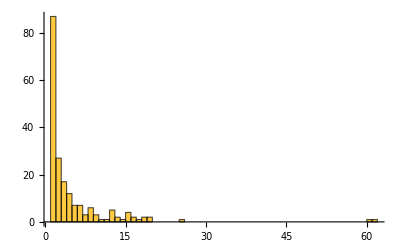

```mathematica
Histogram[Map[#[[2]]&,firstAwsel2],PlotRange->Full]
```

#### 指標sleeping beauty(selection 3)

```mathematica
dssel3=Map[#[[2]]["diffSeq"]&,bs[[obsolatedPos3]]];
```

```mathematica
dslen3=Map[#[[2]]["len"]&,bs[[obsolatedPos3]]]
```

{21,20,20,46,19,69,69,69,68,68,67,65,63,60,58,29,56,66,60,60,18,70,70,70,43,17,16,72,29,16,15,84,74,73,73,14,76,14,14,75,73,76,13,13,30,12,14,12,11,11,10,31,33,34,44,32,36,33,44,44,37,41,37,41,41,40,40,39,39,39,38,37,40,26,45,28,24}

```mathematica
dsPMID3=Map[#[[1,2]]&,bs[[obsolatedPos3]]]
```

{11130711,11181995,11373684,1175627,12466850,12989928,12991232,12996882,13069686,13124776,13186838,13319380,13610936,13767412,13944428,1400587,14287192,14381428,14454024,14474176,14530136,14822727,14862161,14907661,149110,15260895,15297300,15398551,1555235,16255080,16595758,16694480,16748220,16748273,16748381,17237035,17247150,17488738,17554300,17751251,17760012,18016252,18156677,18287387,1852778,19171970,19325852,19474385,20610543,20981092,21546353,2199796,2448875,2449095,265521,2659436,2999980,3162770,320200,344137,6091052,6159641,6232463,6246368,6260957,6266278,6269464,6286831,6295879,6295880,6310323,6329026,6791577,7494007,773363,8242752,9278503}

```mathematica
firstAwsel3=Map[{Max[#],Flatten[Position[#,Max[#]]][[1]]}&,dssel3//N]
```

{{41.,1},{15.,5},{30.6,1},{28.2,2},{33.6,1},{1.,1},{1.4,1},{2.6,1},{2.2,1},{2.6,1},{1.6,1},{1.,13},{4.,1},{9.,4},{6.8,1},{25.8,1},{15.8,2},{1.4,1},{10.,1},{6.2,1},{87.6,4},{2.,1},{1.6,1},{2.6,2},{18.4,2},{71.2,1},{96.8,1},{1.4,1},{16.2,1},{51.6,1},{63.4,1},{0.8,6},{1.6,1},{3.6,1},{2.8,2},{14.4,1},{0.8,1},{261.2,1},{68.4,1},{1.,60},{0.6,1},{1.,1},{-103.6,12},{21.2,1},{31.,1},{-34.4,9},{59.8,1},{58.8,1},{88.6,1},{91.2,1},{254.8,1},{33.2,1},{76.6,1},{22.6,2},{32.6,1},{36.,3},{42.6,1},{56.6,1},{20.4,1},{31.8,1},{56.2,1},{72.8,1},{22.,1},{133.8,1},{29.6,1},{31.8,1},{24.,1},{28.2,1},{50.6,1},{31.6,1},{61.4,1},{53.,2},{26.6,1},{15.2,1},{0.2,16},{23.8,1},{24.2,1}}

```mathematica
Histogram[Map[#[[2]]&,firstAwsel3],PlotRange->Full]
```

-Graphics-

```mathematica
ListPlot[Transpose[{dslen3,Map[#[[2]]&,firstAwsel3]}]]
```

-Graphics-

#### クラスタリングに用いる指標の選択

```mathematica
{Table[n,{n,Length[obsbs2[[1,2]]]}],obsbs2[[1,2]]//Keys}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
len | peakYear | peakCount | peakRatio | peakPosition | sustainYear | decayCited | decayPeriod | firstCitedYear | totalCited | V:Av5year | V:diff | V:diff2 | diffTotal | diffSeq

2. peakYear
8. decayPeriod
3. peakCount
7. decayCited
11. V:Av5year
12. V:diff
13. Vdiff2

```mathematica
vselP={2,8,3,7,11,12,13}
```

{2,8,3,7,11,12,13}

```mathematica
vselPlen=Length[vselP]
```

7

#### クラスタリング（selection 2 / 7 indices）

サンプル名・サンプルPos

```mathematica
(bsObs2=bs[[obsolatedPos2]])//Length
```

193

```mathematica
posMap2=Table[n->obsolatedPos2[[n]],{n,Length[obsolatedPos2]}]
```

{1→19,2→20,3→22,4→28,5→31,6→37,7→39,8→46,9→59,10→72,11→73,12→75,13→76,14→77,15→78,16→79,17→80,18→81,19→82,20→83,21→84,22→85,23→86,24→88,25→90,26→91,27→92,28→93,29→94,30→98,31→99,32→103,33→104,34→105,35→106,36→107,37→108,38→109,39→110,40→111,41→112,42→113,43→114,44→115,45→117,46→118,47→119,48→120,49→124,50→125,51→126,52→127,53→128,54→129,55→130,56→131,57→132,58→133,59→134,60→135,61→136,62→137,63→138,64→147,65→148,66→151,67→155,68→157,69→158,70→159,71→160,72→161,73→162,74→163,75→166,76→170,77→177,78→182,79→184,80→185,81→188,82→189,83→190,84→191,85→193,86→194,87→195,88→196,89→197,90→198,91→199,92→200,93→201,94→202,95→203,96→204,97→205,98→212,99→213,100→214,101→216,102→218,103→222,104→224,105→232,106→233,107→238,108→241,109→242,110→244,111→248,112→263,113→267,114→274,115→302,116→306,117→313,118→320,119→347,120→350,121→352,122→354,123→355,124→369,125→370,126→375,127→383,128→385,129→386,130→388,131→390,132→394,133→399,134→400,135→405,136→407,137→410,138→413,139→417,140→419,141→420,142→421,143→424,144→426,145→427,146→430,147→432,148→433,149→434,150→435,151→436,152→437,153→439,154→440,155→442,156→443,157→444,158→445,159→446,160→447,161→448,162→449,163→450,164→451,165→452,166→454,167→455,168→456,169→457,170→458,171→459,172→460,173→461,174→462,175→463,176→464,177→465,178→466,179→467,180→468,181→469,182→474,183→475,184→477,185→479,186→483,187→484,188→490,189→505,190→510,191→512,192→515,193→527}

```mathematica
(sampleObs2PMID=Map[#[[1,2]]&,bsObs2])//Length
```

193

```mathematica
(sampleObs2Pos=Table[n,{n,Length[bsObs2]}])//Length
```

193

データチューニング

```mathematica
(nmObs2Pre=toItemNormarizeMat[bsObs2])//Dimensions
```

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

Transpose::nmtx: …の最初の2個のレベルは転置できません．

{1}

plotデータ

```mathematica
(nmObs2=Map[#[[vselP]]&,nmObs2Pre])//Dimensions
```

{193,7}

```mathematica
(nmZObs2=Prepend[nmObs2,Table[0,{vselPlen}]])//Dimensions
```

{194,7}

```mathematica
(nmtObs2=Map[totalize,nmObs2])//Dimensions
```

{193,7}

```mathematica
(nmtZObs2=Prepend[nmtObs2,Table[0,{vselPlen}]])//Dimensions
```

{194,7}

PCA

```mathematica
nmObs2PCA=PrincipalComponents[nmObs2];
```

```mathematica
nmZObs2PCA=PrincipalComponents[nmZObs2];
```

```mathematica
nmtObs2PCA=PrincipalComponents[nmtObs2];
```

```mathematica
nmtZObs2PCA=PrincipalComponents[nmtZObs2];
```

plot

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmObs2PCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmZObs2PCA[[2;;]]],Red,Point[nmZObs2PCA[[1]][[;;3]]]}]
```

-Graphics3D-

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmtObs2PCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmtZObs2PCA[[2;;]]],Red,Point[nmtZObs2PCA[[1]][[;;3]]]}]
```

-Graphics3D-

クラスタリング
nmObs2に対してコサイン距離を使うのが良いか。

```mathematica
clusteredPosObs2["SD","Agg"]=FindClusters[nmObs2->sampleObs2Pos,DistanceFunction->CosineDistance,CriterionFunction->"StandardDeviation",Method->"Agglomerate"]
```

{{1,2,3,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,44,45,46,47,49,50,51,52,53,54,55,56,57,58,60,61,62,63,66,67,68,69,70,71,72,73,74,75,78,79,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,104,105,106,107,108,111,113,114,118,119,120,123,124,125,127,129,130,131,132,133,134,135,136,137,138,139,140,143,144,145,146,147,148,149,150,151,152,155,156,157,158,159,160,161,162,163,164,166,167,168,170,171,172,173,174,176,177,178,179,180,182,183,185,186,187,188,190,191,192},{43,81},{64,77,169,184},{4,48,128,141,153,181,189,193},{8,59,65,76,80,103,109,110,112,115,116,117,121,122,126,142,154,165,175}}

```mathematica
clusteredPosObs2["Dunn","Agg"]=FindClusters[nmObs2->sampleObs2Pos,DistanceFunction->CosineDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{1,2,3,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,44,45,46,47,49,50,51,52,53,54,55,56,57,58,60,61,62,63,66,67,68,69,70,71,72,73,74,75,78,79,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,104,105,106,107,108,111,113,114,118,119,120,123,124,125,127,129,130,131,132,133,134,135,136,137,138,139,140,143,144,145,146,147,148,149,150,151,152,155,156,157,158,159,160,161,162,163,164,166,167,168,170,171,172,173,174,176,177,178,179,180,182,183,185,186,187,188,190,191,192},{43,81},{64,77,169,184},{4,48,128,141,153,181,189,193},{8,59,65,76,80,103,109,110,112,115,116,117,121,122,126,142,154,165,175}}

```mathematica
clusteredPosObs2["Dunn","Agg"]//Length
```

5

```mathematica
Map[Length,clusteredPosObs2["Dunn","Agg"]]
```

{160,2,4,8,19}

多峰性を持つ論文がどのクラスに属するか

```mathematica
obsmultiPos2
```

{77,124,131,232,233,484,512}

```mathematica
Map[Intersection[#,obsmultiPos2]&,clusteredPosObs2["Dunn","Agg"]/.posMap2]
```

{{77,124,131,232,233,484,512},{},{},{},{}}

#### クラスタリング（selection 3 / 7 indices）

サンプル名・サンプルPos

```mathematica
(bsObs3=bs[[obsolatedPos3]])//Length
```

77

```mathematica
posMap3=Table[n->obsolatedPos3[[n]],{n,Length[obsolatedPos3]}]
```

{1→20,2→22,3→31,4→39,5→59,6→72,7→73,8→75,9→76,10→77,11→79,12→88,13→93,14→104,15→107,16→110,17→113,18→114,19→118,20→119,21→120,22→128,23→130,24→133,25→135,26→148,27→151,28→159,29→166,30→182,31→185,32→188,33→203,34→204,35→205,36→216,37→218,38→222,39→224,40→232,41→233,42→238,43→242,44→244,45→248,46→263,47→267,48→274,49→302,50→306,51→313,52→320,53→354,54→355,55→369,56→370,57→386,58→390,59→394,60→405,61→446,62→447,63→450,64→452,65→454,66→455,67→456,68→458,69→459,70→460,71→461,72→465,73→474,74→483,75→484,76→490,77→512}

```mathematica
(sampleObs3PMID=Map[#[[1,2]]&,bsObs3])//Length
```

77

```mathematica
(sampleObs3Pos=Table[n,{n,Length[bsObs3]}])//Length
```

77

データチューニング

```mathematica
(nmObs3Pre=toItemNormarizeMat[bsObs3])//Dimensions
```

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

Transpose::nmtx: …の最初の2個のレベルは転置できません．

{1}

plotデータ

```mathematica
(nmObs3=Map[#[[vselP]]&,nmObs3Pre])//Dimensions
```

{77,7}

```mathematica
(nmZObs3=Prepend[nmObs3,Table[0,{vselPlen}]])//Dimensions
```

{78,7}

```mathematica
(nmtObs3=Map[totalize,nmObs3])//Dimensions
```

{77,7}

```mathematica
(nmtZObs3=Prepend[nmtObs3,Table[0,{vselPlen}]])//Dimensions
```

{78,7}

PCA

```mathematica
nmObs3PCA=PrincipalComponents[nmObs3];
```

```mathematica
nmZObs3PCA=PrincipalComponents[nmZObs3];
```

```mathematica
nmtObs3PCA=PrincipalComponents[nmtObs3];
```

```mathematica
nmtZObs3PCA=PrincipalComponents[nmtZObs3];
```

plot

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmObs3PCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmZObs3PCA[[2;;]]],Red,Point[nmZObs3PCA[[1]][[;;3]]]}]
```

-Graphics3D-

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmtObs3PCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmtZObs3PCA[[2;;]]],Red,Point[nmtZObs3PCA[[1]][[;;3]]]}]
```

-Graphics3D-

クラスタリング
nmObs3に対してユークリッド距離を使うのが良いか。

```mathematica
clusteredPosObs3["SD","Agg"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->CosineDistance,CriterionFunction->"StandardDeviation",Method->"Agglomerate"]
```

{{50},{53},{64},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,19,20,22,23,24,25,28,29,30,33,34,35,37,40,41,42,45,52,54,55,56,57,58,59,60,61,63,65,66,67,68,69,70,71,72,73,74,75,76,77},{21,47,62},{26,31},{39},{27},{36},{18,32},{48},{44},{49},{38},{46},{51},{43}}

```mathematica
clusteredPosObs3["Dunn","Agg"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->CosineDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{50},{53},{64},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,19,20,22,23,24,25,28,29,30,33,34,35,37,40,41,42,45,52,54,55,56,57,58,59,60,61,63,65,66,67,68,69,70,71,72,73,74,75,76,77},{21,47,62},{26,31},{39},{27},{36},{18,32},{48},{44},{49},{38},{46},{51},{43}}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->EuclideanDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,39,40,41,42,45,47,50,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77},{38,43,44,46,48,49,51}}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]//Length
```

2

```mathematica
classMembers=Map[Length,clusteredPosObs3["Dunn","Agg","Ecld"]]
```

{70,7}

多峰性を持つ論文がどのクラスに属するか

```mathematica
obsmultiPos3
```

{77,232,233,484,512}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]/.posMap3
```

{{20,22,31,39,59,72,73,75,76,77,79,88,93,104,107,110,113,114,118,119,120,128,130,133,135,148,151,159,166,182,185,188,203,204,205,216,218,224,232,233,238,248,267,306,320,354,355,369,370,386,390,394,405,446,447,450,452,454,455,456,458,459,460,461,465,474,483,484,490,512},{222,242,244,263,274,302,313}}

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"][[clusteredPosObs3["Dunn","Agg","Ecld"][[1]]]]],PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"][[clusteredPosObs3["Dunn","Agg","Ecld"][[2]]]]],PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

```mathematica
Graphics3D[{PointSize->0.02,Red,Map[Point[#[[;;3]]]&,nmObs3PCA][[clusteredPosObs3["Dunn","Agg","Ecld"][[1]]]],Green,Map[Point[#[[;;3]]]&,nmObs3PCA][[clusteredPosObs3["Dunn","Agg","Ecld"][[2]]]]}]
```

-Graphics3D-

```mathematica
bs//Length
```

536

```mathematica
bsObs3//Length
```

77

## 連絡事項

## test

```mathematica
Prepend[top1pcArttblbody,top1pcArttblhead]
```

{16,6}